```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.0001,1,0]],B:=Inverse[β[ω,0.0001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,8000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

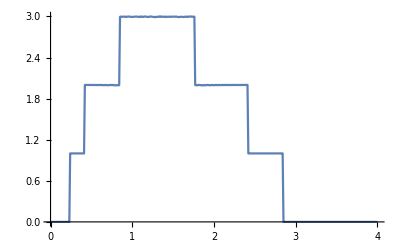

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,1,0]},{ω,0,4,0.01}]]
```

```mathematica
pris=Table[{ω,tr[ω,0.0001,1,0]},{ω,0,4,0.01}]
```

{{0.,2.8×10^-7},{0.01,2.8081×10^-7},{0.02,2.83264×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18578×10^-7},{0.12,4.58598×10^-7},{0.13,5.10023×10^-7},{0.14,5.77474×10^-7},{0.15,6.68349×10^-7},{0.16,7.95126×10^-7},{0.17,9.803×10^-7},{0.18,1.26801×10^-6},{0.19,1.75544×10^-6},{0.2,2.69447×10^-6},{0.21,4.92698×10^-6},{0.22,0.0000129427},{0.23,0.000120119},{0.24,0.999916},{0.25,0.999991},{0.26,0.999998},{0.27,1.},{0.28,0.999998},{0.29,0.999999},{0.3,0.999999},{0.31,0.999946},{0.32,0.999915},{0.33,0.999952},{0.34,0.999996},{0.35,0.999822},{0.36,0.999769},{0.37,0.999735},{0.38,1.},{0.39,0.999893},{0.4,0.99963},{0.41,1.00011},{0.42,1.99987},{0.43,1.99945},{0.44,1.99999},{0.45,1.99952},{0.46,1.99971},{0.47,1.99943},{0.48,1.99973},{0.49,1.99925},{0.5,1.99995},{0.51,1.99998},{0.52,1.99872},{0.53,1.99903},{0.54,1.99915},{0.55,1.99899},{0.56,1.99923},{0.57,1.99871},{0.58,1.9985},{0.59,1.99935},{0.6,1.9983},{0.61,1.99973},{0.62,1.99964},{0.63,1.99728},{0.64,1.99869},{0.65,1.99639},{0.66,1.99654},{0.67,1.99915},{0.68,1.99865},{0.69,1.99668},{0.7,1.99573},{0.71,1.99501},{0.72,1.99995},{0.73,1.99796},{0.74,1.99942},{0.75,1.99859},{0.76,1.99888},{0.77,1.99973},{0.78,1.99422},{0.79,1.99392},{0.8,1.99748},{0.81,1.99466},{0.82,1.99673},{0.83,1.99427},{0.84,1.99729},{0.85,2.99415},{0.86,2.99738},{0.87,2.9969},{0.88,2.99368},{0.89,2.99688},{0.9,2.99703},{0.91,2.99826},{0.92,2.99306},{0.93,2.99479},{0.94,2.99702},{0.95,2.99795},{0.96,2.99838},{0.97,2.99731},{0.98,2.99533},{0.99,2.99384},{1.,2.99292},{1.01,2.99364},{1.02,2.99578},{1.03,2.99662},{1.04,2.99781},{1.05,2.99861},{1.06,2.99696},{1.07,2.99589},{1.08,2.99219},{1.09,2.9932},{1.1,2.99975},{1.11,2.99456},{1.12,2.99765},{1.13,2.99223},{1.14,2.99549},{1.15,2.99935},{1.16,2.99916},{1.17,2.99604},{1.18,2.99491},{1.19,2.99388},{1.2,2.99225},{1.21,2.99619},{1.22,2.99985},{1.23,2.99859},{1.24,2.99607},{1.25,2.99439},{1.26,2.99278},{1.27,2.99171},{1.28,2.99009},{1.29,2.99517},{1.3,2.99131},{1.31,2.99452},{1.32,2.99871},{1.33,2.99407},{1.34,2.99995},{1.35,2.99374},{1.36,2.99898},{1.37,2.99554},{1.38,2.99573},{1.39,2.99695},{1.4,2.991},{1.41,2.99716},{1.42,2.99663},{1.43,2.99259},{1.44,2.99574},{1.45,2.99645},{1.46,2.99659},{1.47,2.99298},{1.48,2.99688},{1.49,2.99598},{1.5,2.99759},{1.51,2.99686},{1.52,2.99775},{1.53,2.99612},{1.54,2.99757},{1.55,2.99537},{1.56,2.99078},{1.57,2.99069},{1.58,2.99396},{1.59,2.99454},{1.6,2.99467},{1.61,2.99472},{1.62,2.9927},{1.63,2.9921},{1.64,2.99471},{1.65,2.99782},{1.66,2.99345},{1.67,2.99714},{1.68,2.9918},{1.69,2.99801},{1.7,2.99855},{1.71,2.9991},{1.72,2.9991},{1.73,2.99487},{1.74,2.9974},{1.75,2.99466},{1.76,2.99766},{1.77,1.99834},{1.78,1.99608},{1.79,1.99395},{1.8,1.99764},{1.81,1.99978},{1.82,1.99923},{1.83,1.99669},{1.84,1.99756},{1.85,1.99419},{1.86,1.99449},{1.87,1.99911},{1.88,1.99467},{1.89,1.99628},{1.9,1.99475},{1.91,1.99973},{1.92,1.99872},{1.93,1.99955},{1.94,1.99567},{1.95,1.99658},{1.96,1.99597},{1.97,1.99901},{1.98,1.99937},{1.99,1.99601},{2.,1.9979},{2.01,1.99629},{2.02,1.99987},{2.03,1.99932},{2.04,1.99719},{2.05,1.99723},{2.06,1.99969},{2.07,1.99981},{2.08,1.99704},{2.09,1.9971},{2.1,1.99995},{2.11,1.99965},{2.12,1.99871},{2.13,1.99995},{2.14,1.99908},{2.15,1.99907},{2.16,1.99869},{2.17,1.99998},{2.18,1.99832},{2.19,1.99819},{2.2,1.99945},{2.21,1.9987},{2.22,1.99985},{2.23,1.99987},{2.24,1.99901},{2.25,1.99902},{2.26,1.99933},{2.27,1.99996},{2.28,1.99936},{2.29,1.99901},{2.3,1.99895},{2.31,1.99899},{2.32,1.99904},{2.33,1.99916},{2.34,1.99957},{2.35,2.},{2.36,1.9993},{2.37,1.99999},{2.38,1.99988},{2.39,1.99998},{2.4,1.99953},{2.41,1.99974},{2.42,0.999707},{2.43,1.},{2.44,0.999808},{2.45,0.999992},{2.46,0.99971},{2.47,0.999831},{2.48,0.999838},{2.49,0.999799},{2.5,0.999848},{2.51,0.999922},{2.52,0.99992},{2.53,0.999886},{2.54,0.999958},{2.55,0.999932},{2.56,0.999992},{2.57,0.999952},{2.58,0.999996},{2.59,0.999968},{2.6,0.999968},{2.61,0.999988},{2.62,0.999995},{2.63,0.999995},{2.64,0.999997},{2.65,1.},{2.66,0.999996},{2.67,1.},{2.68,0.999999},{2.69,1.},{2.7,0.999998},{2.71,1.},{2.72,1.},{2.73,0.999999},{2.74,1.},{2.75,1.},{2.76,1.},{2.77,1.},{2.78,0.999999},{2.79,0.999999},{2.8,0.999999},{2.81,0.999998},{2.82,0.999997},{2.83,0.999992},{2.84,0.999958},{2.85,0.000496198},{2.86,0.0000165305},{2.87,4.97473×10^-6},{2.88,2.35363×10^-6},{2.89,1.36412×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7},{3.01,8.97514×10^-8},{3.02,7.9554×10^-8},{3.03,7.10012×10^-8},{3.04,6.37576×10^-8},{3.05,5.75691×10^-8},{3.06,5.22402×10^-8},{3.07,4.76186×10^-8},{3.08,4.35846×10^-8},{3.09,4.00423×10^-8},{3.1,3.69149×10^-8},{3.11,3.414×10^-8},{3.12,3.16663×10^-8},{3.13,2.94518×10^-8},{3.14,2.74614×10^-8},{3.15,2.56657×10^-8},{3.16,2.40401×10^-8},{3.17,2.25637×10^-8},{3.18,2.12187×10^-8},{3.19,1.99899×10^-8},{3.2,1.88644×10^-8},{3.21,1.78307×10^-8},{3.22,1.68791×10^-8},{3.23,1.60012×10^-8},{3.24,1.51895×10^-8},{3.25,1.44374×10^-8},{3.26,1.37393×10^-8},{3.27,1.30901×10^-8},{3.28,1.24853×10^-8},{3.29,1.1921×10^-8},{3.3,1.13935×10^-8},{3.31,1.08998×10^-8},{3.32,1.0437×10^-8},{3.33,1.00026×10^-8},{3.34,9.59432×10^-9},{3.35,9.21007×10^-9},{3.36,8.84801×10^-9},{3.37,8.50646×10^-9},{3.38,8.1839×10^-9},{3.39,7.87895×10^-9},{3.4,7.59034×10^-9},{3.41,7.31692×10^-9},{3.42,7.05766×10^-9},{3.43,6.81158×10^-9},{3.44,6.5778×10^-9},{3.45,6.35553×10^-9},{3.46,6.14401×10^-9},{3.47,5.94257×10^-9},{3.48,5.75058×10^-9},{3.49,5.56745×10^-9},{3.5,5.39265×10^-9},{3.51,5.22569×10^-9},{3.52,5.06609×10^-9},{3.53,4.91344×10^-9},{3.54,4.76734×10^-9},{3.55,4.62743×10^-9},{3.56,4.49335×10^-9},{3.57,4.36479×10^-9},{3.58,4.24145×10^-9},{3.59,4.12306×10^-9},{3.6,4.00935×10^-9},{3.61,3.90008×10^-9},{3.62,3.79503×10^-9},{3.63,3.69399×10^-9},{3.64,3.59674×10^-9},{3.65,3.50311×10^-9},{3.66,3.41293×10^-9},{3.67,3.32601×10^-9},{3.68,3.24222×10^-9},{3.69,3.1614×10^-9},{3.7,3.08341×10^-9},{3.71,3.00813×10^-9},{3.72,2.93544×10^-9},{3.73,2.86521×10^-9},{3.74,2.79734×10^-9},{3.75,2.73172×10^-9},{3.76,2.66827×10^-9},{3.77,2.60687×10^-9},{3.78,2.54746×10^-9},{3.79,2.48994×10^-9},{3.8,2.43423×10^-9},{3.81,2.38026×10^-9},{3.82,2.32797×10^-9},{3.83,2.27728×10^-9},{3.84,2.22812×10^-9},{3.85,2.18045×10^-9},{3.86,2.13419×10^-9},{3.87,2.08931×10^-9},{3.88,2.04573×10^-9},{3.89,2.00342×10^-9},{3.9,1.96232×10^-9},{3.91,1.92239×10^-9},{3.92,1.88359×10^-9},{3.93,1.84588×10^-9},{3.94,1.80921×10^-9},{3.95,1.77355×10^-9},{3.96,1.73887×10^-9},{3.97,1.70512×10^-9},{3.98,1.67227×10^-9},{3.99,1.64031×10^-9},{4.,1.60918×10^-9}}

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],Table[imp,30]]]
```

{imp,imp6,imp,imp13,imp3,imp3,imp8,imp,imp,imp6,imp,imp,imp,imp12,imp1,imp4,imp14,imp6,imp,imp,imp13,imp8,imp10,imp10,imp11,imp14,imp10,imp4,imp1,imp7,imp5,imp,imp9,imp,imp8,imp3,imp,imp9,imp,imp,imp12,imp6,imp,imp4,imp2,imp,imp12,imp7,imp12,imp3,imp10,imp5,imp1,imp9,imp8,imp13,imp5,imp,imp8,imp,imp11,imp6,imp,imp,imp,imp2,imp,imp13,imp,imp11,imp14,imp2,imp5,imp13,imp11,imp12,imp10,imp,imp1,imp1,imp,imp2,imp7,imp5,imp7,imp11,imp9,imp14,imp,imp7,imp9,imp,imp,imp4,imp14,imp,imp2,imp4,imp,imp3}

```mathematica
m5[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp,imp6,imp,imp13,imp3,imp3,imp8,imp,imp,imp6,imp,imp,imp,imp12,imp1,imp4,imp14,imp6,imp,imp,imp13,imp8,imp10,imp10,imp11,imp14,imp10,imp4,imp1,imp7,imp5,imp,imp9,imp,imp8,imp3,imp,imp9,imp,imp,imp12,imp6,imp,imp4,imp2,imp,imp12,imp7,imp12,imp3,imp10,imp5,imp1,imp9,imp8,imp13,imp5,imp,imp8,imp,imp11,imp6,imp,imp,imp,imp2,imp,imp13,imp,imp11,imp14,imp2,imp5,imp13,imp11,imp12,imp10,imp,imp1,imp1,imp,imp2,imp7,imp5,imp7,imp11,imp9,imp14,imp,imp7,imp9,imp,imp,imp4,imp14,imp,imp2,imp4,imp,imp3}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
Table[{ω,Mean[Table[m5[ω,0.5],4000]]},{ω,Range[0,3,0.01]}]
```

```mathematica
{{0.,2.551855827217078*^-7},{0.01,2.472531585496278*^-7},{0.02,2.5887322419038874*^-7},{0.03,2.7072889822958274*^-7},{0.04,2.784232231385534*^-7},{0.05,2.894051089511448*^-7},{0.06,3.020021083407303*^-7},{0.07,3.152416124754691*^-7},{0.08,3.326353476965608*^-7},{0.09,3.5306435838040037*^-7},{0.1,3.7726510112072507*^-7},{0.11,4.0981092023004196*^-7},{0.12,4.506342593167837*^-7},{0.13,5.014908700898997*^-7},{0.14,5.703683460727604*^-7},{0.15,6.611758070250565*^-7},{0.16,7.865982027036346*^-7},{0.17,9.716210143986357*^-7},{0.18,1.2558663653381476*^-6},{0.19,1.738265110567449*^-6},{0.2,2.6700328997596304*^-6},{0.21,4.880864706695701*^-6},{0.22,0.000012786466713770413},{0.23,0.00011719948070423845},{0.24,0.06286997530000761},{0.25,0.0849622243756844},{0.26,0.16706224217724255},{0.27,0.26199011162978014},{0.28,0.33114970337418226},{0.29,0.3932764252610731},{0.3,0.43525609023650563},{0.31,0.4581700212689875},{0.32,0.4863381778715211},{0.33,0.4985202726421823},{0.34,0.5208668889080565},{0.35000000000000003,0.5203113206493408},{0.36,0.5325771003387083},{0.37,0.5305819952399817},{0.38,0.5337157233396899},{0.39,0.5248314463088743},{0.4,0.5026129136899143},{0.41000000000000003,0.4644786787037442},{0.42,0.549819814314518},{0.43,0.6773263698607184},{0.44,0.7703423592764032},{0.45,0.7299213637691199},{0.46,0.6291609662496317},{0.47000000000000003,0.590898108745399},{0.48,0.5886021913455171},{0.49,0.6020214089386777},{0.5,0.6437701543931639},{0.51,0.6535273016683445},{0.52,0.6799787386849087},{0.53,0.697161196363795},{0.54,0.7276496538163374},{0.55,0.7663009161366595},{0.56,0.786841015242835},{0.5700000000000001,0.809450898271862},{0.58,0.8270202386496667},{0.59,0.8279817455729738},{0.6,0.8676042755602669},{0.61,0.8961459155795924},{0.62,0.9042315974270214},{0.63,0.9192787094166888},{0.64,0.9507775363158594},{0.65,0.9508723726845847},{0.66,0.9679522145222486},{0.67,0.9796774485785932},{0.68,0.9740006722425861},{0.6900000000000001,1.008589499637223},{0.7000000000000001,1.011038624257873},{0.71,1.0206116027757546},{0.72,1.0200006130100807},{0.73,1.0359054094514988},{0.74,1.050137343861804},{0.75,1.0536848271510486},{0.76,1.0600269511483382},{0.77,1.0643213463151155},{0.78,1.0856008168563633},{0.79,1.0837501372926894},{0.8,1.1013210650454675},{0.81,1.0761815130865011},{0.8200000000000001,1.0745130160173706},{0.8300000000000001,1.0451626692884142},{0.84,0.9980089576519849},{0.85,0.788410908760177},{0.86,0.8208988630062867},{0.87,0.9383604536831863},{0.88,0.774555618630429},{0.89,0.6926452493210656},{0.9,0.6918111413871493},{0.91,0.7092704508796064},{0.92,0.7790075384352788},{0.93,0.8352505376122893},{0.9400000000000001,0.8925716334071164},{0.9500000000000001,0.9461930947435605},{0.96,1.0401730275502077},{0.97,1.085539675131963},{0.98,1.1953772510385692},{0.99,1.2277630151146834},{1.,1.297161258255519},{1.01,1.3910266132082647},{1.02,1.2646197926230862},{1.03,1.0001068335662175},{1.04,0.567896666679809},{1.05,0.3624229583815943},{1.06,0.3371381332276457},{1.07,0.35012911597548596},{1.08,0.33322374484228123},{1.09,0.3341523769731697},{1.1,0.3389626337037072},{1.11,0.3676441099201047},{1.12,0.39327125653046},{1.1300000000000001,0.43551653312190836},{1.1400000000000001,0.4785590858883457},{1.1500000000000001,0.49809511986556426},{1.16,0.5489557532607684},{1.17,0.571486609571113},{1.18,0.6151817981258282},{1.19,0.6297760481308128},{1.2,0.6610933952102387},{1.21,0.6746548641701333},{1.22,0.7142130992175719},{1.23,0.7286935616679641},{1.24,0.7009481877732728},{1.25,0.7431734861268564},{1.26,0.755550602964503},{1.27,0.7311929972209832},{1.28,0.7130181701628496},{1.29,0.7136056958746583},{1.3,0.7334411594282594},{1.31,0.7162084699139931},{1.32,0.7186719706330154},{1.33,0.7716807955491156},{1.34,0.7095396385324837},{1.35,0.7657822515300456},{1.36,0.7557999396249558},{1.37,0.7810055926762386},{1.3800000000000001,0.7658224256993351},{1.3900000000000001,0.7325362621392603},{1.4000000000000001,0.7442589959151666},{1.41,0.7567091458054769},{1.42,0.729121543784867},{1.43,0.7486484347775612},{1.44,0.7460493616085537},{1.45,0.6743955778836166},{1.46,0.6051039324472668},{1.47,0.5841047721770177},{1.48,0.6238450583786644},{1.49,0.6558289765415741},{1.5,0.6641188842635395},{1.51,0.6581660907183294},{1.52,0.6648106814474781},{1.53,0.6476334440292717},{1.54,0.6517391265196358},{1.55,0.6137861593094198},{1.56,0.5663482627108648},{1.57,0.5185981083927759},{1.58,0.4853389614362145},{1.59,0.4835727739172881},{1.6,0.49506176529149115},{1.61,0.49691209311379525},{1.62,0.4954033382661884},{1.6300000000000001,0.48720755197037463},{1.6400000000000001,0.4871509856957372},{1.6500000000000001,0.47284017508186116},{1.6600000000000001,0.4691124348055457},{1.67,0.4739969368653593},{1.68,0.4769103557233398},{1.69,0.4569548502364211},{1.7,0.5363190839130646},{1.71,0.5216933709276438},{1.72,0.678270909859069},{1.73,0.7403280279009882},{1.74,0.8764309037822791},{1.75,1.3320592134485723},{1.76,1.8901672720204146},{1.77,1.5134423720605101},{1.78,1.3199569260948147},{1.79,1.1356098075673213},{1.8,0.8571406203162762},{1.81,0.6913564923489928},{1.82,0.48101222558217277},{1.83,0.4442576959238412},{1.84,0.4543642375504746},{1.85,0.5156213777573214},{1.86,0.5425313315061836},{1.87,0.5729555649501603},{1.8800000000000001,0.6097843674228179},{1.8900000000000001,0.6257796598872903},{1.9000000000000001,0.6460360967043748},{1.9100000000000001,0.6139098188350584},{1.92,0.5539546099903082},{1.93,0.4344162163573843},{1.94,0.5197806048148318},{1.95,0.6072299842576793},{1.96,0.6252200216994829},{1.97,0.6360015576091554},{1.98,0.6384199029722963},{1.99,0.6543714733769175},{2.,0.6656552514303603},{2.0100000000000002,0.665836459639805},{2.02,0.6522880146741425},{2.0300000000000002,0.6497466568148311},{2.04,0.664718502054864},{2.05,0.6526510908599362},{2.06,0.6589948656017867},{2.07,0.6665875875674809},{2.08,0.6530327250595553},{2.09,0.6501082839349687},{2.1,0.6186385286304884},{2.11,0.5893985196053797},{2.12,0.5385104871527701},{2.13,0.4755759698729079},{2.14,0.5057349575043699},{2.15,0.535310367295785},{2.16,0.5520759470246039},{2.17,0.5485553944176046},{2.18,0.541699520103318},{2.19,0.5379256341215582},{2.2,0.5276287410486898},{2.21,0.5198966513635689},{2.22,0.5146885730359678},{2.23,0.4859565903779354},{2.24,0.4973573281133612},{2.25,0.47737302881353266},{2.2600000000000002,0.4693351519382718},{2.27,0.4499221290783845},{2.2800000000000002,0.4303764200352427},{2.29,0.41855203935227814},{2.3000000000000003,0.40459714047575496},{2.31,0.3904262165170642},{2.32,0.37434398822858167},{2.33,0.3647694750841438},{2.34,0.3542354804496241},{2.35,0.34069188189029964},{2.36,0.33426171897800877},{2.37,0.3353485781087018},{2.38,0.37313320999919736},{2.39,0.43391579830824545},{2.4,0.561750574330799},{2.41,0.8921492928780743},{2.42,0.6652584954208359},{2.43,0.5874313122686731},{2.44,0.5041880284049397},{2.45,0.40094606684665607},{2.46,0.30037858665175404},{2.47,0.25141957963450795},{2.48,0.23604299637333814},{2.49,0.24721065543867862},{2.5,0.2662948569479248},{2.5100000000000002,0.28430448362292193},{2.52,0.29029212631165874},{2.5300000000000002,0.2969239446208517},{2.54,0.2989154124225854},{2.5500000000000003,0.3025751365913725},{2.56,0.3041048024471124},{2.57,0.3078703043802409},{2.58,0.309478086061023},{2.59,0.3101885624336647},{2.6,0.31104677515280515},{2.61,0.3020011837419968},{2.62,0.295550706252651},{2.63,0.29606661969862885},{2.64,0.29774553258582237},{2.65,0.2825505850845268},{2.66,0.28333570905053895},{2.67,0.2843576081198263},{2.68,0.28039374934065353},{2.69,0.2701398854084827},{2.7,0.2649846445856064},{2.71,0.2584058011314629},{2.72,0.2435418979952618},{2.73,0.23977467345599654},{2.74,0.22950774616559078},{2.75,0.2193818452561436},{2.7600000000000002,0.20877783304458564},{2.77,0.20347369276717014},{2.7800000000000002,0.18877183516340165},{2.79,0.17678885055324575},{2.8000000000000003,0.16713725650975847},{2.81,0.15470259611262616},{2.82,0.14435741566016203},{2.83,0.13648049001355397},{2.84,0.13900768024512877},{2.85,0.0004255615182321729},{2.86,0.000016245480915300385},{2.87,4.91553456804792*^-6},{2.88,2.3129844015392273*^-6},{2.89,1.3332392243776227*^-6},{2.9,8.554619012836455*^-7},{2.91,5.951017177542354*^-7},{2.92,4.395740433255857*^-7},{2.93,3.4014278649891847*^-7},{2.94,2.7343984595747113*^-7},{2.95,2.2211108074161824*^-7},{2.96,1.8536052114028146*^-7},{2.97,1.5501074216452805*^-7},{2.98,1.3179282393549642*^-7},{2.99,1.125061535708385*^-7},{3.,9.869124040872261*^-8}}
```

{{0.,2.55186×10^-7},{0.01,2.47253×10^-7},{0.02,2.58873×10^-7},{0.03,2.70729×10^-7},{0.04,2.78423×10^-7},{0.05,2.89405×10^-7},{0.06,3.02002×10^-7},{0.07,3.15242×10^-7},{0.08,3.32635×10^-7},{0.09,3.53064×10^-7},{0.1,3.77265×10^-7},{0.11,4.09811×10^-7},{0.12,4.50634×10^-7},{0.13,5.01491×10^-7},{0.14,5.70368×10^-7},{0.15,6.61176×10^-7},{0.16,7.86598×10^-7},{0.17,9.71621×10^-7},{0.18,1.25587×10^-6},{0.19,1.73827×10^-6},{0.2,2.67003×10^-6},{0.21,4.88086×10^-6},{0.22,0.0000127865},{0.23,0.000117199},{0.24,0.06287},{0.25,0.0849622},{0.26,0.167062},{0.27,0.26199},{0.28,0.33115},{0.29,0.393276},{0.3,0.435256},{0.31,0.45817},{0.32,0.486338},{0.33,0.49852},{0.34,0.520867},{0.35,0.520311},{0.36,0.532577},{0.37,0.530582},{0.38,0.533716},{0.39,0.524831},{0.4,0.502613},{0.41,0.464479},{0.42,0.54982},{0.43,0.677326},{0.44,0.770342},{0.45,0.729921},{0.46,0.629161},{0.47,0.590898},{0.48,0.588602},{0.49,0.602021},{0.5,0.64377},{0.51,0.653527},{0.52,0.679979},{0.53,0.697161},{0.54,0.72765},{0.55,0.766301},{0.56,0.786841},{0.57,0.809451},{0.58,0.82702},{0.59,0.827982},{0.6,0.867604},{0.61,0.896146},{0.62,0.904232},{0.63,0.919279},{0.64,0.950778},{0.65,0.950872},{0.66,0.967952},{0.67,0.979677},{0.68,0.974001},{0.69,1.00859},{0.7,1.01104},{0.71,1.02061},{0.72,1.02},{0.73,1.03591},{0.74,1.05014},{0.75,1.05368},{0.76,1.06003},{0.77,1.06432},{0.78,1.0856},{0.79,1.08375},{0.8,1.10132},{0.81,1.07618},{0.82,1.07451},{0.83,1.04516},{0.84,0.998009},{0.85,0.788411},{0.86,0.820899},{0.87,0.93836},{0.88,0.774556},{0.89,0.692645},{0.9,0.691811},{0.91,0.70927},{0.92,0.779008},{0.93,0.835251},{0.94,0.892572},{0.95,0.946193},{0.96,1.04017},{0.97,1.08554},{0.98,1.19538},{0.99,1.22776},{1.,1.29716},{1.01,1.39103},{1.02,1.26462},{1.03,1.00011},{1.04,0.567897},{1.05,0.362423},{1.06,0.337138},{1.07,0.350129},{1.08,0.333224},{1.09,0.334152},{1.1,0.338963},{1.11,0.367644},{1.12,0.393271},{1.13,0.435517},{1.14,0.478559},{1.15,0.498095},{1.16,0.548956},{1.17,0.571487},{1.18,0.615182},{1.19,0.629776},{1.2,0.661093},{1.21,0.674655},{1.22,0.714213},{1.23,0.728694},{1.24,0.700948},{1.25,0.743173},{1.26,0.755551},{1.27,0.731193},{1.28,0.713018},{1.29,0.713606},{1.3,0.733441},{1.31,0.716208},{1.32,0.718672},{1.33,0.771681},{1.34,0.70954},{1.35,0.765782},{1.36,0.7558},{1.37,0.781006},{1.38,0.765822},{1.39,0.732536},{1.4,0.744259},{1.41,0.756709},{1.42,0.729122},{1.43,0.748648},{1.44,0.746049},{1.45,0.674396},{1.46,0.605104},{1.47,0.584105},{1.48,0.623845},{1.49,0.655829},{1.5,0.664119},{1.51,0.658166},{1.52,0.664811},{1.53,0.647633},{1.54,0.651739},{1.55,0.613786},{1.56,0.566348},{1.57,0.518598},{1.58,0.485339},{1.59,0.483573},{1.6,0.495062},{1.61,0.496912},{1.62,0.495403},{1.63,0.487208},{1.64,0.487151},{1.65,0.47284},{1.66,0.469112},{1.67,0.473997},{1.68,0.47691},{1.69,0.456955},{1.7,0.536319},{1.71,0.521693},{1.72,0.678271},{1.73,0.740328},{1.74,0.876431},{1.75,1.33206},{1.76,1.89017},{1.77,1.51344},{1.78,1.31996},{1.79,1.13561},{1.8,0.857141},{1.81,0.691356},{1.82,0.481012},{1.83,0.444258},{1.84,0.454364},{1.85,0.515621},{1.86,0.542531},{1.87,0.572956},{1.88,0.609784},{1.89,0.62578},{1.9,0.646036},{1.91,0.61391},{1.92,0.553955},{1.93,0.434416},{1.94,0.519781},{1.95,0.60723},{1.96,0.62522},{1.97,0.636002},{1.98,0.63842},{1.99,0.654371},{2.,0.665655},{2.01,0.665836},{2.02,0.652288},{2.03,0.649747},{2.04,0.664719},{2.05,0.652651},{2.06,0.658995},{2.07,0.666588},{2.08,0.653033},{2.09,0.650108},{2.1,0.618639},{2.11,0.589399},{2.12,0.53851},{2.13,0.475576},{2.14,0.505735},{2.15,0.53531},{2.16,0.552076},{2.17,0.548555},{2.18,0.5417},{2.19,0.537926},{2.2,0.527629},{2.21,0.519897},{2.22,0.514689},{2.23,0.485957},{2.24,0.497357},{2.25,0.477373},{2.26,0.469335},{2.27,0.449922},{2.28,0.430376},{2.29,0.418552},{2.3,0.404597},{2.31,0.390426},{2.32,0.374344},{2.33,0.364769},{2.34,0.354235},{2.35,0.340692},{2.36,0.334262},{2.37,0.335349},{2.38,0.373133},{2.39,0.433916},{2.4,0.561751},{2.41,0.892149},{2.42,0.665258},{2.43,0.587431},{2.44,0.504188},{2.45,0.400946},{2.46,0.300379},{2.47,0.25142},{2.48,0.236043},{2.49,0.247211},{2.5,0.266295},{2.51,0.284304},{2.52,0.290292},{2.53,0.296924},{2.54,0.298915},{2.55,0.302575},{2.56,0.304105},{2.57,0.30787},{2.58,0.309478},{2.59,0.310189},{2.6,0.311047},{2.61,0.302001},{2.62,0.295551},{2.63,0.296067},{2.64,0.297746},{2.65,0.282551},{2.66,0.283336},{2.67,0.284358},{2.68,0.280394},{2.69,0.27014},{2.7,0.264985},{2.71,0.258406},{2.72,0.243542},{2.73,0.239775},{2.74,0.229508},{2.75,0.219382},{2.76,0.208778},{2.77,0.203474},{2.78,0.188772},{2.79,0.176789},{2.8,0.167137},{2.81,0.154703},{2.82,0.144357},{2.83,0.13648},{2.84,0.139008},{2.85,0.000425562},{2.86,0.0000162455},{2.87,4.91553×10^-6},{2.88,2.31298×10^-6},{2.89,1.33324×10^-6},{2.9,8.55462×10^-7},{2.91,5.95102×10^-7},{2.92,4.39574×10^-7},{2.93,3.40143×10^-7},{2.94,2.7344×10^-7},{2.95,2.22111×10^-7},{2.96,1.85361×10^-7},{2.97,1.55011×10^-7},{2.98,1.31793×10^-7},{2.99,1.12506×10^-7},{3.,9.86912×10^-8}}

```mathematica
m6[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp7,imp2,imp7,imp4,imp11,imp4,imp8,imp2,imp3,imp1,imp,imp11,imp13,imp9,imp3,imp5,imp4,imp8,imp14,imp8,imp2,imp,imp2,imp6,imp7,imp,imp13,imp8,imp3,imp5,imp14,imp10,imp2,imp7,imp10,imp,imp13,imp,imp8,imp10,imp,imp9,imp5,imp8,imp,imp11,imp5,imp3,imp6,imp,imp14,imp7,imp10,imp,imp,imp6,imp,imp4,imp11,imp1,imp13,imp9,imp6,imp13,imp,imp9,imp5,imp10,imp13,imp1,imp,imp4,imp1,imp1,imp12,imp12,imp3,imp6,imp7,imp9,imp10,imp12,imp4,imp12,imp,imp14,imp,imp12,imp2,imp12,imp14,imp1,imp5,imp11,imp6,imp9,imp,imp11,imp3,imp14}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
Table[{ω,Mean[Table[m6[ω,0.5],4000]]},{ω,Range[0,3,0.01]}]
```

```mathematica
{{0.,2.5608930790497576*^-7},{0.01,2.516863234674359*^-7},{0.02,2.6468826886219975*^-7},{0.03,2.7532249600713266*^-7},{0.04,2.8499889052560943*^-7},{0.05,2.945403992838261*^-7},{0.06,3.0682009040014075*^-7},{0.07,3.212700699889741*^-7},{0.08,3.375080171064576*^-7},{0.09,3.5916549687795486*^-7},{0.1,3.8418835932084843*^-7},{0.11,4.1501625728485786*^-7},{0.12,4.560549022991346*^-7},{0.13,5.076837673979491*^-7},{0.14,5.748975299180212*^-7},{0.15,6.658375733130318*^-7},{0.16,7.928003731435952*^-7},{0.17,9.770990692870913*^-7},{0.18,1.2635222641955229*^-6},{0.19,1.7495677432023483*^-6},{0.2,2.687169870742093*^-6},{0.21,4.918758098355779*^-6},{0.22,0.00001288794467757766},{0.23,0.00011844684558640893},{0.24,0.05890272228003309},{0.25,0.07730943218917449},{0.26,0.13142386670272163},{0.27,0.21207168858412132},{0.28,0.28871876435052296},{0.29,0.3453071589119436},{0.3,0.3992413795004029},{0.31,0.42886555646882707},{0.32,0.4481930637878094},{0.33,0.4528446988493632},{0.34,0.474382109820932},{0.35000000000000003,0.47516789195044573},{0.36,0.4842372096926773},{0.37,0.4953389180371716},{0.38,0.48876022810652026},{0.39,0.4759726328101708},{0.4,0.46193973834830915},{0.41000000000000003,0.44318737085424825},{0.42,0.5245211169590712},{0.43,0.5996366187784559},{0.44,0.7506676996368081},{0.45,0.7513961594563555},{0.46,0.6525981229223219},{0.47000000000000003,0.601900643883899},{0.48,0.569025024655475},{0.49,0.5688089679639474},{0.5,0.5742186091049403},{0.51,0.5986918459297894},{0.52,0.617519273947603},{0.53,0.6245845188574755},{0.54,0.6528118193476267},{0.55,0.6835121373619923},{0.56,0.6988791199336916},{0.5700000000000001,0.7223756460365499},{0.58,0.7445099110037044},{0.59,0.7451847848016391},{0.6,0.7776679960166373},{0.61,0.8163837112107369},{0.62,0.82169900509541},{0.63,0.8247840455616884},{0.64,0.8526972977406144},{0.65,0.8557776011578213},{0.66,0.8811183751899186},{0.67,0.8781006367719209},{0.68,0.8853001032070013},{0.6900000000000001,0.9032267780721266},{0.7000000000000001,0.900085366194173},{0.71,0.9142542554300622},{0.72,0.924963343418161},{0.73,0.938474397980743},{0.74,0.9696106978247374},{0.75,0.9514158320915922},{0.76,0.9505092013612425},{0.77,0.946323203574668},{0.78,0.9904089883774816},{0.79,0.9788629457433305},{0.8,1.0070818297983102},{0.81,0.9869138179270974},{0.8200000000000001,0.9665028838578705},{0.8300000000000001,0.9501368996100067},{0.84,0.8907015231992619},{0.85,0.7518202143869079},{0.86,0.7536183644410128},{0.87,0.875597640738569},{0.88,0.853912686666853},{0.89,0.7076354567486057},{0.9,0.6707237055415309},{0.91,0.6637978302424421},{0.92,0.6788839405174528},{0.93,0.7187783296752723},{0.9400000000000001,0.7871532413877382},{0.9500000000000001,0.825119069526542},{0.96,0.8923128137613241},{0.97,0.9569705904178846},{0.98,1.0505194962206088},{0.99,1.0941518836158286},{1.,1.14944364310466},{1.01,1.2575570048098204},{1.02,1.1519672360319524},{1.03,0.8849467046989639},{1.04,0.5032667749068707},{1.05,0.3600344382220152},{1.06,0.3404332993133259},{1.07,0.36168266614494815},{1.08,0.3445901757211368},{1.09,0.3270112935766148},{1.1,0.32956696926376333},{1.11,0.3562732674061041},{1.12,0.3651214628052649},{1.1300000000000001,0.38966836557759815},{1.1400000000000001,0.40547663595702854},{1.1500000000000001,0.4287585356032522},{1.16,0.4638465338520492},{1.17,0.4799467257866188},{1.18,0.5117671712628494},{1.19,0.5267392540465388},{1.2,0.5506018843013999},{1.21,0.5821908557459853},{1.22,0.6013386575570925},{1.23,0.6097743624419738},{1.24,0.5729761708370552},{1.25,0.6162030796766391},{1.26,0.6457020061177307},{1.27,0.6049217259791811},{1.28,0.6029824253464733},{1.29,0.6019126395545921},{1.3,0.6308087103611749},{1.31,0.6065655991963113},{1.32,0.5967870686028711},{1.33,0.6338461497573973},{1.34,0.5915987041166616},{1.35,0.6244420048936179},{1.36,0.6432803335588976},{1.37,0.6448814097270529},{1.3800000000000001,0.6480929997909232},{1.3900000000000001,0.613409096961572},{1.4000000000000001,0.6226441162649722},{1.41,0.635019309388957},{1.42,0.6050297820639005},{1.43,0.6265179803404866},{1.44,0.6219113941766781},{1.45,0.5783965885585769},{1.46,0.5239687678723585},{1.47,0.47754458757298424},{1.48,0.48807989842589183},{1.49,0.5287318929699094},{1.5,0.5504432406598366},{1.51,0.5299886838633242},{1.52,0.535486860614069},{1.53,0.5350573668946036},{1.54,0.540649496750652},{1.55,0.5166097402099347},{1.56,0.49175226421381113},{1.57,0.45652782420074234},{1.58,0.4413105165231971},{1.59,0.4334218823617582},{1.6,0.43085746627125193},{1.61,0.4443798297401402},{1.62,0.437008269669515},{1.6300000000000001,0.4287320134020611},{1.6400000000000001,0.4214745896932466},{1.6500000000000001,0.43115493066703786},{1.6600000000000001,0.4400553039577794},{1.67,0.47804703818497085},{1.68,0.4582915455205692},{1.69,0.4619037696173158},{1.7,0.5569575444413478},{1.71,0.5543010990910945},{1.72,0.747745642674279},{1.73,0.8091829153117178},{1.74,0.952432564872046},{1.75,1.3994044107868508},{1.76,1.9517682614347305},{1.77,1.5845071721041513},{1.78,1.4331781596717201},{1.79,1.2371105314842075},{1.8,1.0292722318266996},{1.81,0.8183108679972756},{1.82,0.5537109395921387},{1.83,0.43846905285436255},{1.84,0.38911872789968954},{1.85,0.41375477572392483},{1.86,0.44830371776999384},{1.87,0.47450926062426607},{1.8800000000000001,0.5125980487396495},{1.8900000000000001,0.5297092219585062},{1.9000000000000001,0.5351042019335602},{1.9100000000000001,0.5274863590986556},{1.92,0.49124482020739685},{1.93,0.3998912500764394},{1.94,0.35556622859911174},{1.95,0.46197209677449563},{1.96,0.5118245703898594},{1.97,0.5220159861898075},{1.98,0.5436446732631305},{1.99,0.5536729005822737},{2.,0.5657292637187615},{2.0100000000000002,0.5634787963562006},{2.02,0.5611864790004122},{2.0300000000000002,0.5597601838092966},{2.04,0.5670274701008569},{2.05,0.561523501683997},{2.06,0.5788974306883183},{2.07,0.5717479098925108},{2.08,0.5595983075595122},{2.09,0.5558239692765881},{2.1,0.5377594028782465},{2.11,0.5145890500623431},{2.12,0.4751574808289134},{2.13,0.4144006927132996},{2.14,0.4068552274230462},{2.15,0.4219764388881347},{2.16,0.4481886430922814},{2.17,0.46112751449481604},{2.18,0.4614791373649336},{2.19,0.45667862458408404},{2.2,0.4370068552878961},{2.21,0.44690955034470475},{2.22,0.42798910259817624},{2.23,0.42389017188204536},{2.24,0.41334605593312534},{2.25,0.41026331374656355},{2.2600000000000002,0.39893294565103077},{2.27,0.39093524036743665},{2.2800000000000002,0.36814296850767675},{2.29,0.3701132965987324},{2.3000000000000003,0.3547922970652702},{2.31,0.35098404588062615},{2.32,0.33855524956046595},{2.33,0.31866853747636653},{2.34,0.3164608081091254},{2.35,0.31688326173994413},{2.36,0.3237032751854351},{2.37,0.32589132382431585},{2.38,0.3726969644378954},{2.39,0.4474314158930739},{2.4,0.5712096677530129},{2.41,0.9373050479844526},{2.42,0.6697247835041102},{2.43,0.6358431961994482},{2.44,0.5608817159759876},{2.45,0.4680878288611942},{2.46,0.3594625155308397},{2.47,0.27485298034874384},{2.48,0.22308627768624759},{2.49,0.2207101552733998},{2.5,0.23366931512954414},{2.5100000000000002,0.24532275162126568},{2.52,0.24867565192645913},{2.5300000000000002,0.26156280170943386},{2.54,0.2585450959675851},{2.5500000000000003,0.2659260584349761},{2.56,0.2657318331394251},{2.57,0.2649148618112377},{2.58,0.27495181030206717},{2.59,0.271495546210585},{2.6,0.278323308064175},{2.61,0.270180024888564},{2.62,0.2739755487378792},{2.63,0.2641677479346722},{2.64,0.2614840940522071},{2.65,0.2622244519515043},{2.66,0.2544926862128048},{2.67,0.25605005435495504},{2.68,0.2528280177571443},{2.69,0.24691347853444182},{2.7,0.24241926479785678},{2.71,0.23384724178915775},{2.72,0.2336963772834776},{2.73,0.22167242546042953},{2.74,0.22041805995279948},{2.75,0.21113897385165595},{2.7600000000000002,0.19615859940877775},{2.77,0.19606771093641737},{2.7800000000000002,0.18581180969031533},{2.79,0.17539669071267527},{2.8000000000000003,0.16226166593099048},{2.81,0.1535627931394662},{2.82,0.14481300220460197},{2.83,0.1454840196861319},{2.84,0.15650435853982628},{2.85,0.00043873971004251724},{2.86,0.000016365545796596903},{2.87,4.938877887054514*^-6},{2.88,2.3377895987806777*^-6},{2.89,1.3496031317801823*^-6},{2.9,8.684831703254613*^-7},{2.91,6.036647129795862*^-7},{2.92,4.4654014230184957*^-7},{2.93,3.4632759150719957*^-7},{2.94,2.7567597682641606*^-7},{2.95,2.2467552482478858*^-7},{2.96,1.8661016762629912*^-7},{2.97,1.5679317789723466*^-7},{2.98,1.3327164943344674*^-7},{2.99,1.1400170586331434*^-7},{3.,1.0003213873848492*^-7}}
```

{{0.,2.56089×10^-7},{0.01,2.51686×10^-7},{0.02,2.64688×10^-7},{0.03,2.75322×10^-7},{0.04,2.84999×10^-7},{0.05,2.9454×10^-7},{0.06,3.0682×10^-7},{0.07,3.2127×10^-7},{0.08,3.37508×10^-7},{0.09,3.59165×10^-7},{0.1,3.84188×10^-7},{0.11,4.15016×10^-7},{0.12,4.56055×10^-7},{0.13,5.07684×10^-7},{0.14,5.74898×10^-7},{0.15,6.65838×10^-7},{0.16,7.928×10^-7},{0.17,9.77099×10^-7},{0.18,1.26352×10^-6},{0.19,1.74957×10^-6},{0.2,2.68717×10^-6},{0.21,4.91876×10^-6},{0.22,0.0000128879},{0.23,0.000118447},{0.24,0.0589027},{0.25,0.0773094},{0.26,0.131424},{0.27,0.212072},{0.28,0.288719},{0.29,0.345307},{0.3,0.399241},{0.31,0.428866},{0.32,0.448193},{0.33,0.452845},{0.34,0.474382},{0.35,0.475168},{0.36,0.484237},{0.37,0.495339},{0.38,0.48876},{0.39,0.475973},{0.4,0.46194},{0.41,0.443187},{0.42,0.524521},{0.43,0.599637},{0.44,0.750668},{0.45,0.751396},{0.46,0.652598},{0.47,0.601901},{0.48,0.569025},{0.49,0.568809},{0.5,0.574219},{0.51,0.598692},{0.52,0.617519},{0.53,0.624585},{0.54,0.652812},{0.55,0.683512},{0.56,0.698879},{0.57,0.722376},{0.58,0.74451},{0.59,0.745185},{0.6,0.777668},{0.61,0.816384},{0.62,0.821699},{0.63,0.824784},{0.64,0.852697},{0.65,0.855778},{0.66,0.881118},{0.67,0.878101},{0.68,0.8853},{0.69,0.903227},{0.7,0.900085},{0.71,0.914254},{0.72,0.924963},{0.73,0.938474},{0.74,0.969611},{0.75,0.951416},{0.76,0.950509},{0.77,0.946323},{0.78,0.990409},{0.79,0.978863},{0.8,1.00708},{0.81,0.986914},{0.82,0.966503},{0.83,0.950137},{0.84,0.890702},{0.85,0.75182},{0.86,0.753618},{0.87,0.875598},{0.88,0.853913},{0.89,0.707635},{0.9,0.670724},{0.91,0.663798},{0.92,0.678884},{0.93,0.718778},{0.94,0.787153},{0.95,0.825119},{0.96,0.892313},{0.97,0.956971},{0.98,1.05052},{0.99,1.09415},{1.,1.14944},{1.01,1.25756},{1.02,1.15197},{1.03,0.884947},{1.04,0.503267},{1.05,0.360034},{1.06,0.340433},{1.07,0.361683},{1.08,0.34459},{1.09,0.327011},{1.1,0.329567},{1.11,0.356273},{1.12,0.365121},{1.13,0.389668},{1.14,0.405477},{1.15,0.428759},{1.16,0.463847},{1.17,0.479947},{1.18,0.511767},{1.19,0.526739},{1.2,0.550602},{1.21,0.582191},{1.22,0.601339},{1.23,0.609774},{1.24,0.572976},{1.25,0.616203},{1.26,0.645702},{1.27,0.604922},{1.28,0.602982},{1.29,0.601913},{1.3,0.630809},{1.31,0.606566},{1.32,0.596787},{1.33,0.633846},{1.34,0.591599},{1.35,0.624442},{1.36,0.64328},{1.37,0.644881},{1.38,0.648093},{1.39,0.613409},{1.4,0.622644},{1.41,0.635019},{1.42,0.60503},{1.43,0.626518},{1.44,0.621911},{1.45,0.578397},{1.46,0.523969},{1.47,0.477545},{1.48,0.48808},{1.49,0.528732},{1.5,0.550443},{1.51,0.529989},{1.52,0.535487},{1.53,0.535057},{1.54,0.540649},{1.55,0.51661},{1.56,0.491752},{1.57,0.456528},{1.58,0.441311},{1.59,0.433422},{1.6,0.430857},{1.61,0.44438},{1.62,0.437008},{1.63,0.428732},{1.64,0.421475},{1.65,0.431155},{1.66,0.440055},{1.67,0.478047},{1.68,0.458292},{1.69,0.461904},{1.7,0.556958},{1.71,0.554301},{1.72,0.747746},{1.73,0.809183},{1.74,0.952433},{1.75,1.3994},{1.76,1.95177},{1.77,1.58451},{1.78,1.43318},{1.79,1.23711},{1.8,1.02927},{1.81,0.818311},{1.82,0.553711},{1.83,0.438469},{1.84,0.389119},{1.85,0.413755},{1.86,0.448304},{1.87,0.474509},{1.88,0.512598},{1.89,0.529709},{1.9,0.535104},{1.91,0.527486},{1.92,0.491245},{1.93,0.399891},{1.94,0.355566},{1.95,0.461972},{1.96,0.511825},{1.97,0.522016},{1.98,0.543645},{1.99,0.553673},{2.,0.565729},{2.01,0.563479},{2.02,0.561186},{2.03,0.55976},{2.04,0.567027},{2.05,0.561524},{2.06,0.578897},{2.07,0.571748},{2.08,0.559598},{2.09,0.555824},{2.1,0.537759},{2.11,0.514589},{2.12,0.475157},{2.13,0.414401},{2.14,0.406855},{2.15,0.421976},{2.16,0.448189},{2.17,0.461128},{2.18,0.461479},{2.19,0.456679},{2.2,0.437007},{2.21,0.44691},{2.22,0.427989},{2.23,0.42389},{2.24,0.413346},{2.25,0.410263},{2.26,0.398933},{2.27,0.390935},{2.28,0.368143},{2.29,0.370113},{2.3,0.354792},{2.31,0.350984},{2.32,0.338555},{2.33,0.318669},{2.34,0.316461},{2.35,0.316883},{2.36,0.323703},{2.37,0.325891},{2.38,0.372697},{2.39,0.447431},{2.4,0.57121},{2.41,0.937305},{2.42,0.669725},{2.43,0.635843},{2.44,0.560882},{2.45,0.468088},{2.46,0.359463},{2.47,0.274853},{2.48,0.223086},{2.49,0.22071},{2.5,0.233669},{2.51,0.245323},{2.52,0.248676},{2.53,0.261563},{2.54,0.258545},{2.55,0.265926},{2.56,0.265732},{2.57,0.264915},{2.58,0.274952},{2.59,0.271496},{2.6,0.278323},{2.61,0.27018},{2.62,0.273976},{2.63,0.264168},{2.64,0.261484},{2.65,0.262224},{2.66,0.254493},{2.67,0.25605},{2.68,0.252828},{2.69,0.246913},{2.7,0.242419},{2.71,0.233847},{2.72,0.233696},{2.73,0.221672},{2.74,0.220418},{2.75,0.211139},{2.76,0.196159},{2.77,0.196068},{2.78,0.185812},{2.79,0.175397},{2.8,0.162262},{2.81,0.153563},{2.82,0.144813},{2.83,0.145484},{2.84,0.156504},{2.85,0.00043874},{2.86,0.0000163655},{2.87,4.93888×10^-6},{2.88,2.33779×10^-6},{2.89,1.3496×10^-6},{2.9,8.68483×10^-7},{2.91,6.03665×10^-7},{2.92,4.4654×10^-7},{2.93,3.46328×10^-7},{2.94,2.75676×10^-7},{2.95,2.24676×10^-7},{2.96,1.8661×10^-7},{2.97,1.56793×10^-7},{2.98,1.33272×10^-7},{2.99,1.14002×10^-7},{3.,1.00032×10^-7}}

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],Table[imp,2]]]
```

{imp4,imp6,imp2,imp5,imp3,imp14,imp6,imp13,imp14,imp10,imp4,imp,imp14,imp8,imp7,imp8,imp6,imp5,imp11,imp9,imp12,imp4,imp12,imp12,imp5,imp2,imp1,imp12,imp7,imp7,imp11,imp11,imp3,imp4,imp5,imp4,imp1,imp13,imp9,imp12,imp8,imp2,imp3,imp10,imp7,imp5,imp13,imp11,imp14,imp8,imp14,imp6,imp8,imp13,imp2,imp,imp11,imp7,imp1,imp5,imp10,imp12,imp6,imp11,imp9,imp1,imp13,imp9,imp9,imp13,imp3,imp1,imp1,imp11,imp3,imp7,imp8,imp10,imp4,imp4,imp9,imp3,imp1,imp6,imp8,imp14,imp10,imp6,imp2,imp2,imp13,imp2,imp12,imp7,imp14,imp10,imp9,imp10,imp5,imp3}

```mathematica
m7[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp4,imp6,imp2,imp5,imp3,imp14,imp6,imp13,imp14,imp10,imp4,imp,imp14,imp8,imp7,imp8,imp6,imp5,imp11,imp9,imp12,imp4,imp12,imp12,imp5,imp2,imp1,imp12,imp7,imp7,imp11,imp11,imp3,imp4,imp5,imp4,imp1,imp13,imp9,imp12,imp8,imp2,imp3,imp10,imp7,imp5,imp13,imp11,imp14,imp8,imp14,imp6,imp8,imp13,imp2,imp,imp11,imp7,imp1,imp5,imp10,imp12,imp6,imp11,imp9,imp1,imp13,imp9,imp9,imp13,imp3,imp1,imp1,imp11,imp3,imp7,imp8,imp10,imp4,imp4,imp9,imp3,imp1,imp6,imp8,imp14,imp10,imp6,imp2,imp2,imp13,imp2,imp12,imp7,imp14,imp10,imp9,imp10,imp5,imp3}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
Table[{ω,Mean[Table[m7[ω,0.5],4000]]},{ω,Range[0,3,0.01]}]
```

```mathematica
{{0.,2.599368337743555*^-7},{0.01,2.5889248327718154*^-7},{0.02,2.735914077018546*^-7},{0.03,2.8141879820243735*^-7},{0.04,2.908645297870576*^-7},{0.05,2.9911842024227655*^-7},{0.06,3.107209691227485*^-7},{0.07,3.238267747054794*^-7},{0.08,3.4069087720367105*^-7},{0.09,3.610573678474039*^-7},{0.1,3.8628012808713934*^-7},{0.11,4.1780901931988813*^-7},{0.12,4.577541573857625*^-7},{0.13,5.092824070864803*^-7},{0.14,5.768336116271649*^-7},{0.15,6.682952020230205*^-7},{0.16,7.944269642951256*^-7},{0.17,9.800516151346406*^-7},{0.18,1.2674064307775269*^-6},{0.19,1.7537976445853955*^-6},{0.2,2.694018689520887*^-6},{0.21,4.922413467325769*^-6},{0.22,0.00001290406849995796},{0.23,0.00011930154964687507},{0.24,0.05845546928661699},{0.25,0.07121968267014503},{0.26,0.10576458203400038},{0.27,0.17754966756977256},{0.28,0.2686082739358708},{0.29,0.3334803188056094},{0.3,0.3697248288614437},{0.31,0.3962126211058331},{0.32,0.41735435190859493},{0.33,0.4345814905283022},{0.34,0.43922160744727934},{0.35000000000000003,0.4461231099657519},{0.36,0.4423810785446318},{0.37,0.4524497376046444},{0.38,0.4457203104196595},{0.39,0.4444145749371229},{0.4,0.4308330999745988},{0.41000000000000003,0.42021338966069494},{0.42,0.5122339046457874},{0.43,0.5450513692948712},{0.44,0.632784129308119},{0.45,0.7703491224696758},{0.46,0.6858203786579453},{0.47000000000000003,0.6194692005363064},{0.48,0.5805126892464895},{0.49,0.5661684759900341},{0.5,0.5543638111177454},{0.51,0.5501851346689904},{0.52,0.5636233638871218},{0.53,0.5750494808845337},{0.54,0.6084677136286506},{0.55,0.6312555455176401},{0.56,0.633980065733157},{0.5700000000000001,0.6529609805937807},{0.58,0.6972218956833882},{0.59,0.6739241035457547},{0.6,0.7117682006251389},{0.61,0.738888673570957},{0.62,0.7419774780591232},{0.63,0.742890095340508},{0.64,0.7713861456591576},{0.65,0.7910533145901482},{0.66,0.8001155167991691},{0.67,0.8077347537238799},{0.68,0.7985251758729407},{0.6900000000000001,0.8327591418494644},{0.7000000000000001,0.833458394997894},{0.71,0.8434461303491416},{0.72,0.8473344079260806},{0.73,0.8607829363671333},{0.74,0.8861367421170937},{0.75,0.8570471180671857},{0.76,0.881172856515956},{0.77,0.8793364503957746},{0.78,0.9002483763685464},{0.79,0.8936921634739023},{0.8,0.9270879053518475},{0.81,0.8859790837943956},{0.8200000000000001,0.8730813280967027},{0.8300000000000001,0.848116984172198},{0.84,0.8016542797891816},{0.85,0.7223484810663181},{0.86,0.6999576435981752},{0.87,0.8031915108902343},{0.88,0.8705647744009846},{0.89,0.7447831580771358},{0.9,0.7022899554640581},{0.91,0.6326042104570838},{0.92,0.6354398204791332},{0.93,0.6591673088609182},{0.9400000000000001,0.711773846805077},{0.9500000000000001,0.7464122540196856},{0.96,0.8088377448512815},{0.97,0.8557032623879636},{0.98,0.9362942465610058},{0.99,0.9796512220242707},{1.,1.056563986314156},{1.01,1.1415205371773605},{1.02,1.046629236012023},{1.03,0.7982945402899022},{1.04,0.4540663847613687},{1.05,0.3594384736411306},{1.06,0.3517026824082091},{1.07,0.3629492842507009},{1.08,0.34479030896600626},{1.09,0.3391133153125919},{1.1,0.32367811111396994},{1.11,0.33567765284193435},{1.12,0.34884904628933655},{1.1300000000000001,0.35387092949197596},{1.1400000000000001,0.3715319292815105},{1.1500000000000001,0.3817204024379723},{1.16,0.4176139759168379},{1.17,0.4194238896339841},{1.18,0.4518446271563245},{1.19,0.4568224553471117},{1.2,0.4782200519566109},{1.21,0.49299923624930087},{1.22,0.5373961226959749},{1.23,0.5351871100862609},{1.24,0.5060799393688709},{1.25,0.5322138670734502},{1.26,0.5539217500195405},{1.27,0.5356055639479048},{1.28,0.5277677774268038},{1.29,0.5127438661289626},{1.3,0.552268507630122},{1.31,0.5470563345051866},{1.32,0.5266104297804041},{1.33,0.5441914279171629},{1.34,0.507798779747257},{1.35,0.544034556423707},{1.36,0.5454718982425054},{1.37,0.5475001887273799},{1.3800000000000001,0.567408769832358},{1.3900000000000001,0.5255854981863589},{1.4000000000000001,0.5424358435212792},{1.41,0.5496318877735132},{1.42,0.5257191376211574},{1.43,0.5337052658984044},{1.44,0.5306479322810564},{1.45,0.5004428111277454},{1.46,0.4685128005397652},{1.47,0.43123935289614646},{1.48,0.4007403238348966},{1.49,0.4356333660919204},{1.5,0.4612752261399341},{1.51,0.457412903296358},{1.52,0.45648067018634875},{1.53,0.4577570534970765},{1.54,0.4587607258484261},{1.55,0.4367815341541474},{1.56,0.4350743994309778},{1.57,0.4199590180389561},{1.58,0.42350872584685595},{1.59,0.4239040913942749},{1.6,0.4169434733407545},{1.61,0.4121943499545732},{1.62,0.4122758838129547},{1.6300000000000001,0.41419097573172997},{1.6400000000000001,0.3935238277639047},{1.6500000000000001,0.4005471608447821},{1.6600000000000001,0.43827956878967733},{1.67,0.47876332322679266},{1.68,0.4890129877512511},{1.69,0.4834203467373195},{1.7,0.6118047027933674},{1.71,0.5927195635824751},{1.72,0.8174441406744697},{1.73,0.8726594153462804},{1.74,1.0622774677176312},{1.75,1.4645861765801484},{1.76,1.9800374933057496},{1.77,1.6266342456710707},{1.78,1.5144365442654613},{1.79,1.339892002524668},{1.8,1.1443777303354667},{1.81,0.9531055922397247},{1.82,0.6247460119271683},{1.83,0.47282128164791204},{1.84,0.3651728371041613},{1.85,0.3545937289263633},{1.86,0.37627982940484916},{1.87,0.400945556365918},{1.8800000000000001,0.4303564308476235},{1.8900000000000001,0.4470998310295043},{1.9000000000000001,0.4579358186384996},{1.9100000000000001,0.46323096599205554},{1.92,0.4402576552608705},{1.93,0.3880761378339585},{1.94,0.30170976680189193},{1.95,0.31709813388484565},{1.96,0.40529408919513765},{1.97,0.4282351125622052},{1.98,0.46454866776802217},{1.99,0.4839083637994364},{2.,0.4795057718270145},{2.0100000000000002,0.49252644991418376},{2.02,0.4819230404724523},{2.0300000000000002,0.48843425232407955},{2.04,0.5052163573082034},{2.05,0.4987687593021163},{2.06,0.5026741676579336},{2.07,0.49287219248856085},{2.08,0.48927945319364763},{2.09,0.48140331076523374},{2.1,0.4672171887319737},{2.11,0.4491217425014275},{2.12,0.43341193553865554},{2.13,0.371832038435626},{2.14,0.3324871953290667},{2.15,0.35261927703928914},{2.16,0.3827574327833445},{2.17,0.3868081752918532},{2.18,0.3896783153328995},{2.19,0.3910675971831931},{2.2,0.3878802781617082},{2.21,0.38424807557539054},{2.22,0.37327175081433267},{2.23,0.3642593808387167},{2.24,0.3689249555442344},{2.25,0.35260948742200104},{2.2600000000000002,0.3559957510263347},{2.27,0.3354875183895978},{2.2800000000000002,0.3312755963326792},{2.29,0.3317789161909635},{2.3000000000000003,0.3171782955567548},{2.31,0.31511949013201235},{2.32,0.3020536804125148},{2.33,0.2984842931916318},{2.34,0.3034733366149749},{2.35,0.302178831522531},{2.36,0.31272343296298905},{2.37,0.3255216966090152},{2.38,0.38719213024729504},{2.39,0.4594552092966767},{2.4,0.6023349333659852},{2.41,0.9337820392076686},{2.42,0.6773112848906906},{2.43,0.6697788126960763},{2.44,0.5968594422413476},{2.45,0.5329438281524649},{2.46,0.4301627599653783},{2.47,0.30426619370104957},{2.48,0.23702956622939006},{2.49,0.21133306708288901},{2.5,0.20515911459842295},{2.5100000000000002,0.21542609722844844},{2.52,0.22579736559884095},{2.5300000000000002,0.23186014078379957},{2.54,0.2403622345141421},{2.5500000000000003,0.2352167825745845},{2.56,0.2396069845264363},{2.57,0.23872350782978907},{2.58,0.2464044912047788},{2.59,0.24757206951338523},{2.6,0.24843928068062973},{2.61,0.24425203112271998},{2.62,0.2503513473911399},{2.63,0.24340994432987753},{2.64,0.24245318518792713},{2.65,0.2488639863290141},{2.66,0.24335629532303854},{2.67,0.24271622206044657},{2.68,0.2429832885557649},{2.69,0.2465716365639048},{2.7,0.24175229931705922},{2.71,0.22919948017573574},{2.72,0.23050429526219207},{2.73,0.21949928144121655},{2.74,0.2204786493560857},{2.75,0.20968829151004587},{2.7600000000000002,0.20509837444435935},{2.77,0.20174847311241614},{2.7800000000000002,0.1940197428185917},{2.79,0.1804985139134286},{2.8000000000000003,0.1755949313462383},{2.81,0.1721649734049137},{2.82,0.16315033637562545},{2.83,0.15680446717475788},{2.84,0.16740383631778463},{2.85,0.00044858413216491657},{2.86,0.000016395558851610785},{2.87,4.954449461661819*^-6},{2.88,2.347969051658431*^-6},{2.89,1.3611026215533*^-6},{2.9,8.868708987032317*^-7},{2.91,6.205871282153121*^-7},{2.92,4.589358701648167*^-7},{2.93,3.5340649948667744*^-7},{2.94,2.8001437476794375*^-7},{2.95,2.2763341062824515*^-7},{2.96,1.886597235601792*^-7},{2.97,1.5873094066949623*^-7},{2.98,1.3519722171251162*^-7},{2.99,1.165505603948729*^-7},{3.,1.0180087105572674*^-7}}
```

{{0.,2.59937×10^-7},{0.01,2.58892×10^-7},{0.02,2.73591×10^-7},{0.03,2.81419×10^-7},{0.04,2.90865×10^-7},{0.05,2.99118×10^-7},{0.06,3.10721×10^-7},{0.07,3.23827×10^-7},{0.08,3.40691×10^-7},{0.09,3.61057×10^-7},{0.1,3.8628×10^-7},{0.11,4.17809×10^-7},{0.12,4.57754×10^-7},{0.13,5.09282×10^-7},{0.14,5.76834×10^-7},{0.15,6.68295×10^-7},{0.16,7.94427×10^-7},{0.17,9.80052×10^-7},{0.18,1.26741×10^-6},{0.19,1.7538×10^-6},{0.2,2.69402×10^-6},{0.21,4.92241×10^-6},{0.22,0.0000129041},{0.23,0.000119302},{0.24,0.0584555},{0.25,0.0712197},{0.26,0.105765},{0.27,0.17755},{0.28,0.268608},{0.29,0.33348},{0.3,0.369725},{0.31,0.396213},{0.32,0.417354},{0.33,0.434581},{0.34,0.439222},{0.35,0.446123},{0.36,0.442381},{0.37,0.45245},{0.38,0.44572},{0.39,0.444415},{0.4,0.430833},{0.41,0.420213},{0.42,0.512234},{0.43,0.545051},{0.44,0.632784},{0.45,0.770349},{0.46,0.68582},{0.47,0.619469},{0.48,0.580513},{0.49,0.566168},{0.5,0.554364},{0.51,0.550185},{0.52,0.563623},{0.53,0.575049},{0.54,0.608468},{0.55,0.631256},{0.56,0.63398},{0.57,0.652961},{0.58,0.697222},{0.59,0.673924},{0.6,0.711768},{0.61,0.738889},{0.62,0.741977},{0.63,0.74289},{0.64,0.771386},{0.65,0.791053},{0.66,0.800116},{0.67,0.807735},{0.68,0.798525},{0.69,0.832759},{0.7,0.833458},{0.71,0.843446},{0.72,0.847334},{0.73,0.860783},{0.74,0.886137},{0.75,0.857047},{0.76,0.881173},{0.77,0.879336},{0.78,0.900248},{0.79,0.893692},{0.8,0.927088},{0.81,0.885979},{0.82,0.873081},{0.83,0.848117},{0.84,0.801654},{0.85,0.722348},{0.86,0.699958},{0.87,0.803192},{0.88,0.870565},{0.89,0.744783},{0.9,0.70229},{0.91,0.632604},{0.92,0.63544},{0.93,0.659167},{0.94,0.711774},{0.95,0.746412},{0.96,0.808838},{0.97,0.855703},{0.98,0.936294},{0.99,0.979651},{1.,1.05656},{1.01,1.14152},{1.02,1.04663},{1.03,0.798295},{1.04,0.454066},{1.05,0.359438},{1.06,0.351703},{1.07,0.362949},{1.08,0.34479},{1.09,0.339113},{1.1,0.323678},{1.11,0.335678},{1.12,0.348849},{1.13,0.353871},{1.14,0.371532},{1.15,0.38172},{1.16,0.417614},{1.17,0.419424},{1.18,0.451845},{1.19,0.456822},{1.2,0.47822},{1.21,0.492999},{1.22,0.537396},{1.23,0.535187},{1.24,0.50608},{1.25,0.532214},{1.26,0.553922},{1.27,0.535606},{1.28,0.527768},{1.29,0.512744},{1.3,0.552269},{1.31,0.547056},{1.32,0.52661},{1.33,0.544191},{1.34,0.507799},{1.35,0.544035},{1.36,0.545472},{1.37,0.5475},{1.38,0.567409},{1.39,0.525585},{1.4,0.542436},{1.41,0.549632},{1.42,0.525719},{1.43,0.533705},{1.44,0.530648},{1.45,0.500443},{1.46,0.468513},{1.47,0.431239},{1.48,0.40074},{1.49,0.435633},{1.5,0.461275},{1.51,0.457413},{1.52,0.456481},{1.53,0.457757},{1.54,0.458761},{1.55,0.436782},{1.56,0.435074},{1.57,0.419959},{1.58,0.423509},{1.59,0.423904},{1.6,0.416943},{1.61,0.412194},{1.62,0.412276},{1.63,0.414191},{1.64,0.393524},{1.65,0.400547},{1.66,0.43828},{1.67,0.478763},{1.68,0.489013},{1.69,0.48342},{1.7,0.611805},{1.71,0.59272},{1.72,0.817444},{1.73,0.872659},{1.74,1.06228},{1.75,1.46459},{1.76,1.98004},{1.77,1.62663},{1.78,1.51444},{1.79,1.33989},{1.8,1.14438},{1.81,0.953106},{1.82,0.624746},{1.83,0.472821},{1.84,0.365173},{1.85,0.354594},{1.86,0.37628},{1.87,0.400946},{1.88,0.430356},{1.89,0.4471},{1.9,0.457936},{1.91,0.463231},{1.92,0.440258},{1.93,0.388076},{1.94,0.30171},{1.95,0.317098},{1.96,0.405294},{1.97,0.428235},{1.98,0.464549},{1.99,0.483908},{2.,0.479506},{2.01,0.492526},{2.02,0.481923},{2.03,0.488434},{2.04,0.505216},{2.05,0.498769},{2.06,0.502674},{2.07,0.492872},{2.08,0.489279},{2.09,0.481403},{2.1,0.467217},{2.11,0.449122},{2.12,0.433412},{2.13,0.371832},{2.14,0.332487},{2.15,0.352619},{2.16,0.382757},{2.17,0.386808},{2.18,0.389678},{2.19,0.391068},{2.2,0.38788},{2.21,0.384248},{2.22,0.373272},{2.23,0.364259},{2.24,0.368925},{2.25,0.352609},{2.26,0.355996},{2.27,0.335488},{2.28,0.331276},{2.29,0.331779},{2.3,0.317178},{2.31,0.315119},{2.32,0.302054},{2.33,0.298484},{2.34,0.303473},{2.35,0.302179},{2.36,0.312723},{2.37,0.325522},{2.38,0.387192},{2.39,0.459455},{2.4,0.602335},{2.41,0.933782},{2.42,0.677311},{2.43,0.669779},{2.44,0.596859},{2.45,0.532944},{2.46,0.430163},{2.47,0.304266},{2.48,0.23703},{2.49,0.211333},{2.5,0.205159},{2.51,0.215426},{2.52,0.225797},{2.53,0.23186},{2.54,0.240362},{2.55,0.235217},{2.56,0.239607},{2.57,0.238724},{2.58,0.246404},{2.59,0.247572},{2.6,0.248439},{2.61,0.244252},{2.62,0.250351},{2.63,0.24341},{2.64,0.242453},{2.65,0.248864},{2.66,0.243356},{2.67,0.242716},{2.68,0.242983},{2.69,0.246572},{2.7,0.241752},{2.71,0.229199},{2.72,0.230504},{2.73,0.219499},{2.74,0.220479},{2.75,0.209688},{2.76,0.205098},{2.77,0.201748},{2.78,0.19402},{2.79,0.180499},{2.8,0.175595},{2.81,0.172165},{2.82,0.16315},{2.83,0.156804},{2.84,0.167404},{2.85,0.000448584},{2.86,0.0000163956},{2.87,4.95445×10^-6},{2.88,2.34797×10^-6},{2.89,1.3611×10^-6},{2.9,8.86871×10^-7},{2.91,6.20587×10^-7},{2.92,4.58936×10^-7},{2.93,3.53406×10^-7},{2.94,2.80014×10^-7},{2.95,2.27633×10^-7},{2.96,1.8866×10^-7},{2.97,1.58731×10^-7},{2.98,1.35197×10^-7},{2.99,1.16551×10^-7},{3.,1.01801×10^-7}}

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}](*,RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],*),Table[imp,44]]]
```

{imp13,imp,imp1,imp,imp2,imp12,imp,imp6,imp,imp1,imp12,imp9,imp6,imp4,imp10,imp,imp,imp6,imp4,imp,imp3,imp8,imp,imp10,imp14,imp13,imp14,imp5,imp,imp,imp11,imp,imp,imp7,imp,imp13,imp8,imp2,imp3,imp7,imp3,imp,imp12,imp,imp,imp1,imp,imp5,imp12,imp,imp11,imp2,imp,imp,imp,imp,imp5,imp14,imp11,imp,imp,imp,imp,imp5,imp9,imp,imp4,imp,imp7,imp14,imp3,imp,imp,imp,imp,imp,imp7,imp,imp,imp8,imp,imp,imp2,imp8,imp,imp,imp6,imp,imp13,imp9,imp9,imp1,imp,imp4,imp,imp11,imp,imp,imp10,imp10}

```mathematica
m4[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp13,imp,imp1,imp,imp2,imp12,imp,imp6,imp,imp1,imp12,imp9,imp6,imp4,imp10,imp,imp,imp6,imp4,imp,imp3,imp8,imp,imp10,imp14,imp13,imp14,imp5,imp,imp,imp11,imp,imp,imp7,imp,imp13,imp8,imp2,imp3,imp7,imp3,imp,imp12,imp,imp,imp1,imp,imp5,imp12,imp,imp11,imp2,imp,imp,imp,imp,imp5,imp14,imp11,imp,imp,imp,imp,imp5,imp9,imp,imp4,imp,imp7,imp14,imp3,imp,imp,imp,imp,imp,imp7,imp,imp,imp8,imp,imp,imp2,imp8,imp,imp,imp6,imp,imp13,imp9,imp9,imp1,imp,imp4,imp,imp11,imp,imp,imp10,imp10}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
Table[{ω,Mean[Table[m4[ω,0.5],4000]]},{ω,Range[0,3,0.01]}]
```

```mathematica
{{0.,2.582599309503584*^-7},{0.01,2.4148678381913555*^-7},{0.02,2.547535469034623*^-7},{0.03,2.6492345127822935*^-7},{0.04,2.746971710395484*^-7},{0.05,2.851914980386553*^-7},{0.06,2.962436816521452*^-7},{0.07,3.1026260082477216*^-7},{0.08,3.2724469465058075*^-7},{0.09,3.460516865644861*^-7},{0.1,3.7130273726980474*^-7},{0.11,4.006848260715363*^-7},{0.12,4.4252400108997595*^-7},{0.13,4.945044024385853*^-7},{0.14,5.611293642957949*^-7},{0.15,6.512759608558094*^-7},{0.16,7.763725042056442*^-7},{0.17,9.619926247799032*^-7},{0.18,1.2381744695678683*^-6},{0.19,1.7212908867700625*^-6},{0.2,2.6307722610541978*^-6},{0.21,4.80915311140693*^-6},{0.22,0.000012586704556810152},{0.23,0.00011330176507140145},{0.24,0.06446306913886746},{0.25,0.11914958310978115},{0.26,0.2214833592484887},{0.27,0.3149083796321787},{0.28,0.40086084531609023},{0.29,0.4480868730879439},{0.3,0.4893490832620653},{0.31,0.5115765433906124},{0.32,0.5408470074112275},{0.33,0.5497588640328522},{0.34,0.5750740710423026},{0.35000000000000003,0.5762338712588212},{0.36,0.585829363863696},{0.37,0.5870068764629496},{0.38,0.5889285288760818},{0.39,0.582564808768587},{0.4,0.561149784430446},{0.41000000000000003,0.5092260660014516},{0.42,0.5592284275949418},{0.43,0.7883562400085109},{0.44,0.7685490360513566},{0.45,0.6773955735104848},{0.46,0.6238046895969035},{0.47000000000000003,0.6252627690855835},{0.48,0.6458875672364345},{0.49,0.6715327670956313},{0.5,0.7125535771655118},{0.51,0.7584504296248888},{0.52,0.7762286268923804},{0.53,0.8077679577116745},{0.54,0.8428654056632799},{0.55,0.883413130178898},{0.56,0.8993242073173764},{0.5700000000000001,0.9426806027826778},{0.58,0.9619474291434533},{0.59,0.9583478302302852},{0.6,0.9866002948998088},{0.61,1.0204172950494583},{0.62,1.0275629835413933},{0.63,1.0349824357907713},{0.64,1.0597865394678363},{0.65,1.06795384761477},{0.66,1.0951488070785012},{0.67,1.0980097243683236},{0.68,1.10816520440924},{0.6900000000000001,1.124580581065291},{0.7000000000000001,1.1157728788555963},{0.71,1.1251010182508006},{0.72,1.1381681227001714},{0.73,1.151230585676251},{0.74,1.173880437483181},{0.75,1.1648101902912378},{0.76,1.1738601683310659},{0.77,1.1688441299936796},{0.78,1.1914093909273635},{0.79,1.1995434193631926},{0.8,1.2262966707038039},{0.81,1.2059373591989537},{0.8200000000000001,1.1887462311811985},{0.8300000000000001,1.1868098767865651},{0.84,1.115252196386235},{0.85,0.8340192579100246},{0.86,0.9070801976211251},{0.87,0.8887356385110304},{0.88,0.7618638378559244},{0.89,0.7104446323785188},{0.9,0.745381958729816},{0.91,0.8121961182888223},{0.92,0.8934946029269255},{0.93,0.9724721877851195},{0.9400000000000001,1.0559349680757975},{0.9500000000000001,1.1293365989806747},{0.96,1.2037753264968527},{0.97,1.272948771519142},{0.98,1.3736848301778324},{0.99,1.3970135028111959},{1.,1.465553663293313},{1.01,1.5577015486633305},{1.02,1.4236585518094944},{1.03,1.1681662848749355},{1.04,0.6738478872676354},{1.05,0.3768384466279974},{1.06,0.33522289100190594},{1.07,0.33265381211777606},{1.08,0.3220408173681285},{1.09,0.33761883487922967},{1.1,0.3715557373250684},{1.11,0.41760874731240016},{1.12,0.4705410176276184},{1.1300000000000001,0.5180749158502156},{1.1400000000000001,0.5693052393658895},{1.1500000000000001,0.6156674600474094},{1.16,0.6872964380270075},{1.17,0.7074983590159768},{1.18,0.7527488853752315},{1.19,0.7782073227256199},{1.2,0.8215844681434323},{1.21,0.8291592401808898},{1.22,0.8769362456326594},{1.23,0.8857415050832576},{1.24,0.8564991778235057},{1.25,0.9008532360872853},{1.26,0.916762582244055},{1.27,0.8720385168907491},{1.28,0.8744689320866454},{1.29,0.8528300176911725},{1.3,0.8981500367866239},{1.31,0.890895779991713},{1.32,0.8823998120925597},{1.33,0.9449273740945086},{1.34,0.8845582875888605},{1.35,0.9285943213855492},{1.36,0.9387059154865769},{1.37,0.9509080713763649},{1.3800000000000001,0.9318852533111639},{1.3900000000000001,0.9026357350052349},{1.4000000000000001,0.9134118717771728},{1.41,0.9280675545769652},{1.42,0.8990920458564032},{1.43,0.8949309906697315},{1.44,0.9081021767352732},{1.45,0.8373629800969051},{1.46,0.7172994187626656},{1.47,0.7624252712381739},{1.48,0.8188317743614575},{1.49,0.833112242166737},{1.5,0.8272646979612366},{1.51,0.8250925535477134},{1.52,0.8246161144316504},{1.53,0.8151581221273647},{1.54,0.7957685439090281},{1.55,0.7690676391732941},{1.56,0.7130519203682415},{1.57,0.6092184739370617},{1.58,0.6053934004647014},{1.59,0.6382201916650045},{1.6,0.6204574804136376},{1.61,0.612516745415687},{1.62,0.6103616061653672},{1.6300000000000001,0.5941531213822966},{1.6400000000000001,0.5940081266021334},{1.6500000000000001,0.5660737346122575},{1.6600000000000001,0.5357774177883154},{1.67,0.5292526211069316},{1.68,0.5073815287552464},{1.69,0.5109886103173795},{1.7,0.5275051945477888},{1.71,0.5151178803870878},{1.72,0.6062588514565334},{1.73,0.665987091650566},{1.74,0.7919267412432136},{1.75,1.1484683545938956},{1.76,1.7541099105179623},{1.77,1.4023742147603226},{1.78,1.2173302828500847},{1.79,0.9773051698050553},{1.8,0.7368610768997146},{1.81,0.5949985719164925},{1.82,0.4830622850110581},{1.83,0.5010737834098793},{1.84,0.5697913390084438},{1.85,0.6354260731027737},{1.86,0.6715701347493105},{1.87,0.7003389674539076},{1.8800000000000001,0.7407967038903853},{1.8900000000000001,0.7489495064899949},{1.9000000000000001,0.7626824522414688},{1.9100000000000001,0.7308643063366353},{1.92,0.6075055003297717},{1.93,0.5905413170645966},{1.94,0.7106998263998857},{1.95,0.7434183726986434},{1.96,0.7739450585171077},{1.97,0.7623106501636951},{1.98,0.7659412327819989},{1.99,0.782927271755502},{2.,0.7907733583524548},{2.0100000000000002,0.7800181327423877},{2.02,0.7666612712680565},{2.0300000000000002,0.7648245056809704},{2.04,0.7764053919864059},{2.05,0.7650178900920218},{2.06,0.77495044196633},{2.07,0.7714582665475227},{2.08,0.7574798882762789},{2.09,0.7513627947684427},{2.1,0.7393400457042556},{2.11,0.6867847004655497},{2.12,0.628474904548263},{2.13,0.6080994241638323},{2.14,0.6466535450081808},{2.15,0.6705231582504166},{2.16,0.6690923432683538},{2.17,0.67332166050256},{2.18,0.6572496481472061},{2.19,0.6455140111723754},{2.2,0.6295105381452586},{2.21,0.6225123780837027},{2.22,0.6097066569994228},{2.23,0.5859017927582537},{2.24,0.5789448893666536},{2.25,0.5607319937618092},{2.2600000000000002,0.5653937301424699},{2.27,0.538126236190054},{2.2800000000000002,0.5090945684083509},{2.29,0.5123290632989592},{2.3000000000000003,0.4860780742291575},{2.31,0.4530063748184352},{2.32,0.448961174403748},{2.33,0.4247322667421662},{2.34,0.40237724975079703},{2.35,0.3837875104395924},{2.36,0.3735717112129332},{2.37,0.35583835241956807},{2.38,0.3806416433038756},{2.39,0.42360058740008816},{2.4,0.5350814913814564},{2.41,0.8408556319539532},{2.42,0.6472644043756978},{2.43,0.5581464340861829},{2.44,0.4493884266078411},{2.45,0.3474168285479286},{2.46,0.27269908319839486},{2.47,0.2470204694489122},{2.48,0.2617151308910542},{2.49,0.2902569019450234},{2.5,0.320344875744485},{2.5100000000000002,0.33887149809233086},{2.52,0.343062112900955},{2.5300000000000002,0.35641588432586124},{2.54,0.35961375382707117},{2.5500000000000003,0.3528267992954834},{2.56,0.35782777385046666},{2.57,0.35871270164770463},{2.58,0.3607072640957954},{2.59,0.35896027413645276},{2.6,0.351646008589402},{2.61,0.35295800370667235},{2.62,0.34578901813070695},{2.63,0.3375358914147444},{2.64,0.3350756560848651},{2.65,0.33288855675958107},{2.66,0.3189746082849217},{2.67,0.3184444590191619},{2.68,0.31537307043700796},{2.69,0.30214321339735206},{2.7,0.2942036201960318},{2.71,0.2914232670340389},{2.72,0.2729916363073505},{2.73,0.26281353886630443},{2.74,0.2521472212056108},{2.75,0.2428105519500118},{2.7600000000000002,0.22818509943761472},{2.77,0.22158093789512467},{2.7800000000000002,0.20728935678511934},{2.79,0.18916779817965537},{2.8000000000000003,0.1740722052329906},{2.81,0.15854412401243928},{2.82,0.14947906399697108},{2.83,0.14078495447919073},{2.84,0.1409347449465402},{2.85,0.00041091102064898987},{2.86,0.00001622193710534258},{2.87,4.904965524909838*^-6},{2.88,2.2964163798753535*^-6},{2.89,1.3236052561703378*^-6},{2.9,8.445152579507964*^-7},{2.91,5.860350733515264*^-7},{2.92,4.354567257672398*^-7},{2.93,3.382855582726*^-7},{2.94,2.7123321057728866*^-7},{2.95,2.2193942833705535*^-7},{2.96,1.8474478100900643*^-7},{2.97,1.5423527317206528*^-7},{2.98,1.3020588870582563*^-7},{2.99,1.124403016587834*^-7},{3.,9.808803225678944*^-8}}
```

{{0.,2.5826×10^-7},{0.01,2.41487×10^-7},{0.02,2.54754×10^-7},{0.03,2.64923×10^-7},{0.04,2.74697×10^-7},{0.05,2.85191×10^-7},{0.06,2.96244×10^-7},{0.07,3.10263×10^-7},{0.08,3.27245×10^-7},{0.09,3.46052×10^-7},{0.1,3.71303×10^-7},{0.11,4.00685×10^-7},{0.12,4.42524×10^-7},{0.13,4.94504×10^-7},{0.14,5.61129×10^-7},{0.15,6.51276×10^-7},{0.16,7.76373×10^-7},{0.17,9.61993×10^-7},{0.18,1.23817×10^-6},{0.19,1.72129×10^-6},{0.2,2.63077×10^-6},{0.21,4.80915×10^-6},{0.22,0.0000125867},{0.23,0.000113302},{0.24,0.0644631},{0.25,0.11915},{0.26,0.221483},{0.27,0.314908},{0.28,0.400861},{0.29,0.448087},{0.3,0.489349},{0.31,0.511577},{0.32,0.540847},{0.33,0.549759},{0.34,0.575074},{0.35,0.576234},{0.36,0.585829},{0.37,0.587007},{0.38,0.588929},{0.39,0.582565},{0.4,0.56115},{0.41,0.509226},{0.42,0.559228},{0.43,0.788356},{0.44,0.768549},{0.45,0.677396},{0.46,0.623805},{0.47,0.625263},{0.48,0.645888},{0.49,0.671533},{0.5,0.712554},{0.51,0.75845},{0.52,0.776229},{0.53,0.807768},{0.54,0.842865},{0.55,0.883413},{0.56,0.899324},{0.57,0.942681},{0.58,0.961947},{0.59,0.958348},{0.6,0.9866},{0.61,1.02042},{0.62,1.02756},{0.63,1.03498},{0.64,1.05979},{0.65,1.06795},{0.66,1.09515},{0.67,1.09801},{0.68,1.10817},{0.69,1.12458},{0.7,1.11577},{0.71,1.1251},{0.72,1.13817},{0.73,1.15123},{0.74,1.17388},{0.75,1.16481},{0.76,1.17386},{0.77,1.16884},{0.78,1.19141},{0.79,1.19954},{0.8,1.2263},{0.81,1.20594},{0.82,1.18875},{0.83,1.18681},{0.84,1.11525},{0.85,0.834019},{0.86,0.90708},{0.87,0.888736},{0.88,0.761864},{0.89,0.710445},{0.9,0.745382},{0.91,0.812196},{0.92,0.893495},{0.93,0.972472},{0.94,1.05593},{0.95,1.12934},{0.96,1.20378},{0.97,1.27295},{0.98,1.37368},{0.99,1.39701},{1.,1.46555},{1.01,1.5577},{1.02,1.42366},{1.03,1.16817},{1.04,0.673848},{1.05,0.376838},{1.06,0.335223},{1.07,0.332654},{1.08,0.322041},{1.09,0.337619},{1.1,0.371556},{1.11,0.417609},{1.12,0.470541},{1.13,0.518075},{1.14,0.569305},{1.15,0.615667},{1.16,0.687296},{1.17,0.707498},{1.18,0.752749},{1.19,0.778207},{1.2,0.821584},{1.21,0.829159},{1.22,0.876936},{1.23,0.885742},{1.24,0.856499},{1.25,0.900853},{1.26,0.916763},{1.27,0.872039},{1.28,0.874469},{1.29,0.85283},{1.3,0.89815},{1.31,0.890896},{1.32,0.8824},{1.33,0.944927},{1.34,0.884558},{1.35,0.928594},{1.36,0.938706},{1.37,0.950908},{1.38,0.931885},{1.39,0.902636},{1.4,0.913412},{1.41,0.928068},{1.42,0.899092},{1.43,0.894931},{1.44,0.908102},{1.45,0.837363},{1.46,0.717299},{1.47,0.762425},{1.48,0.818832},{1.49,0.833112},{1.5,0.827265},{1.51,0.825093},{1.52,0.824616},{1.53,0.815158},{1.54,0.795769},{1.55,0.769068},{1.56,0.713052},{1.57,0.609218},{1.58,0.605393},{1.59,0.63822},{1.6,0.620457},{1.61,0.612517},{1.62,0.610362},{1.63,0.594153},{1.64,0.594008},{1.65,0.566074},{1.66,0.535777},{1.67,0.529253},{1.68,0.507382},{1.69,0.510989},{1.7,0.527505},{1.71,0.515118},{1.72,0.606259},{1.73,0.665987},{1.74,0.791927},{1.75,1.14847},{1.76,1.75411},{1.77,1.40237},{1.78,1.21733},{1.79,0.977305},{1.8,0.736861},{1.81,0.594999},{1.82,0.483062},{1.83,0.501074},{1.84,0.569791},{1.85,0.635426},{1.86,0.67157},{1.87,0.700339},{1.88,0.740797},{1.89,0.74895},{1.9,0.762682},{1.91,0.730864},{1.92,0.607506},{1.93,0.590541},{1.94,0.7107},{1.95,0.743418},{1.96,0.773945},{1.97,0.762311},{1.98,0.765941},{1.99,0.782927},{2.,0.790773},{2.01,0.780018},{2.02,0.766661},{2.03,0.764825},{2.04,0.776405},{2.05,0.765018},{2.06,0.77495},{2.07,0.771458},{2.08,0.75748},{2.09,0.751363},{2.1,0.73934},{2.11,0.686785},{2.12,0.628475},{2.13,0.608099},{2.14,0.646654},{2.15,0.670523},{2.16,0.669092},{2.17,0.673322},{2.18,0.65725},{2.19,0.645514},{2.2,0.629511},{2.21,0.622512},{2.22,0.609707},{2.23,0.585902},{2.24,0.578945},{2.25,0.560732},{2.26,0.565394},{2.27,0.538126},{2.28,0.509095},{2.29,0.512329},{2.3,0.486078},{2.31,0.453006},{2.32,0.448961},{2.33,0.424732},{2.34,0.402377},{2.35,0.383788},{2.36,0.373572},{2.37,0.355838},{2.38,0.380642},{2.39,0.423601},{2.4,0.535081},{2.41,0.840856},{2.42,0.647264},{2.43,0.558146},{2.44,0.449388},{2.45,0.347417},{2.46,0.272699},{2.47,0.24702},{2.48,0.261715},{2.49,0.290257},{2.5,0.320345},{2.51,0.338871},{2.52,0.343062},{2.53,0.356416},{2.54,0.359614},{2.55,0.352827},{2.56,0.357828},{2.57,0.358713},{2.58,0.360707},{2.59,0.35896},{2.6,0.351646},{2.61,0.352958},{2.62,0.345789},{2.63,0.337536},{2.64,0.335076},{2.65,0.332889},{2.66,0.318975},{2.67,0.318444},{2.68,0.315373},{2.69,0.302143},{2.7,0.294204},{2.71,0.291423},{2.72,0.272992},{2.73,0.262814},{2.74,0.252147},{2.75,0.242811},{2.76,0.228185},{2.77,0.221581},{2.78,0.207289},{2.79,0.189168},{2.8,0.174072},{2.81,0.158544},{2.82,0.149479},{2.83,0.140785},{2.84,0.140935},{2.85,0.000410911},{2.86,0.0000162219},{2.87,4.90497×10^-6},{2.88,2.29642×10^-6},{2.89,1.32361×10^-6},{2.9,8.44515×10^-7},{2.91,5.86035×10^-7},{2.92,4.35457×10^-7},{2.93,3.38286×10^-7},{2.94,2.71233×10^-7},{2.95,2.21939×10^-7},{2.96,1.84745×10^-7},{2.97,1.54235×10^-7},{2.98,1.30206×10^-7},{2.99,1.1244×10^-7},{3.,9.8088×10^-8}}

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}](*,RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}]*),Table[imp,58]]]
```

{imp,imp,imp,imp,imp5,imp,imp10,imp9,imp4,imp,imp,imp,imp,imp12,imp5,imp,imp,imp,imp,imp,imp5,imp1,imp,imp,imp11,imp8,imp,imp14,imp11,imp,imp,imp,imp,imp,imp3,imp,imp,imp8,imp,imp,imp4,imp14,imp10,imp,imp6,imp,imp3,imp1,imp,imp,imp1,imp,imp4,imp,imp,imp,imp,imp9,imp11,imp2,imp,imp,imp,imp,imp,imp12,imp2,imp,imp2,imp7,imp,imp,imp,imp,imp13,imp,imp7,imp3,imp8,imp,imp,imp10,imp,imp,imp6,imp,imp13,imp,imp,imp12,imp13,imp,imp9,imp6,imp,imp,imp14,imp7,imp,imp}

```mathematica
m3[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp,imp,imp,imp,imp5,imp,imp10,imp9,imp4,imp,imp,imp,imp,imp12,imp5,imp,imp,imp,imp,imp,imp5,imp1,imp,imp,imp11,imp8,imp,imp14,imp11,imp,imp,imp,imp,imp,imp3,imp,imp,imp8,imp,imp,imp4,imp14,imp10,imp,imp6,imp,imp3,imp1,imp,imp,imp1,imp,imp4,imp,imp,imp,imp,imp9,imp11,imp2,imp,imp,imp,imp,imp,imp12,imp2,imp,imp2,imp7,imp,imp,imp,imp,imp13,imp,imp7,imp3,imp8,imp,imp,imp10,imp,imp,imp6,imp,imp13,imp,imp,imp12,imp13,imp,imp9,imp6,imp,imp,imp14,imp7,imp,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
Table[{ω,Mean[Table[m3[ω,0.5],4000]]},{ω,Range[0,3,0.01]}]
```

```mathematica
{{0.,2.630078946896159*^-7},{0.01,2.43692701207979*^-7},{0.02,2.5229667060437653*^-7},{0.03,2.638100394610236*^-7},{0.04,2.706853175860702*^-7},{0.05,2.812293888389148*^-7},{0.06,2.9242733716495565*^-7},{0.07,3.063768212183103*^-7},{0.08,3.1959410482361395*^-7},{0.09,3.421460737114564*^-7},{0.1,3.618859034397712*^-7},{0.11,3.9184796943483617*^-7},{0.12,4.323567790425641*^-7},{0.13,4.805378550100742*^-7},{0.14,5.481921452901109*^-7},{0.15,6.39105011853005*^-7},{0.16,7.674559055154556*^-7},{0.17,9.425700160182897*^-7},{0.18,1.220817927244818*^-6},{0.19,1.687091867350498*^-6},{0.2,2.5861807804118686*^-6},{0.21,4.704254880088694*^-6},{0.22,0.000012269408935266738},{0.23,0.0001085198479793205},{0.24,0.06723954684577009},{0.25,0.17254483143517688},{0.26,0.2978855394929899},{0.27,0.407358127854086},{0.28,0.47945540906677386},{0.29,0.5207140091250453},{0.3,0.5577635332932122},{0.31,0.5921307863367701},{0.32,0.6070400517200404},{0.33,0.622062190554899},{0.34,0.6480881245644684},{0.35000000000000003,0.6477640551479186},{0.36,0.6554872655996341},{0.37,0.6560240460560874},{0.38,0.6632374011975839},{0.39,0.6543937980612258},{0.4,0.6336753737482449},{0.41000000000000003,0.5623115868757111},{0.42,0.6284140975290792},{0.43,0.8211443458941692},{0.44,0.7326351228149254},{0.45,0.6648275806510887},{0.46,0.679660073198186},{0.47000000000000003,0.7000558234050578},{0.48,0.7532668386219348},{0.49,0.8044555561024465},{0.5,0.8557550249285542},{0.51,0.9025652580752013},{0.52,0.9196495667681801},{0.53,0.9729536313556277},{0.54,0.9867492992265822},{0.55,1.036377028592724},{0.56,1.0567400364764763},{0.5700000000000001,1.0933068304170066},{0.58,1.1115195750217493},{0.59,1.1115428777496832},{0.6,1.140693477206591},{0.61,1.1771922471678413},{0.62,1.1746996065674857},{0.63,1.1764554252310975},{0.64,1.1980985682550167},{0.65,1.2147068397780059},{0.66,1.230617370810969},{0.67,1.2325546507361127},{0.68,1.2352955056148367},{0.6900000000000001,1.2633425682182329},{0.7000000000000001,1.2580342789792616},{0.71,1.272811981100623},{0.72,1.280637810639471},{0.73,1.2851112061858638},{0.74,1.3177515180387012},{0.75,1.310098110448558},{0.76,1.3047449285993737},{0.77,1.3032513382249014},{0.78,1.3309939741711865},{0.79,1.332305188805049},{0.8,1.350783973120152},{0.81,1.3461324598224178},{0.8200000000000001,1.3490980090694218},{0.8300000000000001,1.3369188559343899},{0.84,1.2769832571578905},{0.85,0.8867901892891579},{0.86,0.9563625372413403},{0.87,0.8322184171321795},{0.88,0.7770718933185508},{0.89,0.8346958875687185},{0.9,0.8899583304247155},{0.91,1.0294136376759078},{0.92,1.1311957634471477},{0.93,1.2287931324009436},{0.9400000000000001,1.3085343990767746},{0.9500000000000001,1.3614801701825476},{0.96,1.463570561883792},{0.97,1.506518155213736},{0.98,1.5970727447556083},{0.99,1.6324085892340165},{1.,1.6822801877732494},{1.01,1.7674239500057611},{1.02,1.6505586547396511},{1.03,1.3763908265234719},{1.04,0.8706480192205499},{1.05,0.39783303651754875},{1.06,0.3204676357790403},{1.07,0.33379821227849615},{1.08,0.3243295113764101},{1.09,0.36784275895601015},{1.1,0.45409553805473685},{1.11,0.5249815471907846},{1.12,0.6128530419119521},{1.1300000000000001,0.6840389534032875},{1.1400000000000001,0.7673986872671378},{1.1500000000000001,0.8167400388453792},{1.16,0.8991127510244434},{1.17,0.9347214480346588},{1.18,0.9753470298424908},{1.19,0.9908890593494488},{1.2,1.0540471166866878},{1.21,1.0594313957557753},{1.22,1.0984713060096643},{1.23,1.1144351091088143},{1.24,1.0813596317266747},{1.25,1.1274559535053086},{1.26,1.155856040425818},{1.27,1.0826457504202562},{1.28,1.0963624507325602},{1.29,1.0846995183348862},{1.3,1.1276054332095629},{1.31,1.1371248257335125},{1.32,1.1211671824867304},{1.33,1.1658337408364254},{1.34,1.116514028227301},{1.35,1.1672064853242805},{1.36,1.1739184061266275},{1.37,1.174724716240205},{1.3800000000000001,1.174853559949892},{1.3900000000000001,1.1169782728993658},{1.4000000000000001,1.142481740639679},{1.41,1.1478258577833993},{1.42,1.136597147867029},{1.43,1.13717709853178},{1.44,1.1375113357223312},{1.45,1.0410925976898158},{1.46,0.9356536002662144},{1.47,1.057225498546393},{1.48,1.0588962504485728},{1.49,1.0732642293248775},{1.5,1.072265233896598},{1.51,1.0570099113362814},{1.52,1.0521227048195152},{1.53,1.0500021256076655},{1.54,1.0275726769874096},{1.55,1.0004983699836094},{1.56,0.9120827821506725},{1.57,0.7876675741189263},{1.58,0.8469815110943729},{1.59,0.8423328788008776},{1.6,0.8302471102192908},{1.61,0.8227829907155233},{1.62,0.799258211938708},{1.6300000000000001,0.7802989961534824},{1.6400000000000001,0.7837118074615816},{1.6500000000000001,0.7521126412904136},{1.6600000000000001,0.6923580964750673},{1.67,0.6561628193112713},{1.68,0.6096664673993605},{1.69,0.6201287371579906},{1.7,0.577631680752655},{1.71,0.5590599597561429},{1.72,0.5945461543987087},{1.73,0.6082375335699667},{1.74,0.7029092702198941},{1.75,1.0062408637153997},{1.76,1.595746960477673},{1.77,1.2634814315755216},{1.78,1.060367737261176},{1.79,0.8467701890888861},{1.8,0.636035056814186},{1.81,0.5583446056296968},{1.82,0.5868719682762578},{1.83,0.6692575776095938},{1.84,0.7416012481625882},{1.85,0.805956345009781},{1.86,0.845119562032959},{1.87,0.872224566865289},{1.8800000000000001,0.9032877944466913},{1.8900000000000001,0.9194923402761849},{1.9000000000000001,0.9167394399820529},{1.9100000000000001,0.8660542047067996},{1.92,0.741465512657038},{1.93,0.8487275383063322},{1.94,0.9030909579357553},{1.95,0.9191551203410588},{1.96,0.9361662304362757},{1.97,0.9319696831266484},{1.98,0.9253928847669564},{1.99,0.9367810603839263},{2.,0.9351585153774365},{2.0100000000000002,0.9403391585805485},{2.02,0.9365706242567275},{2.0300000000000002,0.9319804450264628},{2.04,0.9402104279569613},{2.05,0.9213854386476876},{2.06,0.9263406807637028},{2.07,0.919387558085123},{2.08,0.906917832495863},{2.09,0.8999613560262425},{2.1,0.8810584433991725},{2.11,0.8161801713407416},{2.12,0.7747929402920634},{2.13,0.8116764452846972},{2.14,0.8280816681240278},{2.15,0.8263263739537392},{2.16,0.8167216442132124},{2.17,0.8095827520790353},{2.18,0.8098612022558068},{2.19,0.7940961111141103},{2.2,0.7807261829932506},{2.21,0.7791907355745503},{2.22,0.7573753324980759},{2.23,0.7343793226655646},{2.24,0.7251149872090057},{2.25,0.6962787739195844},{2.2600000000000002,0.6984828884232768},{2.27,0.6700551223967666},{2.2800000000000002,0.6438379574334335},{2.29,0.6283344074355353},{2.3000000000000003,0.6139224851417566},{2.31,0.5857283292378926},{2.32,0.5521191646857044},{2.33,0.5319934703219646},{2.34,0.4878559214294266},{2.35,0.47280197731808066},{2.36,0.4486219212417186},{2.37,0.4173778366676165},{2.38,0.4128582663456819},{2.39,0.4279356045542237},{2.4,0.505667011907857},{2.41,0.8106418200996973},{2.42,0.5990717062734914},{2.43,0.49523427988181107},{2.44,0.382344028823538},{2.45,0.296425663438383},{2.46,0.2682923807839826},{2.47,0.2972627184869584},{2.48,0.34162088585061234},{2.49,0.3740668505672552},{2.5,0.3995896170708049},{2.5100000000000002,0.4135640489870788},{2.52,0.42049940897663485},{2.5300000000000002,0.4203278218285999},{2.54,0.4256657395399507},{2.5500000000000003,0.43017609409645047},{2.56,0.4364210224427164},{2.57,0.4291341456316424},{2.58,0.4230444776256561},{2.59,0.4201255294723169},{2.6,0.4188263402083472},{2.61,0.41895323345042823},{2.62,0.4089126249953548},{2.63,0.40947783694223006},{2.64,0.40232995836241797},{2.65,0.3811677402884546},{2.66,0.38748339121158104},{2.67,0.37236389915831525},{2.68,0.36851146810758223},{2.69,0.36352417327975256},{2.7,0.35071619408981564},{2.71,0.3389682437473524},{2.72,0.32928875557797316},{2.73,0.3104423067392995},{2.74,0.30460234846872275},{2.75,0.2821304633387378},{2.7600000000000002,0.27114017515902356},{2.77,0.257188560248865},{2.7800000000000002,0.23042890774267122},{2.79,0.22123953984582312},{2.8000000000000003,0.1966397194376143},{2.81,0.1799889090191291},{2.82,0.1630006976169455},{2.83,0.1505269930213332},{2.84,0.1380700087743278},{2.85,0.00039586329545270705},{2.86,0.000016169214044567468},{2.87,4.874700624157321*^-6},{2.88,2.286208574256549*^-6},{2.89,1.3143672419931605*^-6},{2.9,8.376674417412016*^-7},{2.91,5.852308072394102*^-7},{2.92,4.351630226778081*^-7},{2.93,3.37694354471739*^-7},{2.94,2.708554609436772*^-7},{2.95,2.21400480895642*^-7},{2.96,1.8478901372530028*^-7},{2.97,1.5427384806734335*^-7},{2.98,1.308048706240116*^-7},{2.99,1.1191563357246703*^-7},{3.,9.761076067800565*^-8}}
```

{{0.,2.63008×10^-7},{0.01,2.43693×10^-7},{0.02,2.52297×10^-7},{0.03,2.6381×10^-7},{0.04,2.70685×10^-7},{0.05,2.81229×10^-7},{0.06,2.92427×10^-7},{0.07,3.06377×10^-7},{0.08,3.19594×10^-7},{0.09,3.42146×10^-7},{0.1,3.61886×10^-7},{0.11,3.91848×10^-7},{0.12,4.32357×10^-7},{0.13,4.80538×10^-7},{0.14,5.48192×10^-7},{0.15,6.39105×10^-7},{0.16,7.67456×10^-7},{0.17,9.4257×10^-7},{0.18,1.22082×10^-6},{0.19,1.68709×10^-6},{0.2,2.58618×10^-6},{0.21,4.70425×10^-6},{0.22,0.0000122694},{0.23,0.00010852},{0.24,0.0672395},{0.25,0.172545},{0.26,0.297886},{0.27,0.407358},{0.28,0.479455},{0.29,0.520714},{0.3,0.557764},{0.31,0.592131},{0.32,0.60704},{0.33,0.622062},{0.34,0.648088},{0.35,0.647764},{0.36,0.655487},{0.37,0.656024},{0.38,0.663237},{0.39,0.654394},{0.4,0.633675},{0.41,0.562312},{0.42,0.628414},{0.43,0.821144},{0.44,0.732635},{0.45,0.664828},{0.46,0.67966},{0.47,0.700056},{0.48,0.753267},{0.49,0.804456},{0.5,0.855755},{0.51,0.902565},{0.52,0.91965},{0.53,0.972954},{0.54,0.986749},{0.55,1.03638},{0.56,1.05674},{0.57,1.09331},{0.58,1.11152},{0.59,1.11154},{0.6,1.14069},{0.61,1.17719},{0.62,1.1747},{0.63,1.17646},{0.64,1.1981},{0.65,1.21471},{0.66,1.23062},{0.67,1.23255},{0.68,1.2353},{0.69,1.26334},{0.7,1.25803},{0.71,1.27281},{0.72,1.28064},{0.73,1.28511},{0.74,1.31775},{0.75,1.3101},{0.76,1.30474},{0.77,1.30325},{0.78,1.33099},{0.79,1.33231},{0.8,1.35078},{0.81,1.34613},{0.82,1.3491},{0.83,1.33692},{0.84,1.27698},{0.85,0.88679},{0.86,0.956363},{0.87,0.832218},{0.88,0.777072},{0.89,0.834696},{0.9,0.889958},{0.91,1.02941},{0.92,1.1312},{0.93,1.22879},{0.94,1.30853},{0.95,1.36148},{0.96,1.46357},{0.97,1.50652},{0.98,1.59707},{0.99,1.63241},{1.,1.68228},{1.01,1.76742},{1.02,1.65056},{1.03,1.37639},{1.04,0.870648},{1.05,0.397833},{1.06,0.320468},{1.07,0.333798},{1.08,0.32433},{1.09,0.367843},{1.1,0.454096},{1.11,0.524982},{1.12,0.612853},{1.13,0.684039},{1.14,0.767399},{1.15,0.81674},{1.16,0.899113},{1.17,0.934721},{1.18,0.975347},{1.19,0.990889},{1.2,1.05405},{1.21,1.05943},{1.22,1.09847},{1.23,1.11444},{1.24,1.08136},{1.25,1.12746},{1.26,1.15586},{1.27,1.08265},{1.28,1.09636},{1.29,1.0847},{1.3,1.12761},{1.31,1.13712},{1.32,1.12117},{1.33,1.16583},{1.34,1.11651},{1.35,1.16721},{1.36,1.17392},{1.37,1.17472},{1.38,1.17485},{1.39,1.11698},{1.4,1.14248},{1.41,1.14783},{1.42,1.1366},{1.43,1.13718},{1.44,1.13751},{1.45,1.04109},{1.46,0.935654},{1.47,1.05723},{1.48,1.0589},{1.49,1.07326},{1.5,1.07227},{1.51,1.05701},{1.52,1.05212},{1.53,1.05},{1.54,1.02757},{1.55,1.0005},{1.56,0.912083},{1.57,0.787668},{1.58,0.846982},{1.59,0.842333},{1.6,0.830247},{1.61,0.822783},{1.62,0.799258},{1.63,0.780299},{1.64,0.783712},{1.65,0.752113},{1.66,0.692358},{1.67,0.656163},{1.68,0.609666},{1.69,0.620129},{1.7,0.577632},{1.71,0.55906},{1.72,0.594546},{1.73,0.608238},{1.74,0.702909},{1.75,1.00624},{1.76,1.59575},{1.77,1.26348},{1.78,1.06037},{1.79,0.84677},{1.8,0.636035},{1.81,0.558345},{1.82,0.586872},{1.83,0.669258},{1.84,0.741601},{1.85,0.805956},{1.86,0.84512},{1.87,0.872225},{1.88,0.903288},{1.89,0.919492},{1.9,0.916739},{1.91,0.866054},{1.92,0.741466},{1.93,0.848728},{1.94,0.903091},{1.95,0.919155},{1.96,0.936166},{1.97,0.93197},{1.98,0.925393},{1.99,0.936781},{2.,0.935159},{2.01,0.940339},{2.02,0.936571},{2.03,0.93198},{2.04,0.94021},{2.05,0.921385},{2.06,0.926341},{2.07,0.919388},{2.08,0.906918},{2.09,0.899961},{2.1,0.881058},{2.11,0.81618},{2.12,0.774793},{2.13,0.811676},{2.14,0.828082},{2.15,0.826326},{2.16,0.816722},{2.17,0.809583},{2.18,0.809861},{2.19,0.794096},{2.2,0.780726},{2.21,0.779191},{2.22,0.757375},{2.23,0.734379},{2.24,0.725115},{2.25,0.696279},{2.26,0.698483},{2.27,0.670055},{2.28,0.643838},{2.29,0.628334},{2.3,0.613922},{2.31,0.585728},{2.32,0.552119},{2.33,0.531993},{2.34,0.487856},{2.35,0.472802},{2.36,0.448622},{2.37,0.417378},{2.38,0.412858},{2.39,0.427936},{2.4,0.505667},{2.41,0.810642},{2.42,0.599072},{2.43,0.495234},{2.44,0.382344},{2.45,0.296426},{2.46,0.268292},{2.47,0.297263},{2.48,0.341621},{2.49,0.374067},{2.5,0.39959},{2.51,0.413564},{2.52,0.420499},{2.53,0.420328},{2.54,0.425666},{2.55,0.430176},{2.56,0.436421},{2.57,0.429134},{2.58,0.423044},{2.59,0.420126},{2.6,0.418826},{2.61,0.418953},{2.62,0.408913},{2.63,0.409478},{2.64,0.40233},{2.65,0.381168},{2.66,0.387483},{2.67,0.372364},{2.68,0.368511},{2.69,0.363524},{2.7,0.350716},{2.71,0.338968},{2.72,0.329289},{2.73,0.310442},{2.74,0.304602},{2.75,0.28213},{2.76,0.27114},{2.77,0.257189},{2.78,0.230429},{2.79,0.22124},{2.8,0.19664},{2.81,0.179989},{2.82,0.163001},{2.83,0.150527},{2.84,0.13807},{2.85,0.000395863},{2.86,0.0000161692},{2.87,4.8747×10^-6},{2.88,2.28621×10^-6},{2.89,1.31437×10^-6},{2.9,8.37667×10^-7},{2.91,5.85231×10^-7},{2.92,4.35163×10^-7},{2.93,3.37694×10^-7},{2.94,2.70855×10^-7},{2.95,2.214×10^-7},{2.96,1.84789×10^-7},{2.97,1.54274×10^-7},{2.98,1.30805×10^-7},{2.99,1.11916×10^-7},{3.,9.76108×10^-8}}

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}](*,RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}]*)(*,RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}]*),Table[imp,72]]]
```

{imp,imp,imp,imp8,imp,imp,imp,imp5,imp,imp,imp,imp,imp12,imp,imp,imp,imp,imp14,imp,imp,imp,imp4,imp,imp,imp,imp,imp13,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp11,imp4,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp11,imp,imp12,imp,imp1,imp9,imp,imp,imp,imp,imp2,imp,imp5,imp,imp,imp6,imp,imp8,imp,imp,imp,imp,imp14,imp,imp7,imp,imp,imp3,imp2,imp,imp,imp,imp,imp,imp7,imp10,imp3,imp,imp1,imp,imp,imp9,imp,imp,imp6,imp,imp,imp13,imp10,imp}

```mathematica
m2[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp,imp,imp,imp,imp5,imp,imp10,imp9,imp4,imp,imp,imp,imp,imp12,imp5,imp,imp,imp,imp,imp,imp5,imp1,imp,imp,imp11,imp8,imp,imp14,imp11,imp,imp,imp,imp,imp,imp3,imp,imp,imp8,imp,imp,imp4,imp14,imp10,imp,imp6,imp,imp3,imp1,imp,imp,imp1,imp,imp4,imp,imp,imp,imp,imp9,imp11,imp2,imp,imp,imp,imp,imp,imp12,imp2,imp,imp2,imp7,imp,imp,imp,imp,imp13,imp,imp7,imp3,imp8,imp,imp,imp10,imp,imp,imp6,imp,imp13,imp,imp,imp12,imp13,imp,imp9,imp6,imp,imp,imp14,imp7,imp,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
Table[{ω,Mean[Table[m2[ω,0.5],4000]]},{ω,Range[0,3,0.01]}]
```

```mathematica
{{0.,2.638155648750774*^-7},{0.01,2.444119465105001*^-7},{0.02,2.5196396052788867*^-7},{0.03,2.633208021175562*^-7},{0.04,2.6949975467432074*^-7},{0.05,2.8026508798184753*^-7},{0.06,2.929171353721013*^-7},{0.07,3.0582259205812896*^-7},{0.08,3.195850542364067*^-7},{0.09,3.3860386838053075*^-7},{0.1,3.620632791427752*^-7},{0.11,3.951722912737592*^-7},{0.12,4.30242227229018*^-7},{0.13,4.813499574397474*^-7},{0.14,5.482983489447179*^-7},{0.15,6.41087031877437*^-7},{0.16,7.621211201140477*^-7},{0.17,9.411813371843475*^-7},{0.18,1.2203567241581581*^-6},{0.19,1.6899719014023762*^-6},{0.2,2.5878196587271185*^-6},{0.21,4.705764851513007*^-6},{0.22,0.000012292718813404563},{0.23,0.00010802939568866584},{0.24,0.07179119037040461},{0.25,0.17799111788083455},{0.26,0.294120755332194},{0.27,0.4031038220623689},{0.28,0.47916808518122955},{0.29,0.5307088769907551},{0.3,0.563933501087964},{0.31,0.5848196122111131},{0.32,0.6079699229010225},{0.33,0.6286390027975349},{0.34,0.6392735279523897},{0.35000000000000003,0.6406280699048891},{0.36,0.6571297980916943},{0.37,0.656462253290343},{0.38,0.6601963819331391},{0.39,0.6511006671405811},{0.4,0.6379642948837012},{0.41000000000000003,0.5679645132467614},{0.42,0.6413126318951926},{0.43,0.8341008511484566},{0.44,0.7077515667973836},{0.45,0.6717238967741356},{0.46,0.6707729675168332},{0.47000000000000003,0.6936580090299406},{0.48,0.7548315523617297},{0.49,0.805025514572706},{0.5,0.8465176080311914},{0.51,0.9111305545787657},{0.52,0.939989025567057},{0.53,0.9616591467128996},{0.54,0.9912702332853739},{0.55,1.0441626244220639},{0.56,1.067398724001623},{0.5700000000000001,1.0904060994426958},{0.58,1.113671570291719},{0.59,1.103695248396195},{0.6,1.1402687826446896},{0.61,1.17645707249483},{0.62,1.1786084444485134},{0.63,1.187529893255364},{0.64,1.213488780856542},{0.65,1.2142974263763275},{0.66,1.2306573869468205},{0.67,1.2439469920092543},{0.68,1.2364131811280556},{0.6900000000000001,1.2656783348343936},{0.7000000000000001,1.2527733336011642},{0.71,1.286037554395625},{0.72,1.2757969788947994},{0.73,1.286262923774902},{0.74,1.3116304383398096},{0.75,1.3013870857318501},{0.76,1.3162261288499093},{0.77,1.31688898529571},{0.78,1.3366223027951276},{0.79,1.3274379155487042},{0.8,1.3483158749516224},{0.81,1.3463930389889454},{0.8200000000000001,1.3405294339042453},{0.8300000000000001,1.3292128598424637},{0.84,1.2801810530851934},{0.85,0.9115836094698732},{0.86,0.9603761628881723},{0.87,0.8244893560335003},{0.88,0.7755146963245109},{0.89,0.8478721771876205},{0.9,0.9089950108172313},{0.91,1.02873556247671},{0.92,1.1107565382582525},{0.93,1.2338425268383517},{0.9400000000000001,1.2957283524436671},{0.9500000000000001,1.370363207146338},{0.96,1.453673231175843},{0.97,1.5205378566168484},{0.98,1.5982310396614514},{0.99,1.6301652639886401},{1.,1.6683409753792258},{1.01,1.7693602045167132},{1.02,1.659934003765066},{1.03,1.379534760828904},{1.04,0.858300407185493},{1.05,0.39686050412923407},{1.06,0.3221304106855683},{1.07,0.3359684545370304},{1.08,0.33355602898669917},{1.09,0.3622834089819712},{1.1,0.4421628494517409},{1.11,0.5252015990981143},{1.12,0.6136729572883314},{1.1300000000000001,0.6944130999486444},{1.1400000000000001,0.7629485761502759},{1.1500000000000001,0.8129267379611383},{1.16,0.9073775637609117},{1.17,0.9380614283841439},{1.18,0.9857964197824992},{1.19,0.9973055059720284},{1.2,1.051295341062642},{1.21,1.05200405699183},{1.22,1.0914224637052574},{1.23,1.114519695304977},{1.24,1.081400998958624},{1.25,1.1218408537632027},{1.26,1.150769059158431},{1.27,1.077430244975973},{1.28,1.092218458999789},{1.29,1.0799779303393846},{1.3,1.1388447232012535},{1.31,1.1335839763233249},{1.32,1.1236769615029034},{1.33,1.1594175118005765},{1.34,1.1141100075862704},{1.35,1.1530602257728064},{1.36,1.1728822750853711},{1.37,1.1858285326800684},{1.3800000000000001,1.1708189873652446},{1.3900000000000001,1.1313354730646652},{1.4000000000000001,1.1421568085057783},{1.41,1.155014668510599},{1.42,1.127307573680541},{1.43,1.1379638262554654},{1.44,1.1343034081048986},{1.45,1.0474512359909904},{1.46,0.9485634004418464},{1.47,1.0482463710031973},{1.48,1.065741903330035},{1.49,1.0594101444282105},{1.5,1.0684094949008067},{1.51,1.067543125981245},{1.52,1.0568451715853882},{1.53,1.0436753744191822},{1.54,1.0182050150023274},{1.55,1.0042504191602402},{1.56,0.9153356757852066},{1.57,0.7956274541677751},{1.58,0.8465840353390824},{1.59,0.8421547901965502},{1.6,0.8168816275476659},{1.61,0.8193281255508719},{1.62,0.809510403154944},{1.6300000000000001,0.7959133948909612},{1.6400000000000001,0.7709887462831339},{1.6500000000000001,0.755437183045316},{1.6600000000000001,0.6964443484107788},{1.67,0.6435169899024518},{1.68,0.6217191675837199},{1.69,0.6154803816678077},{1.7,0.5854223865399509},{1.71,0.5611470184554066},{1.72,0.6003062462093747},{1.73,0.6015282483173681},{1.74,0.6949377801808354},{1.75,1.0188109814347504},{1.76,1.6054818236961874},{1.77,1.2826070334808575},{1.78,1.0628141869890277},{1.79,0.8321576357305701},{1.8,0.6602017490324036},{1.81,0.5641925734534102},{1.82,0.5793108576499264},{1.83,0.6482202907974653},{1.84,0.7295015858959079},{1.85,0.8118457160467681},{1.86,0.8387378233222499},{1.87,0.8730180761820742},{1.8800000000000001,0.9018331961354652},{1.8900000000000001,0.9233327994387202},{1.9000000000000001,0.9218859909116808},{1.9100000000000001,0.8695733209066175},{1.92,0.7466073818243363},{1.93,0.8444770193783353},{1.94,0.9028111513057784},{1.95,0.9283846024911442},{1.96,0.9375055623764285},{1.97,0.9255316627434516},{1.98,0.934827241969751},{1.99,0.9382079160068222},{2.,0.9405445494299882},{2.0100000000000002,0.9363403508615524},{2.02,0.9310210198810598},{2.0300000000000002,0.924520351284066},{2.04,0.9316123748288676},{2.05,0.9285255965109389},{2.06,0.9281141332405587},{2.07,0.922368916602749},{2.08,0.9105468067235829},{2.09,0.9038010001557449},{2.1,0.8815048394424653},{2.11,0.815762020630415},{2.12,0.7698448027501028},{2.13,0.8172487112142235},{2.14,0.8263196249038849},{2.15,0.8221338764339703},{2.16,0.8193615535633177},{2.17,0.8234200234949269},{2.18,0.8044305868547427},{2.19,0.7990502632863361},{2.2,0.7838395454644547},{2.21,0.7729328456925638},{2.22,0.7533873828708099},{2.23,0.737298030711444},{2.24,0.7251947194918055},{2.25,0.6982274369094185},{2.2600000000000002,0.6883033077253817},{2.27,0.6640210704702729},{2.2800000000000002,0.6483140478795083},{2.29,0.6285245457770988},{2.3000000000000003,0.6067592660707131},{2.31,0.5789539446200213},{2.32,0.5576265523916115},{2.33,0.526572968849966},{2.34,0.5014009906569319},{2.35,0.47191178442797477},{2.36,0.44551766872902004},{2.37,0.425347949740773},{2.38,0.4115105038259003},{2.39,0.43321381927488894},{2.4,0.4976654370449168},{2.41,0.796391495767975},{2.42,0.5997010369536997},{2.43,0.4843162105944368},{2.44,0.38317133179480534},{2.45,0.2823522384569995},{2.46,0.26971507116332927},{2.47,0.30083814801386644},{2.48,0.34776305529004586},{2.49,0.3780934601446611},{2.5,0.39790290135699685},{2.5100000000000002,0.40555150753919905},{2.52,0.4180371139451969},{2.5300000000000002,0.419832881322694},{2.54,0.4266533653534987},{2.5500000000000003,0.4300819379550259},{2.56,0.43112986051483265},{2.57,0.42889118681701033},{2.58,0.42731236722475213},{2.59,0.4187832045436208},{2.6,0.41817705270780403},{2.61,0.4091556148328817},{2.62,0.4050219827492323},{2.63,0.4045337712224174},{2.64,0.3941781160707767},{2.65,0.3976125545730064},{2.66,0.3882781205269277},{2.67,0.3836178859023745},{2.68,0.3664790226345899},{2.69,0.35318004744140147},{2.7,0.3492300672724875},{2.71,0.3396062314619602},{2.72,0.3273289404342294},{2.73,0.31333153189601387},{2.74,0.30085329972416763},{2.75,0.2840116978588853},{2.7600000000000002,0.26679650648588327},{2.77,0.25029762504515785},{2.7800000000000002,0.23532561115673342},{2.79,0.21399752602990385},{2.8000000000000003,0.2021914082002776},{2.81,0.18600168912653303},{2.82,0.16165534949065516},{2.83,0.15083113918577457},{2.84,0.14167040007311454},{2.85,0.00039416775654875876},{2.86,0.000016204169866871114},{2.87,4.868555393456186*^-6},{2.88,2.2889280764715056*^-6},{2.89,1.308226314279277*^-6},{2.9,8.41169407214855*^-7},{2.91,5.859319966384249*^-7},{2.92,4.377091777497072*^-7},{2.93,3.385757206049836*^-7},{2.94,2.7117855706088253*^-7},{2.95,2.2178888969016763*^-7},{2.96,1.8528267111364504*^-7},{2.97,1.546667814912608*^-7},{2.98,1.3084181324598944*^-7},{2.99,1.1213238986278938*^-7},{3.,9.814904239224987*^-8}}
```

{{0.,2.63816×10^-7},{0.01,2.44412×10^-7},{0.02,2.51964×10^-7},{0.03,2.63321×10^-7},{0.04,2.695×10^-7},{0.05,2.80265×10^-7},{0.06,2.92917×10^-7},{0.07,3.05823×10^-7},{0.08,3.19585×10^-7},{0.09,3.38604×10^-7},{0.1,3.62063×10^-7},{0.11,3.95172×10^-7},{0.12,4.30242×10^-7},{0.13,4.8135×10^-7},{0.14,5.48298×10^-7},{0.15,6.41087×10^-7},{0.16,7.62121×10^-7},{0.17,9.41181×10^-7},{0.18,1.22036×10^-6},{0.19,1.68997×10^-6},{0.2,2.58782×10^-6},{0.21,4.70576×10^-6},{0.22,0.0000122927},{0.23,0.000108029},{0.24,0.0717912},{0.25,0.177991},{0.26,0.294121},{0.27,0.403104},{0.28,0.479168},{0.29,0.530709},{0.3,0.563934},{0.31,0.58482},{0.32,0.60797},{0.33,0.628639},{0.34,0.639274},{0.35,0.640628},{0.36,0.65713},{0.37,0.656462},{0.38,0.660196},{0.39,0.651101},{0.4,0.637964},{0.41,0.567965},{0.42,0.641313},{0.43,0.834101},{0.44,0.707752},{0.45,0.671724},{0.46,0.670773},{0.47,0.693658},{0.48,0.754832},{0.49,0.805026},{0.5,0.846518},{0.51,0.911131},{0.52,0.939989},{0.53,0.961659},{0.54,0.99127},{0.55,1.04416},{0.56,1.0674},{0.57,1.09041},{0.58,1.11367},{0.59,1.1037},{0.6,1.14027},{0.61,1.17646},{0.62,1.17861},{0.63,1.18753},{0.64,1.21349},{0.65,1.2143},{0.66,1.23066},{0.67,1.24395},{0.68,1.23641},{0.69,1.26568},{0.7,1.25277},{0.71,1.28604},{0.72,1.2758},{0.73,1.28626},{0.74,1.31163},{0.75,1.30139},{0.76,1.31623},{0.77,1.31689},{0.78,1.33662},{0.79,1.32744},{0.8,1.34832},{0.81,1.34639},{0.82,1.34053},{0.83,1.32921},{0.84,1.28018},{0.85,0.911584},{0.86,0.960376},{0.87,0.824489},{0.88,0.775515},{0.89,0.847872},{0.9,0.908995},{0.91,1.02874},{0.92,1.11076},{0.93,1.23384},{0.94,1.29573},{0.95,1.37036},{0.96,1.45367},{0.97,1.52054},{0.98,1.59823},{0.99,1.63017},{1.,1.66834},{1.01,1.76936},{1.02,1.65993},{1.03,1.37953},{1.04,0.8583},{1.05,0.396861},{1.06,0.32213},{1.07,0.335968},{1.08,0.333556},{1.09,0.362283},{1.1,0.442163},{1.11,0.525202},{1.12,0.613673},{1.13,0.694413},{1.14,0.762949},{1.15,0.812927},{1.16,0.907378},{1.17,0.938061},{1.18,0.985796},{1.19,0.997306},{1.2,1.0513},{1.21,1.052},{1.22,1.09142},{1.23,1.11452},{1.24,1.0814},{1.25,1.12184},{1.26,1.15077},{1.27,1.07743},{1.28,1.09222},{1.29,1.07998},{1.3,1.13884},{1.31,1.13358},{1.32,1.12368},{1.33,1.15942},{1.34,1.11411},{1.35,1.15306},{1.36,1.17288},{1.37,1.18583},{1.38,1.17082},{1.39,1.13134},{1.4,1.14216},{1.41,1.15501},{1.42,1.12731},{1.43,1.13796},{1.44,1.1343},{1.45,1.04745},{1.46,0.948563},{1.47,1.04825},{1.48,1.06574},{1.49,1.05941},{1.5,1.06841},{1.51,1.06754},{1.52,1.05685},{1.53,1.04368},{1.54,1.01821},{1.55,1.00425},{1.56,0.915336},{1.57,0.795627},{1.58,0.846584},{1.59,0.842155},{1.6,0.816882},{1.61,0.819328},{1.62,0.80951},{1.63,0.795913},{1.64,0.770989},{1.65,0.755437},{1.66,0.696444},{1.67,0.643517},{1.68,0.621719},{1.69,0.61548},{1.7,0.585422},{1.71,0.561147},{1.72,0.600306},{1.73,0.601528},{1.74,0.694938},{1.75,1.01881},{1.76,1.60548},{1.77,1.28261},{1.78,1.06281},{1.79,0.832158},{1.8,0.660202},{1.81,0.564193},{1.82,0.579311},{1.83,0.64822},{1.84,0.729502},{1.85,0.811846},{1.86,0.838738},{1.87,0.873018},{1.88,0.901833},{1.89,0.923333},{1.9,0.921886},{1.91,0.869573},{1.92,0.746607},{1.93,0.844477},{1.94,0.902811},{1.95,0.928385},{1.96,0.937506},{1.97,0.925532},{1.98,0.934827},{1.99,0.938208},{2.,0.940545},{2.01,0.93634},{2.02,0.931021},{2.03,0.92452},{2.04,0.931612},{2.05,0.928526},{2.06,0.928114},{2.07,0.922369},{2.08,0.910547},{2.09,0.903801},{2.1,0.881505},{2.11,0.815762},{2.12,0.769845},{2.13,0.817249},{2.14,0.82632},{2.15,0.822134},{2.16,0.819362},{2.17,0.82342},{2.18,0.804431},{2.19,0.79905},{2.2,0.78384},{2.21,0.772933},{2.22,0.753387},{2.23,0.737298},{2.24,0.725195},{2.25,0.698227},{2.26,0.688303},{2.27,0.664021},{2.28,0.648314},{2.29,0.628525},{2.3,0.606759},{2.31,0.578954},{2.32,0.557627},{2.33,0.526573},{2.34,0.501401},{2.35,0.471912},{2.36,0.445518},{2.37,0.425348},{2.38,0.411511},{2.39,0.433214},{2.4,0.497665},{2.41,0.796391},{2.42,0.599701},{2.43,0.484316},{2.44,0.383171},{2.45,0.282352},{2.46,0.269715},{2.47,0.300838},{2.48,0.347763},{2.49,0.378093},{2.5,0.397903},{2.51,0.405552},{2.52,0.418037},{2.53,0.419833},{2.54,0.426653},{2.55,0.430082},{2.56,0.43113},{2.57,0.428891},{2.58,0.427312},{2.59,0.418783},{2.6,0.418177},{2.61,0.409156},{2.62,0.405022},{2.63,0.404534},{2.64,0.394178},{2.65,0.397613},{2.66,0.388278},{2.67,0.383618},{2.68,0.366479},{2.69,0.35318},{2.7,0.34923},{2.71,0.339606},{2.72,0.327329},{2.73,0.313332},{2.74,0.300853},{2.75,0.284012},{2.76,0.266797},{2.77,0.250298},{2.78,0.235326},{2.79,0.213998},{2.8,0.202191},{2.81,0.186002},{2.82,0.161655},{2.83,0.150831},{2.84,0.14167},{2.85,0.000394168},{2.86,0.0000162042},{2.87,4.86856×10^-6},{2.88,2.28893×10^-6},{2.89,1.30823×10^-6},{2.9,8.41169×10^-7},{2.91,5.85932×10^-7},{2.92,4.37709×10^-7},{2.93,3.38576×10^-7},{2.94,2.71179×10^-7},{2.95,2.21789×10^-7},{2.96,1.85283×10^-7},{2.97,1.54667×10^-7},{2.98,1.30842×10^-7},{2.99,1.12132×10^-7},{3.,9.8149×10^-8}}

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}](*,RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}]*)(*,RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}]*)(*,RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}]*),Table[imp,86]]]
```

{imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp9,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp8,imp13,imp12,imp14,imp2,imp,imp10,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp7,imp1,imp,imp,imp11,imp,imp5,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp4,imp6,imp,imp,imp3,imp,imp}

```mathematica
m1[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp9,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp8,imp13,imp12,imp14,imp2,imp,imp10,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp7,imp1,imp,imp,imp11,imp,imp5,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp4,imp6,imp,imp,imp3,imp,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
Table[{ω,Mean[Table[m1[ω,0.5],4000]]},{ω,Range[0,3,0.01]}]
```

```mathematica
{{0.,2.773793365030935*^-7},{0.01,2.6297037309730043*^-7},{0.02,2.66002845511254*^-7},{0.03,2.7161277847775713*^-7},{0.04,2.7620360439519343*^-7},{0.05,2.857775166922206*^-7},{0.06,2.966818933720295*^-7},{0.07,3.0826394501104335*^-7},{0.08,3.239495096884681*^-7},{0.09,3.421009174278147*^-7},{0.1,3.6349155576994295*^-7},{0.11,3.9151432416479746*^-7},{0.12,4.291886467439096*^-7},{0.13,4.776098873627374*^-7},{0.14,5.466240165328959*^-7},{0.15,6.332825805898637*^-7},{0.16,7.552346532194227*^-7},{0.17,9.334850377124349*^-7},{0.18,1.2002445456403021*^-6},{0.19,1.6542013909163066*^-6},{0.2,2.51429096108926*^-6},{0.21,4.537738953357233*^-6},{0.22,0.000011720857261016598},{0.23,0.00009684991776731623},{0.24,0.2723731640490176},{0.25,0.5050660961093874},{0.26,0.6357582319482256},{0.27,0.7092745276311919},{0.28,0.7497367000705625},{0.29,0.7813068255740497},{0.3,0.8009001313154173},{0.31,0.8080335178651308},{0.32,0.8282816440085226},{0.33,0.8354860601479461},{0.34,0.8447535345619078},{0.35000000000000003,0.8503095008002163},{0.36,0.8532315306207733},{0.37,0.8558432734047549},{0.38,0.8573174873265613},{0.39,0.8585901774975727},{0.4,0.8497195101870284},{0.41000000000000003,0.7832306684784462},{0.42,0.8566819640227809},{0.43,0.8037008775142047},{0.44,0.9271146538109214},{0.45,1.0603294223422464},{0.46,1.187229279566508},{0.47000000000000003,1.2737998139021194},{0.48,1.3468455471059306},{0.49,1.3842420171557153},{0.5,1.436601379206451},{0.51,1.473304900347637},{0.52,1.5018798896339562},{0.53,1.5175804212765989},{0.54,1.5253753366507976},{0.55,1.5581258441097894},{0.56,1.5695709523444505},{0.5700000000000001,1.590332844502639},{0.58,1.6016774189521052},{0.59,1.5957881254213102},{0.6,1.6169387828202566},{0.61,1.6343618395583421},{0.62,1.6345309609309904},{0.63,1.6368786555358779},{0.64,1.6518231170778046},{0.65,1.6524744710923673},{0.66,1.6645872719805856},{0.67,1.6660257171701178},{0.68,1.6696675626357993},{0.6900000000000001,1.6760620462755864},{0.7000000000000001,1.6812727657986875},{0.71,1.6815426404730642},{0.72,1.6862227684386704},{0.73,1.6964799903713228},{0.74,1.702508531583098},{0.75,1.6979034179477648},{0.76,1.7030985067397317},{0.77,1.7051734107549819},{0.78,1.714447508244145},{0.79,1.7241246246543898},{0.8,1.7351324006874074},{0.81,1.7290729830433733},{0.8200000000000001,1.7356058430563404},{0.8300000000000001,1.7338856361859916},{0.84,1.7181872065577062},{0.85,1.0798976521076933},{0.86,1.0375140547454125},{0.87,1.2791006087388923},{0.88,1.541066784302256},{0.89,1.734135434248054},{0.9,1.8310408916873748},{0.91,1.967671666204338},{0.92,2.0393298522302024},{0.93,2.107640457583247},{0.9400000000000001,2.156637456999298},{0.9500000000000001,2.208591385354217},{0.96,2.262965616130357},{0.97,2.295040688508663},{0.98,2.3474867783064046},{0.99,2.3663915996942504},{1.,2.3779717428574987},{1.01,2.4079173985664575},{1.02,2.3536948339630612},{1.03,2.182238705547854},{1.04,1.7578438857147423},{1.05,0.9442969435930655},{1.06,0.3946369754194155},{1.07,0.400947852821795},{1.08,0.6591009442694601},{1.09,0.959817339531442},{1.1,1.2201640682367534},{1.11,1.380076100668156},{1.12,1.5129066829668798},{1.1300000000000001,1.6110866644511994},{1.1400000000000001,1.6933046659301207},{1.1500000000000001,1.7397109983393935},{1.16,1.8052690519270291},{1.17,1.829866029240784},{1.18,1.8853214056053438},{1.19,1.9012389257876166},{1.2,1.9177929742237596},{1.21,1.9423889967502668},{1.22,1.9638201314429218},{1.23,1.9801894183870568},{1.24,1.9569337424253914},{1.25,1.9817316555763667},{1.26,2.0041465869146315},{1.27,1.9914957603408552},{1.28,2.0018118337783855},{1.29,1.994986189341818},{1.3,2.0090536911030887},{1.31,2.0182760205508234},{1.32,1.9999803866077992},{1.33,2.024055596686769},{1.34,1.993849161610145},{1.35,2.0309257466876725},{1.36,2.0243580040289637},{1.37,2.022652111008602},{1.3800000000000001,2.016561280939884},{1.3900000000000001,1.9881097993644634},{1.4000000000000001,1.9993679888324427},{1.41,2.0010654484405483},{1.42,1.990918266504887},{1.43,1.9929599050838283},{1.44,1.9854218969203274},{1.45,1.9595233196075033},{1.46,1.950240674628939},{1.47,1.9620345919432667},{1.48,1.9465462940720122},{1.49,1.9591067560525113},{1.5,1.9479750661080402},{1.51,1.9341437909638524},{1.52,1.9183418878868472},{1.53,1.9123906558605326},{1.54,1.8933777636138929},{1.55,1.8738154101951436},{1.56,1.846430231264491},{1.57,1.8281250417500037},{1.58,1.8006266920788854},{1.59,1.7634325640727129},{1.6,1.7390863208592968},{1.61,1.7267090340908695},{1.62,1.7099679848447553},{1.6300000000000001,1.6925436074714368},{1.6400000000000001,1.6561676734597046},{1.6500000000000001,1.6384433329339354},{1.6600000000000001,1.5728496258218507},{1.67,1.501727278105948},{1.68,1.4580279421745899},{1.69,1.4313823395662784},{1.7,1.313773476040305},{1.71,1.284654776081472},{1.72,1.118872429391634},{1.73,1.0349936906673016},{1.74,0.9477962636951957},{1.75,0.8632746655094327},{1.76,1.0448472783860907},{1.77,0.9534474970039045},{1.78,0.7957137765890996},{1.79,0.7971753086138067},{1.8,0.9905954804252499},{1.81,1.1328487347484488},{1.82,1.2516802181351367},{1.83,1.3217953726089071},{1.84,1.365226704163887},{1.85,1.4004698887942426},{1.86,1.422870681785365},{1.87,1.4322832530154894},{1.8800000000000001,1.4502179823631818},{1.8900000000000001,1.4572711447876106},{1.9000000000000001,1.4636318554999683},{1.9100000000000001,1.4674048756293547},{1.92,1.4579069752361462},{1.93,1.4703805886507304},{1.94,1.4725223655962203},{1.95,1.4678801247150122},{1.96,1.4689563832602897},{1.97,1.469925831277391},{1.98,1.4692993234331293},{1.99,1.4704437092633682},{2.,1.4665728725088316},{2.0100000000000002,1.4649991526264117},{2.02,1.451208967198287},{2.0300000000000002,1.4596327632023827},{2.04,1.455464292265901},{2.05,1.4469915408116631},{2.06,1.4455869441666145},{2.07,1.4382048217340213},{2.08,1.4308284694361237},{2.09,1.4253684011945484},{2.1,1.4225323840239084},{2.11,1.4111843759286933},{2.12,1.4112655049059672},{2.13,1.3962555663503515},{2.14,1.3944593872712638},{2.15,1.3805059588462554},{2.16,1.3768762241906987},{2.17,1.3760123453913564},{2.18,1.3605490483581033},{2.19,1.3470056569681392},{2.2,1.3377961323458585},{2.21,1.3311342559589383},{2.22,1.3053892769124729},{2.23,1.2874837846162415},{2.24,1.2802289135890288},{2.25,1.2593309428543207},{2.2600000000000002,1.246037833219898},{2.27,1.2232604249465535},{2.2800000000000002,1.2025871232132945},{2.29,1.1788886316494518},{2.3000000000000003,1.1625426692478822},{2.31,1.1307266625161414},{2.32,1.0955973842033355},{2.33,1.0550851333031428},{2.34,1.0235947939375059},{2.35,0.9773205174358376},{2.36,0.924083205457468},{2.37,0.8652344922461768},{2.38,0.7718827739805686},{2.39,0.6811057276540016},{2.4,0.6121549167217494},{2.41,0.630373345881834},{2.42,0.5140855440298813},{2.43,0.3285517719519709},{2.44,0.3862509301927501},{2.45,0.4968963520067914},{2.46,0.5867258680034283},{2.47,0.6317761654592161},{2.48,0.6642859312614117},{2.49,0.6802813994262638},{2.5,0.689998636203516},{2.5100000000000002,0.6994853087671166},{2.52,0.7027071471251266},{2.5300000000000002,0.702299683241076},{2.54,0.7031191462692934},{2.5500000000000003,0.7062782473631736},{2.56,0.7037498902756056},{2.57,0.702364102669063},{2.58,0.6976527882261476},{2.59,0.691952234212322},{2.6,0.6870618156922649},{2.61,0.682364855280032},{2.62,0.6832750739667581},{2.63,0.6680964307831854},{2.64,0.6623652167779916},{2.65,0.6543040082165505},{2.66,0.6507173729584468},{2.67,0.6399319393143298},{2.68,0.6305074874013872},{2.69,0.6176026064753114},{2.7,0.6035176169995682},{2.71,0.5924922778483284},{2.72,0.5751710658766216},{2.73,0.5648411876124506},{2.74,0.5521424397577811},{2.75,0.5285498671579685},{2.7600000000000002,0.5011319569621955},{2.77,0.4791415060295824},{2.7800000000000002,0.4455055520289958},{2.79,0.41924630645890004},{2.8000000000000003,0.378124018425121},{2.81,0.3384530382161653},{2.82,0.2976556227806388},{2.83,0.2502805712058143},{2.84,0.2043666014108677},{2.85,0.0003934645210401524},{2.86,0.00001628899176803146},{2.87,4.9003709329963815*^-6},{2.88,2.3043824309918043*^-6},{2.89,1.3351912802294914*^-6},{2.9,8.592308035740354*^-7},{2.91,6.050349064163977*^-7},{2.92,4.486848551843551*^-7},{2.93,3.4695753871893636*^-7},{2.94,2.7623125393663805*^-7},{2.95,2.2507789609131462*^-7},{2.96,1.870642846232508*^-7},{2.97,1.5676938775681088*^-7},{2.98,1.3336839647441507*^-7},{2.99,1.1483221012925352*^-7},{3.,1.0014956452438052*^-7}}
```

{{0.,2.77379×10^-7},{0.01,2.6297×10^-7},{0.02,2.66003×10^-7},{0.03,2.71613×10^-7},{0.04,2.76204×10^-7},{0.05,2.85778×10^-7},{0.06,2.96682×10^-7},{0.07,3.08264×10^-7},{0.08,3.2395×10^-7},{0.09,3.42101×10^-7},{0.1,3.63492×10^-7},{0.11,3.91514×10^-7},{0.12,4.29189×10^-7},{0.13,4.7761×10^-7},{0.14,5.46624×10^-7},{0.15,6.33283×10^-7},{0.16,7.55235×10^-7},{0.17,9.33485×10^-7},{0.18,1.20024×10^-6},{0.19,1.6542×10^-6},{0.2,2.51429×10^-6},{0.21,4.53774×10^-6},{0.22,0.0000117209},{0.23,0.0000968499},{0.24,0.272373},{0.25,0.505066},{0.26,0.635758},{0.27,0.709275},{0.28,0.749737},{0.29,0.781307},{0.3,0.8009},{0.31,0.808034},{0.32,0.828282},{0.33,0.835486},{0.34,0.844754},{0.35,0.85031},{0.36,0.853232},{0.37,0.855843},{0.38,0.857317},{0.39,0.85859},{0.4,0.84972},{0.41,0.783231},{0.42,0.856682},{0.43,0.803701},{0.44,0.927115},{0.45,1.06033},{0.46,1.18723},{0.47,1.2738},{0.48,1.34685},{0.49,1.38424},{0.5,1.4366},{0.51,1.4733},{0.52,1.50188},{0.53,1.51758},{0.54,1.52538},{0.55,1.55813},{0.56,1.56957},{0.57,1.59033},{0.58,1.60168},{0.59,1.59579},{0.6,1.61694},{0.61,1.63436},{0.62,1.63453},{0.63,1.63688},{0.64,1.65182},{0.65,1.65247},{0.66,1.66459},{0.67,1.66603},{0.68,1.66967},{0.69,1.67606},{0.7,1.68127},{0.71,1.68154},{0.72,1.68622},{0.73,1.69648},{0.74,1.70251},{0.75,1.6979},{0.76,1.7031},{0.77,1.70517},{0.78,1.71445},{0.79,1.72412},{0.8,1.73513},{0.81,1.72907},{0.82,1.73561},{0.83,1.73389},{0.84,1.71819},{0.85,1.0799},{0.86,1.03751},{0.87,1.2791},{0.88,1.54107},{0.89,1.73414},{0.9,1.83104},{0.91,1.96767},{0.92,2.03933},{0.93,2.10764},{0.94,2.15664},{0.95,2.20859},{0.96,2.26297},{0.97,2.29504},{0.98,2.34749},{0.99,2.36639},{1.,2.37797},{1.01,2.40792},{1.02,2.35369},{1.03,2.18224},{1.04,1.75784},{1.05,0.944297},{1.06,0.394637},{1.07,0.400948},{1.08,0.659101},{1.09,0.959817},{1.1,1.22016},{1.11,1.38008},{1.12,1.51291},{1.13,1.61109},{1.14,1.6933},{1.15,1.73971},{1.16,1.80527},{1.17,1.82987},{1.18,1.88532},{1.19,1.90124},{1.2,1.91779},{1.21,1.94239},{1.22,1.96382},{1.23,1.98019},{1.24,1.95693},{1.25,1.98173},{1.26,2.00415},{1.27,1.9915},{1.28,2.00181},{1.29,1.99499},{1.3,2.00905},{1.31,2.01828},{1.32,1.99998},{1.33,2.02406},{1.34,1.99385},{1.35,2.03093},{1.36,2.02436},{1.37,2.02265},{1.38,2.01656},{1.39,1.98811},{1.4,1.99937},{1.41,2.00107},{1.42,1.99092},{1.43,1.99296},{1.44,1.98542},{1.45,1.95952},{1.46,1.95024},{1.47,1.96203},{1.48,1.94655},{1.49,1.95911},{1.5,1.94798},{1.51,1.93414},{1.52,1.91834},{1.53,1.91239},{1.54,1.89338},{1.55,1.87382},{1.56,1.84643},{1.57,1.82813},{1.58,1.80063},{1.59,1.76343},{1.6,1.73909},{1.61,1.72671},{1.62,1.70997},{1.63,1.69254},{1.64,1.65617},{1.65,1.63844},{1.66,1.57285},{1.67,1.50173},{1.68,1.45803},{1.69,1.43138},{1.7,1.31377},{1.71,1.28465},{1.72,1.11887},{1.73,1.03499},{1.74,0.947796},{1.75,0.863275},{1.76,1.04485},{1.77,0.953447},{1.78,0.795714},{1.79,0.797175},{1.8,0.990595},{1.81,1.13285},{1.82,1.25168},{1.83,1.3218},{1.84,1.36523},{1.85,1.40047},{1.86,1.42287},{1.87,1.43228},{1.88,1.45022},{1.89,1.45727},{1.9,1.46363},{1.91,1.4674},{1.92,1.45791},{1.93,1.47038},{1.94,1.47252},{1.95,1.46788},{1.96,1.46896},{1.97,1.46993},{1.98,1.4693},{1.99,1.47044},{2.,1.46657},{2.01,1.465},{2.02,1.45121},{2.03,1.45963},{2.04,1.45546},{2.05,1.44699},{2.06,1.44559},{2.07,1.4382},{2.08,1.43083},{2.09,1.42537},{2.1,1.42253},{2.11,1.41118},{2.12,1.41127},{2.13,1.39626},{2.14,1.39446},{2.15,1.38051},{2.16,1.37688},{2.17,1.37601},{2.18,1.36055},{2.19,1.34701},{2.2,1.3378},{2.21,1.33113},{2.22,1.30539},{2.23,1.28748},{2.24,1.28023},{2.25,1.25933},{2.26,1.24604},{2.27,1.22326},{2.28,1.20259},{2.29,1.17889},{2.3,1.16254},{2.31,1.13073},{2.32,1.0956},{2.33,1.05509},{2.34,1.02359},{2.35,0.977321},{2.36,0.924083},{2.37,0.865234},{2.38,0.771883},{2.39,0.681106},{2.4,0.612155},{2.41,0.630373},{2.42,0.514086},{2.43,0.328552},{2.44,0.386251},{2.45,0.496896},{2.46,0.586726},{2.47,0.631776},{2.48,0.664286},{2.49,0.680281},{2.5,0.689999},{2.51,0.699485},{2.52,0.702707},{2.53,0.7023},{2.54,0.703119},{2.55,0.706278},{2.56,0.70375},{2.57,0.702364},{2.58,0.697653},{2.59,0.691952},{2.6,0.687062},{2.61,0.682365},{2.62,0.683275},{2.63,0.668096},{2.64,0.662365},{2.65,0.654304},{2.66,0.650717},{2.67,0.639932},{2.68,0.630507},{2.69,0.617603},{2.7,0.603518},{2.71,0.592492},{2.72,0.575171},{2.73,0.564841},{2.74,0.552142},{2.75,0.52855},{2.76,0.501132},{2.77,0.479142},{2.78,0.445506},{2.79,0.419246},{2.8,0.378124},{2.81,0.338453},{2.82,0.297656},{2.83,0.250281},{2.84,0.204367},{2.85,0.000393465},{2.86,0.000016289},{2.87,4.90037×10^-6},{2.88,2.30438×10^-6},{2.89,1.33519×10^-6},{2.9,8.59231×10^-7},{2.91,6.05035×10^-7},{2.92,4.48685×10^-7},{2.93,3.46958×10^-7},{2.94,2.76231×10^-7},{2.95,2.25078×10^-7},{2.96,1.87064×10^-7},{2.97,1.56769×10^-7},{2.98,1.33368×10^-7},{2.99,1.14832×10^-7},{3.,1.0015×10^-7}}

```mathematica
Tally[{imp,imp,imp,imp8,imp,imp,imp,imp5,imp,imp,imp,imp,imp12,imp,imp,imp,imp,imp14,imp,imp,imp,imp4,imp,imp,imp,imp,imp13,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp11,imp4,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp11,imp,imp12,imp,imp1,imp9,imp,imp,imp,imp,imp2,imp,imp5,imp,imp,imp6,imp,imp8,imp,imp,imp,imp,imp14,imp,imp7,imp,imp,imp3,imp2,imp,imp,imp,imp,imp,imp7,imp10,imp3,imp,imp1,imp,imp,imp9,imp,imp,imp6,imp,imp,imp13,imp10,imp}]
```

{{imp,72},{imp8,2},{imp5,2},{imp12,2},{imp14,2},{imp4,2},{imp13,2},{imp11,2},{imp1,2},{imp9,2},{imp2,2},{imp6,2},{imp7,2},{imp3,2},{imp10,2}}

```mathematica
misfit2[ϵ1_,x_,y_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra:=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},lista={RandomSample[{imp,imp,imp,imp8,imp,imp,imp,imp5,imp,imp,imp,imp,imp12,imp,imp,imp,imp,imp14,imp,imp,imp,imp4,imp,imp,imp,imp,imp13,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp11,imp4,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp11,imp,imp12,imp,imp1,imp9,imp,imp,imp,imp,imp2,imp,imp5,imp,imp,imp6,imp,imp8,imp,imp,imp,imp,imp14,imp,imp7,imp,imp,imp3,imp2,imp,imp,imp,imp,imp,imp7,imp10,imp3,imp,imp1,imp,imp,imp9,imp,imp,imp6,imp,imp,imp13,imp10,imp}]};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
m5=Table[{ω,tra},{ω,Range[0,3,0.01]}];
υ=Module[{},
ρ1:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- pris[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ2:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/14imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/28imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/42imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/56imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/70imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/84imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/100imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ9:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/114imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ10:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/126imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];
{(*ListLinePlot[m5],*)(*ρ1,*)ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8,ρ9,ρ10(*,ρ11*)(*,list*)}];
υ]
```

```mathematica
d2=Table[misfit2[0.5,1.5,0.7],100]
```

```mathematica
ζ2=N[Mean[Table[Abs[2-Position[d2[[x]],Min[d2[[x]]]][[1,1]]]/2,{x,100}]]]
```

{{0.795816,0.263207,0.156799,0.178921,0.246816,0.319168,0.395145,0.481379,0.522859},{0.733025,0.269436,0.214728,0.278876,0.370262,0.458679,0.544579,0.641256,0.684216},{0.80108,0.277777,0.172565,0.200318,0.265503,0.335042,0.407936,0.484279,0.523739},{0.640613,0.215123,0.190642,0.271714,0.377198,0.476393,0.574663,0.690671,0.74121},{0.703814,0.215153,0.143133,0.193377,0.27439,0.354352,0.434162,0.531499,0.576546},{0.906994,0.319777,0.174829,0.176356,0.231398,0.292149,0.356716,0.432436,0.469101},{0.506186,0.129917,0.13007,0.225574,0.340914,0.44398,0.543945,0.66146,0.713663},{0.806358,0.262311,0.146986,0.168353,0.233372,0.30332,0.377309,0.462565,0.503795},{0.810222,0.27498,0.166983,0.18885,0.255361,0.324548,0.397412,0.480812,0.520436},{0.801115,0.247229,0.131405,0.152391,0.216827,0.287259,0.358166,0.440528,0.480424},{0.869174,0.275899,0.139569,0.151016,0.21188,0.277282,0.348262,0.428214,0.468031},{0.750193,0.238975,0.15194,0.194664,0.273079,0.354025,0.437692,0.534808,0.580681},{0.764791,0.259002,0.176078,0.214291,0.287467,0.364031,0.44213,0.529361,0.570825},{0.942059,0.396491,0.267479,0.27155,0.317563,0.376619,0.446829,0.518346,0.55625},{0.786567,0.299126,0.214421,0.263094,0.349202,0.426675,0.505505,0.595376,0.638157},{0.607115,0.177667,0.145175,0.223961,0.332347,0.432506,0.529473,0.643263,0.695062},{0.782857,0.255172,0.161966,0.202362,0.28225,0.360612,0.440053,0.53248,0.574549},{0.609465,0.181713,0.144795,0.222753,0.330616,0.427927,0.523721,0.636128,0.687781},{0.851493,0.301002,0.170142,0.176212,0.230122,0.289358,0.357393,0.442571,0.485227},{0.775069,0.236731,0.145857,0.190885,0.273016,0.3568,0.441272,0.537338,0.582894},{0.593831,0.197596,0.181982,0.269442,0.382041,0.481824,0.580498,0.702915,0.757232},{0.740401,0.268281,0.198207,0.259474,0.356571,0.446132,0.533969,0.626812,0.673548},{0.722048,0.219626,0.126548,0.159393,0.2302,0.30064,0.373769,0.449303,0.488595},{0.728094,0.216857,0.124599,0.158872,0.231467,0.3047,0.381823,0.471075,0.516384},{0.516144,0.146088,0.152543,0.263635,0.394302,0.50839,0.618277,0.739055,0.794837},{0.738205,0.227502,0.136958,0.182407,0.268301,0.352827,0.43899,0.541265,0.589721},{0.623889,0.148038,0.0971295,0.166007,0.266658,0.363102,0.458673,0.570149,0.621556},{0.750274,0.235505,0.143066,0.180623,0.260258,0.342876,0.429264,0.525027,0.571132},{0.859625,0.345903,0.235124,0.259041,0.329838,0.40025,0.474984,0.550518,0.591315},{0.63486,0.202976,0.168215,0.251564,0.361481,0.462245,0.559783,0.676702,0.730918},{0.547214,0.150699,0.13271,0.219116,0.329752,0.430455,0.527058,0.637712,0.687778},{0.678955,0.197206,0.132768,0.196961,0.29724,0.391175,0.488955,0.592623,0.641871},{0.642524,0.181116,0.13372,0.20212,0.301334,0.398018,0.493696,0.604838,0.65588},{0.569287,0.180987,0.178921,0.275641,0.395251,0.502198,0.60585,0.727125,0.781869},{0.763809,0.255504,0.183192,0.243755,0.339174,0.432429,0.524128,0.63605,0.687039},{0.578789,0.187108,0.17422,0.262751,0.372001,0.470851,0.564528,0.678255,0.72769},{0.639399,0.190619,0.14227,0.20784,0.301522,0.389363,0.475206,0.572688,0.620164},{0.748988,0.224092,0.131102,0.167532,0.241979,0.319892,0.400073,0.494128,0.539567},{0.739766,0.26821,0.19317,0.236078,0.316656,0.399977,0.490923,0.582248,0.626317},{0.879663,0.321179,0.19986,0.213628,0.274574,0.338643,0.406783,0.470549,0.505719},{0.811296,0.272517,0.164908,0.196099,0.270733,0.350444,0.43238,0.531369,0.58014},{0.731199,0.279387,0.218054,0.270451,0.356533,0.444998,0.539573,0.642509,0.695622},{0.851386,0.285221,0.163048,0.185272,0.255221,0.329186,0.412061,0.500255,0.544652},{0.923904,0.327437,0.177166,0.180467,0.237972,0.296416,0.361708,0.435956,0.473112},{0.645735,0.197109,0.16041,0.243762,0.359095,0.46465,0.568268,0.693719,0.750294},{0.691142,0.225041,0.16099,0.218061,0.306345,0.391629,0.478521,0.569295,0.614456},{0.645374,0.192814,0.136862,0.198477,0.293452,0.385542,0.48158,0.585302,0.634041},{0.949745,0.350268,0.195354,0.182526,0.219487,0.270993,0.328395,0.394712,0.43038},{0.836962,0.278559,0.149357,0.157873,0.216035,0.283155,0.3617,0.445889,0.486203},{0.890607,0.331165,0.222665,0.259322,0.335132,0.418147,0.50313,0.609414,0.654804},{0.852866,0.264408,0.12206,0.127321,0.178345,0.243302,0.315966,0.393642,0.434505},{0.658276,0.177757,0.108566,0.165131,0.257291,0.344169,0.431594,0.533668,0.584465},{0.565303,0.160145,0.140581,0.232936,0.350639,0.454986,0.559855,0.670148,0.721491},{0.666107,0.18741,0.128249,0.193522,0.292778,0.384322,0.475999,0.581544,0.630505},{1.02452,0.384817,0.207072,0.192513,0.233495,0.285404,0.342785,0.400452,0.434743},{0.587714,0.167181,0.136328,0.211058,0.314062,0.409154,0.504166,0.608446,0.657964},{0.859396,0.331378,0.219662,0.250022,0.328096,0.408176,0.496545,0.590267,0.634898},{0.87425,0.306593,0.171892,0.180784,0.234905,0.300358,0.371967,0.454782,0.495847},{0.858181,0.323565,0.212317,0.23101,0.297021,0.371876,0.457022,0.553395,0.600799},{0.606636,0.202597,0.180973,0.264032,0.377104,0.48005,0.587653,0.712134,0.769532},{0.614775,0.20344,0.184332,0.271457,0.381636,0.484825,0.587499,0.698214,0.750502},{0.785463,0.255391,0.153269,0.18429,0.254033,0.325007,0.39563,0.472174,0.510359},{0.860729,0.303756,0.177735,0.196149,0.261825,0.323181,0.389541,0.461309,0.500114},{0.63646,0.179122,0.119845,0.178107,0.267651,0.354888,0.442419,0.544565,0.593327},{0.689494,0.211005,0.141071,0.18908,0.271594,0.350738,0.432041,0.529313,0.576151},{0.79963,0.278187,0.1682,0.184872,0.245341,0.314498,0.393664,0.478212,0.521532},{0.955047,0.344724,0.19898,0.203955,0.255951,0.318696,0.384597,0.453975,0.48966},{0.712766,0.279135,0.219229,0.274127,0.365164,0.453448,0.547955,0.641453,0.690736},{0.673042,0.212665,0.152443,0.208533,0.298261,0.380799,0.465361,0.559173,0.602986},{0.768553,0.269066,0.18238,0.221033,0.295433,0.369761,0.445387,0.546038,0.593184},{0.837839,0.292927,0.185091,0.212183,0.278179,0.351718,0.428102,0.515358,0.554049},{0.738493,0.225501,0.139384,0.181826,0.26235,0.34364,0.426969,0.52555,0.569928},{0.695349,0.214239,0.143425,0.196213,0.28434,0.370772,0.458555,0.550751,0.595818},{0.767927,0.268683,0.175274,0.204,0.267327,0.329951,0.392974,0.473093,0.512175},{0.670716,0.202895,0.15162,0.223655,0.325253,0.427111,0.526463,0.63503,0.688896},{0.703773,0.232238,0.170697,0.224009,0.312614,0.393471,0.476863,0.572084,0.614439},{0.739919,0.24914,0.173598,0.225252,0.313759,0.400428,0.489047,0.592855,0.638604},{0.698362,0.206661,0.136252,0.191147,0.280349,0.366818,0.453752,0.554482,0.600851},{0.670317,0.179814,0.115471,0.180654,0.282566,0.380254,0.477284,0.595489,0.650344},{0.809523,0.270308,0.156047,0.171808,0.230744,0.293591,0.361033,0.437581,0.475293},{0.588097,0.180273,0.165486,0.254836,0.367576,0.471367,0.570092,0.690593,0.742094},{0.694868,0.217688,0.158517,0.223853,0.319024,0.414215,0.50752,0.619641,0.670536},{0.535076,0.225784,0.26774,0.389932,0.525918,0.647789,0.768438,0.909203,0.973547},{0.705356,0.202467,0.124034,0.177355,0.267954,0.352902,0.436556,0.533959,0.5811},{0.812894,0.273145,0.161838,0.18328,0.250408,0.31938,0.393969,0.476623,0.515538},{0.852106,0.305122,0.184966,0.206589,0.276809,0.344712,0.416599,0.497107,0.53525},{0.943563,0.310367,0.145028,0.133445,0.174051,0.231141,0.293425,0.37049,0.408859},{0.64652,0.182325,0.126362,0.190677,0.287286,0.377118,0.470045,0.572135,0.620639},{0.693354,0.215294,0.1428,0.192001,0.273864,0.355753,0.440735,0.538572,0.585295},{0.622665,0.174819,0.132669,0.206019,0.30715,0.403876,0.497651,0.602053,0.651924},{0.956388,0.464333,0.354699,0.375768,0.442267,0.509685,0.587142,0.674556,0.722813},{0.606699,0.158529,0.114562,0.183234,0.281881,0.374264,0.466934,0.574792,0.623875},{0.753674,0.208254,0.110217,0.147428,0.227471,0.307015,0.388775,0.484085,0.52841},{0.688477,0.217524,0.159901,0.229223,0.328033,0.424748,0.518637,0.62726,0.680149},{0.66892,0.208206,0.15671,0.221161,0.314121,0.401585,0.488405,0.589599,0.6371},{0.820049,0.28757,0.178517,0.206283,0.27356,0.347797,0.428822,0.512554,0.557273},{0.801605,0.297675,0.20951,0.247793,0.323963,0.399444,0.476924,0.560387,0.602295},{0.805664,0.264236,0.148752,0.170959,0.234489,0.301937,0.373932,0.459534,0.500994},{0.638018,0.178079,0.125006,0.188813,0.282721,0.370081,0.45466,0.552677,0.596514},{0.699088,0.251879,0.195297,0.257632,0.355683,0.442061,0.530808,0.625168,0.669915}}

```mathematica
d1=Table[misfit2[0.5,1.5,0.7],100]
```

{{1.32935,0.093189,0.36716,0.764214,1.12318,1.42582,1.6526,1.85369,2.05966,2.15131},{1.29094,0.0901058,0.351122,0.734877,1.07937,1.37443,1.59529,1.79286,1.98873,2.0778},{1.44408,0.134233,0.334834,0.686165,1.01348,1.2928,1.50529,1.69483,1.88623,1.97637},{1.33012,0.122426,0.396328,0.799232,1.15646,1.46121,1.68705,1.8872,2.08975,2.17944},{1.3719,0.0752284,0.310825,0.689101,1.03324,1.32783,1.54899,1.74371,1.94209,2.03187},{1.43958,0.11627,0.31208,0.67321,1.01411,1.3089,1.53028,1.72689,1.92478,2.01362},{1.46165,0.0887689,0.315479,0.688018,1.02212,1.30615,1.52185,1.71517,1.90971,1.99698},{1.25535,0.105662,0.372146,0.76172,1.10843,1.40005,1.61745,1.80797,1.99612,2.0804},{1.23724,0.0737678,0.351567,0.75591,1.12194,1.43039,1.66304,1.86633,2.07291,2.16595},{1.29612,0.0859988,0.346033,0.738053,1.09488,1.39815,1.62528,1.82525,2.02486,2.11513},{1.24942,0.0664631,0.340126,0.739618,1.10104,1.4065,1.63398,1.83293,2.03218,2.12154},{1.39495,0.0657002,0.281658,0.645804,0.975359,1.25673,1.46778,1.65374,1.84169,1.92666},{1.57267,0.115661,0.292319,0.637207,0.958378,1.23545,1.44731,1.63566,1.81797,1.89994},{1.49941,0.132315,0.287565,0.60183,0.899197,1.15927,1.35791,1.537,1.70716,1.78777},{1.25538,0.0639022,0.340094,0.746443,1.11134,1.42136,1.65296,1.85733,2.06603,2.15957},{1.42897,0.0751916,0.311975,0.699257,1.05055,1.34854,1.57097,1.76509,1.97109,2.0627},{1.36477,0.0799987,0.345686,0.748952,1.1084,1.41296,1.64066,1.84357,2.05329,2.14551},{1.39237,0.1085,0.36467,0.761967,1.123,1.42821,1.6588,1.85887,2.06274,2.15742},{1.38318,0.0728083,0.325591,0.713997,1.06275,1.35889,1.58148,1.77846,1.98316,2.07387},{1.31955,0.0806216,0.342927,0.737616,1.09047,1.3908,1.61487,1.81629,2.02089,2.1126},{1.37252,0.055205,0.285665,0.666716,1.01482,1.31483,1.53811,1.73758,1.94153,2.03274},{1.30281,0.126169,0.394782,0.790713,1.15036,1.45008,1.67602,1.87444,2.07242,2.16294},{1.58354,0.122438,0.344994,0.720557,1.06127,1.35276,1.56817,1.75733,1.95524,2.04194},{1.48762,0.13408,0.305508,0.639559,0.954199,1.22654,1.43573,1.62111,1.80516,1.88774},{1.4033,0.0935109,0.330344,0.713335,1.05617,1.34578,1.56265,1.75209,1.9409,2.02456},{1.26124,0.109727,0.373408,0.766946,1.12117,1.41829,1.64236,1.83883,2.03615,2.12392},{1.45938,0.104591,0.279159,0.613667,0.928441,1.20352,1.41402,1.60346,1.79046,1.87475},{1.67099,0.133902,0.263236,0.570911,0.870467,1.1313,1.32756,1.50152,1.68347,1.76473},{1.34916,0.109082,0.327616,0.692115,1.03127,1.32238,1.53958,1.73131,1.92526,2.01354},{1.47838,0.0787388,0.264501,0.609325,0.931916,1.2089,1.42202,1.61063,1.80431,1.89267},{1.27829,0.0765542,0.347689,0.750728,1.11278,1.41588,1.6461,1.8488,2.05431,2.14638},{1.38694,0.0947414,0.313811,0.671621,1.00167,1.28535,1.50096,1.69349,1.88752,1.97551},{1.35049,0.0818683,0.301858,0.663609,0.994592,1.27751,1.48835,1.6718,1.85478,1.93786},{1.37514,0.119483,0.350584,0.728812,1.07122,1.36217,1.58558,1.78589,1.98912,2.08027},{1.3037,0.0780154,0.334576,0.725824,1.08408,1.3886,1.61477,1.81241,2.01472,2.10568},{1.30969,0.102916,0.369265,0.764951,1.11902,1.41904,1.639,1.82988,2.02037,2.10738},{1.41436,0.0962273,0.287223,0.626634,0.93776,1.20792,1.41226,1.59574,1.78198,1.86648},{1.16421,0.0817133,0.431442,0.884708,1.28326,1.61846,1.86698,2.0851,2.30723,2.40608},{1.52572,0.110907,0.30068,0.652347,0.977886,1.26066,1.47806,1.6737,1.86615,1.95135},{1.21618,0.0862731,0.413514,0.845668,1.22126,1.53678,1.76618,1.96808,2.17084,2.26223},{1.30077,0.0838939,0.292176,0.645126,0.970365,1.25149,1.46258,1.64922,1.83116,1.91485},{1.22003,0.07235,0.36723,0.775772,1.13552,1.43856,1.66487,1.86553,2.06571,2.15599},{1.3409,0.0884426,0.334,0.72209,1.07612,1.38138,1.60992,1.81289,2.0182,2.10952},{1.23894,0.136115,0.42501,0.83517,1.20062,1.50793,1.73614,1.93713,2.14602,2.2384},{1.33773,0.105874,0.40585,0.828796,1.1997,1.50725,1.73762,1.94041,2.15071,2.2438},{1.33422,0.0567089,0.296031,0.670549,1.01146,1.30499,1.5248,1.72061,1.91566,2.00346},{1.35965,0.0974523,0.293206,0.637459,0.96052,1.24092,1.45037,1.6371,1.81916,1.90425},{1.39574,0.135752,0.36574,0.74204,1.08433,1.37004,1.58655,1.77528,1.96321,2.04743},{1.42892,0.0893241,0.329991,0.721703,1.07598,1.37632,1.59916,1.79488,1.99351,2.08148},{1.26717,0.106859,0.414363,0.827899,1.18716,1.48792,1.71455,1.91746,2.12258,2.21423},{1.25394,0.077319,0.356528,0.75344,1.10362,1.39793,1.6192,1.81692,2.01721,2.10572},{1.31489,0.100934,0.396769,0.815083,1.18654,1.50087,1.73557,1.9429,2.15796,2.2539},{1.37932,0.129059,0.317723,0.658091,0.972309,1.24618,1.4546,1.64007,1.82855,1.91406},{1.25431,0.129186,0.377718,0.748117,1.08357,1.37497,1.59546,1.79588,1.99159,2.08317},{1.39129,0.0769626,0.317052,0.705102,1.05756,1.35763,1.58169,1.77759,1.97526,2.06299},{1.48419,0.185769,0.309152,0.600102,0.88638,1.1426,1.33748,1.5125,1.6845,1.76411},{1.4146,0.099053,0.306455,0.659794,0.981436,1.25577,1.46375,1.64884,1.83416,1.91805},{1.2822,0.0710602,0.338031,0.73377,1.09138,1.39578,1.62467,1.82776,2.03221,2.12586},{1.27693,0.0914794,0.35494,0.741388,1.09092,1.39058,1.61519,1.81759,2.01388,2.10429},{1.32034,0.0955017,0.321676,0.682743,1.01342,1.29779,1.50824,1.69424,1.88257,1.96762},{1.59203,0.133836,0.291343,0.619283,0.930192,1.20347,1.4085,1.59314,1.77289,1.85386},{1.29632,0.104242,0.416343,0.843603,1.21602,1.52553,1.75677,1.96142,2.17479,2.27065},{1.60834,0.10492,0.251422,0.574895,0.883262,1.1529,1.35753,1.5397,1.72086,1.80293},{1.33094,0.050846,0.312307,0.708599,1.06093,1.35902,1.58316,1.7826,1.9856,2.07683},{1.47186,0.0915544,0.296021,0.650507,0.974387,1.25087,1.46142,1.65139,1.8468,1.93436},{1.29061,0.13232,0.412516,0.813433,1.17485,1.47871,1.70788,1.91043,2.11547,2.20848},{1.20288,0.089252,0.391209,0.808116,1.17926,1.49499,1.73126,1.94044,2.15699,2.25456},{1.52391,0.14749,0.290705,0.608521,0.911935,1.17776,1.37998,1.55962,1.74427,1.82641},{1.27575,0.0806335,0.337482,0.722113,1.06997,1.36697,1.58545,1.77664,1.96479,2.0497},{1.37384,0.0620202,0.306219,0.687819,1.03271,1.32619,1.54912,1.74712,1.94375,2.0332},{1.26775,0.0876458,0.305941,0.662081,0.988526,1.26949,1.47874,1.66336,1.85319,1.9362},{1.51804,0.0937198,0.313934,0.683204,1.01592,1.30129,1.51538,1.7051,1.90045,1.98878},{1.56157,0.149545,0.340401,0.686734,1.00728,1.28445,1.49382,1.68178,1.86948,1.95471},{1.36239,0.0865818,0.299186,0.649861,0.969582,1.24381,1.45089,1.63636,1.81614,1.901},{1.48308,0.15668,0.346394,0.688365,1.00707,1.2827,1.48974,1.67381,1.85193,1.93294},{1.48658,0.124056,0.292922,0.619215,0.9274,1.19825,1.39921,1.57851,1.75686,1.83955},{1.44095,0.0674209,0.257776,0.604751,0.923382,1.19509,1.39833,1.5761,1.7637,1.84616},{1.38736,0.0716564,0.290289,0.655257,0.989359,1.27567,1.49307,1.6882,1.88132,1.96918},{1.43448,0.0839426,0.252919,0.583026,0.89329,1.16411,1.37081,1.55566,1.73957,1.82264},{1.28905,0.0714385,0.337319,0.727507,1.08219,1.38292,1.60769,1.80781,2.0112,2.10458},{1.32191,0.112292,0.346823,0.714598,1.05098,1.34035,1.55793,1.75121,1.94234,2.02843},{1.21536,0.109476,0.453581,0.89688,1.28457,1.61219,1.85421,2.06832,2.28732,2.38603},{1.34912,0.113626,0.355939,0.735786,1.0819,1.37831,1.59981,1.79424,1.99412,2.08375},{1.38789,0.0712336,0.31754,0.704991,1.05303,1.34673,1.56569,1.75638,1.95155,2.03793},{1.52499,0.105519,0.282011,0.621261,0.937815,1.20911,1.4153,1.59955,1.78981,1.87689},{1.26637,0.0785348,0.368876,0.781714,1.14585,1.45268,1.67826,1.87644,2.07684,2.166},{1.31229,0.0889099,0.322861,0.695464,1.03726,1.32824,1.54732,1.73973,1.93486,2.02253},{1.5256,0.0859472,0.299489,0.670426,1.01127,1.30139,1.51603,1.70357,1.89728,1.98267},{1.71278,0.142967,0.294404,0.62972,0.94958,1.22611,1.43556,1.61898,1.80527,1.88891},{1.32228,0.0591871,0.306088,0.688777,1.03584,1.3321,1.55164,1.74638,1.94762,2.03745},{1.38234,0.115687,0.292685,0.615858,0.91814,1.18008,1.37768,1.55691,1.7321,1.8134},{1.49655,0.0954885,0.312418,0.694369,1.0488,1.35121,1.57954,1.77886,1.97677,2.06551},{1.22369,0.0645464,0.338657,0.735191,1.08677,1.38504,1.60851,1.80739,2.00699,2.09636},{1.35227,0.0651623,0.29447,0.664175,0.998545,1.28565,1.49812,1.68637,1.87168,1.95624},{1.36456,0.0638909,0.297084,0.665493,0.996956,1.2804,1.49317,1.68235,1.87336,1.96058},{1.23809,0.0729765,0.385772,0.815073,1.19557,1.51625,1.75408,1.96433,2.17893,2.27619},{1.39234,0.0837862,0.3086,0.685766,1.03731,1.34021,1.56774,1.77085,1.97814,2.07042},{1.17437,0.0843628,0.425545,0.86493,1.24474,1.56245,1.7966,2.00263,2.21536,2.31083},{1.29179,0.095943,0.403478,0.825968,1.1972,1.508,1.73851,1.94219,2.15477,2.2505},{1.33431,0.0663064,0.337627,0.739688,1.09542,1.39634,1.62179,1.82091,2.0241,2.11545}}

```mathematica
ζ1=N[Mean[Table[Abs[2-Position[d1[[x]],Min[d1[[x]]]][[1,1]]]/2,{x,100}]]]
```

0.

```mathematica
d2=Table[misfit2[0.5,1.5,0.7],100]
```

{{0.266513,0.159102,0.333718,0.551378,0.760113,0.925396,1.08019,1.25028,1.32656},{0.285942,0.109883,0.246631,0.43664,0.620682,0.768428,0.90416,1.05184,1.11713},{0.400549,0.138097,0.209898,0.362476,0.526108,0.663641,0.793358,0.929354,0.992551},{0.290582,0.148416,0.300737,0.505169,0.699715,0.858568,1.00281,1.16229,1.23406},{0.314519,0.105041,0.21028,0.380774,0.552969,0.68898,0.813898,0.951427,1.01537},{0.475828,0.175052,0.207409,0.330263,0.474147,0.591149,0.706092,0.82436,0.883725},{0.372409,0.115304,0.19305,0.350836,0.517486,0.655256,0.782994,0.922148,0.984966},{0.464573,0.179008,0.238606,0.382855,0.541925,0.675068,0.798817,0.928117,0.989691},{0.420148,0.124903,0.17591,0.306551,0.448579,0.575039,0.694459,0.824439,0.885294},{0.408788,0.121784,0.172676,0.310021,0.459256,0.585828,0.708676,0.837165,0.899478},{0.340193,0.147576,0.258047,0.428549,0.598997,0.738637,0.86864,1.01199,1.07833},{0.47596,0.212099,0.263364,0.389729,0.525664,0.642728,0.753973,0.866876,0.920637},{0.345317,0.135926,0.245783,0.418845,0.593054,0.734791,0.868599,1.00838,1.07018},{0.356924,0.109153,0.187719,0.342834,0.505431,0.641675,0.772913,0.914376,0.980288},{0.334963,0.157982,0.277471,0.444923,0.606402,0.738556,0.86249,0.999707,1.0618},{0.411398,0.15258,0.216223,0.353255,0.505886,0.629779,0.747918,0.867683,0.925722},{0.306154,0.110173,0.216992,0.38652,0.557775,0.694664,0.821337,0.958861,1.02166},{0.430354,0.145213,0.187042,0.316186,0.459674,0.577506,0.689095,0.80379,0.860494},{0.377216,0.156134,0.25297,0.419355,0.589033,0.72725,0.855141,0.995328,1.05894},{0.283595,0.149934,0.289257,0.476118,0.655248,0.799118,0.931346,1.07402,1.14041},{0.334835,0.133383,0.236725,0.393959,0.554487,0.686527,0.808749,0.942758,1.00365},{0.398026,0.165913,0.257994,0.412991,0.573071,0.704317,0.824367,0.956014,1.01413},{0.268897,0.119324,0.256693,0.442157,0.619435,0.763094,0.896933,1.04327,1.10812},{0.279809,0.101028,0.221512,0.402821,0.581905,0.726962,0.860024,1.00357,1.06747},{0.307368,0.130138,0.261613,0.449049,0.631745,0.784069,0.92184,1.07704,1.14724},{0.401772,0.143719,0.228566,0.381566,0.542522,0.677251,0.803347,0.939281,1.00085},{0.389767,0.135846,0.201573,0.341622,0.490366,0.61322,0.728666,0.846469,0.902846},{0.471839,0.142816,0.167365,0.280476,0.411007,0.523258,0.626961,0.736372,0.791362},{0.364198,0.113065,0.187675,0.339826,0.497708,0.628939,0.754919,0.883049,0.943674},{0.283865,0.109835,0.241302,0.428435,0.610008,0.756453,0.890177,1.03601,1.1027},{0.298504,0.105199,0.225652,0.408982,0.589382,0.737565,0.877026,1.02746,1.0953},{0.352663,0.12396,0.221297,0.388439,0.555948,0.696976,0.828665,0.974196,1.0405},{0.440595,0.125692,0.174225,0.310869,0.463618,0.597247,0.724371,0.862396,0.925421},{0.307935,0.122785,0.241892,0.417672,0.591255,0.73525,0.868266,0.997874,1.0596},{0.297623,0.145287,0.280882,0.47345,0.664316,0.820364,0.967909,1.1186,1.18848},{0.435132,0.183854,0.239153,0.368118,0.510615,0.625004,0.734935,0.846643,0.899656},{0.344713,0.14972,0.261688,0.4306,0.598944,0.739059,0.869383,0.996212,1.05857},{0.298964,0.128382,0.259761,0.441404,0.620514,0.764336,0.895771,1.03828,1.10321},{0.29992,0.0921068,0.202312,0.373128,0.541143,0.67971,0.803769,0.940133,1.00034},{0.355803,0.130067,0.227085,0.395203,0.567362,0.709572,0.840163,0.97317,1.03593},{0.380204,0.122474,0.199693,0.346996,0.501355,0.626463,0.742115,0.873173,0.93108},{0.352965,0.165585,0.288239,0.469795,0.643917,0.790797,0.92621,1.07507,1.13987},{0.30291,0.162118,0.312729,0.5094,0.699902,0.855226,0.997015,1.1502,1.21971},{0.284768,0.157409,0.316923,0.525971,0.72557,0.88537,1.0334,1.2008,1.27569},{0.470128,0.144031,0.168215,0.281089,0.40972,0.52105,0.626884,0.741824,0.79893},{0.364035,0.12256,0.211052,0.368077,0.531216,0.665683,0.791593,0.920221,0.978939},{0.35753,0.138813,0.237899,0.403336,0.570903,0.71007,0.841957,0.988075,1.05454},{0.365207,0.0994299,0.173719,0.320669,0.475799,0.607958,0.734609,0.869078,0.92996},{0.290644,0.111291,0.22554,0.401005,0.57746,0.722499,0.858246,0.999874,1.0676},{0.278972,0.100412,0.2324,0.417305,0.601673,0.754086,0.897218,1.04855,1.11872},{0.408621,0.130598,0.189177,0.330097,0.479721,0.605528,0.724331,0.856688,0.917449},{0.337069,0.101792,0.194784,0.353863,0.519108,0.656016,0.786188,0.93076,0.994944},{0.371197,0.102432,0.177944,0.326652,0.481355,0.611412,0.732016,0.860038,0.921225},{0.353649,0.119102,0.21244,0.375523,0.54124,0.679433,0.809414,0.949474,1.01196},{0.325574,0.148517,0.27172,0.45127,0.630825,0.772441,0.90175,1.04221,1.10709},{0.522884,0.189133,0.199283,0.295915,0.414863,0.525929,0.638684,0.751252,0.805686},{0.384269,0.119805,0.186713,0.326791,0.475614,0.601224,0.720144,0.848987,0.908419},{0.343804,0.125085,0.215758,0.3751,0.538538,0.673448,0.799553,0.92822,0.990012},{0.341177,0.122146,0.223764,0.391599,0.562136,0.704194,0.838169,0.981675,1.04877},{0.467073,0.16297,0.215629,0.354805,0.507458,0.64223,0.76937,0.906036,0.969434},{0.286103,0.142601,0.29993,0.505804,0.705599,0.865443,1.01103,1.16363,1.23365},{0.442955,0.136546,0.18355,0.316426,0.458784,0.583453,0.700302,0.822553,0.877461},{0.413579,0.166507,0.236927,0.379781,0.532721,0.660303,0.779323,0.905114,0.964413},{0.366841,0.102989,0.173421,0.32186,0.476961,0.609216,0.736141,0.867709,0.929397},{0.369745,0.142562,0.238375,0.398553,0.562218,0.700978,0.829803,0.968713,1.03219},{0.312567,0.0926486,0.190846,0.357205,0.528787,0.672578,0.806797,0.945406,1.00913},{0.41923,0.152665,0.211346,0.342502,0.486366,0.607276,0.72289,0.840489,0.897555},{0.377201,0.123592,0.201472,0.350937,0.504232,0.63332,0.753219,0.886237,0.946364},{0.353013,0.115115,0.19325,0.338533,0.493374,0.621379,0.742943,0.876151,0.937166},{0.261126,0.127291,0.287751,0.493723,0.694768,0.856085,1.00556,1.16508,1.23854},{0.301311,0.157961,0.303183,0.494277,0.678426,0.828988,0.967768,1.11695,1.18414},{0.190046,0.125535,0.321597,0.545974,0.751734,0.912537,1.05839,1.21647,1.28728},{0.39606,0.175914,0.269783,0.4263,0.586316,0.71856,0.846412,0.993234,1.05751},{0.278128,0.101476,0.221518,0.403623,0.586127,0.734734,0.874206,1.01945,1.08729},{0.421606,0.162463,0.247169,0.405992,0.569535,0.708918,0.836515,0.981108,1.04604},{0.325575,0.10813,0.205492,0.368486,0.532101,0.672192,0.803963,0.942182,1.00771},{0.450027,0.207522,0.27873,0.422311,0.579811,0.706442,0.825904,0.943896,1.00356},{0.318631,0.0890911,0.182715,0.344415,0.5081,0.648809,0.780527,0.922293,0.986872},{0.396439,0.130968,0.193488,0.338277,0.49302,0.625973,0.752617,0.886332,0.949621},{0.291249,0.145333,0.286469,0.475402,0.656721,0.802291,0.93387,1.08409,1.14999},{0.28244,0.150088,0.307891,0.511603,0.706797,0.862133,1.00252,1.1466,1.21341},{0.345895,0.180428,0.317516,0.513869,0.703556,0.857351,0.998246,1.1556,1.22334},{0.319179,0.0965425,0.196384,0.362401,0.53151,0.673349,0.805484,0.946293,1.00972},{0.342022,0.130883,0.237285,0.404633,0.575836,0.714845,0.844669,0.987017,1.05101},{0.379485,0.124841,0.194163,0.339019,0.49224,0.619392,0.741544,0.864084,0.924478},{0.395342,0.164384,0.25268,0.414724,0.585757,0.722214,0.851764,0.989082,1.05391},{0.381136,0.124189,0.20572,0.362818,0.524435,0.661259,0.78858,0.925607,0.990256},{0.235482,0.128813,0.307169,0.528903,0.734587,0.899935,1.04866,1.20952,1.28232},{0.316876,0.111523,0.225468,0.402228,0.5776,0.725322,0.864867,1.00983,1.07445},{0.369965,0.102986,0.173964,0.320918,0.479396,0.607278,0.726303,0.851517,0.907149},{0.44164,0.199826,0.282362,0.444466,0.614044,0.752091,0.882216,1.01868,1.08269},{0.43697,0.13908,0.189264,0.321689,0.465038,0.585661,0.700186,0.814705,0.868366},{0.308342,0.0879961,0.180399,0.339749,0.503918,0.637925,0.764377,0.895218,0.956844},{0.446389,0.221279,0.303137,0.455639,0.613576,0.742789,0.861816,0.984575,1.0437},{0.345762,0.174218,0.303858,0.4874,0.663785,0.810031,0.942509,1.08746,1.15268},{0.386977,0.15796,0.254529,0.419374,0.589207,0.728552,0.857532,0.986109,1.04708},{0.269126,0.158354,0.330863,0.545673,0.74974,0.912887,1.06183,1.23053,1.30339},{0.44407,0.19029,0.258863,0.412387,0.57458,0.708306,0.832004,0.957278,1.01924},{0.335659,0.119563,0.218449,0.381653,0.54924,0.687054,0.813403,0.950828,1.01473},{0.367224,0.139114,0.238554,0.405437,0.573659,0.713376,0.840346,0.976144,1.0378}}

```mathematica
ζ2=N[Mean[Table[Abs[2-Position[d2[[x]],Min[d2[[x]]]][[1,1]]]/2,{x,100}]]]
```

0.

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}](*,RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}]*)(*,RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}]*),Table[imp,44]]]
```

{imp,imp1,imp8,imp,imp,imp13,imp,imp8,imp,imp,imp,imp6,imp2,imp6,imp,imp,imp,imp10,imp,imp1,imp,imp,imp4,imp13,imp,imp2,imp13,imp7,imp,imp11,imp,imp1,imp3,imp,imp12,imp,imp,imp14,imp,imp,imp,imp10,imp,imp7,imp,imp14,imp12,imp9,imp2,imp9,imp5,imp7,imp,imp12,imp11,imp9,imp,imp3,imp,imp,imp12,imp10,imp,imp4,imp3,imp4,imp,imp5,imp2,imp,imp,imp8,imp,imp5,imp9,imp,imp6,imp13,imp,imp5,imp,imp10,imp,imp14,imp,imp4,imp,imp,imp8,imp6,imp,imp,imp1,imp7,imp14,imp,imp11,imp,imp3,imp11}

```mathematica
Tally[{imp,imp1,imp8,imp,imp,imp13,imp,imp8,imp,imp,imp,imp6,imp2,imp6,imp,imp,imp,imp10,imp,imp1,imp,imp,imp4,imp13,imp,imp2,imp13,imp7,imp,imp11,imp,imp1,imp3,imp,imp12,imp,imp,imp14,imp,imp,imp,imp10,imp,imp7,imp,imp14,imp12,imp9,imp2,imp9,imp5,imp7,imp,imp12,imp11,imp9,imp,imp3,imp,imp,imp12,imp10,imp,imp4,imp3,imp4,imp,imp5,imp2,imp,imp,imp8,imp,imp5,imp9,imp,imp6,imp13,imp,imp5,imp,imp10,imp,imp14,imp,imp4,imp,imp,imp8,imp6,imp,imp,imp1,imp7,imp14,imp,imp11,imp,imp3,imp11}]
```

{{imp,44},{imp1,4},{imp8,4},{imp13,4},{imp6,4},{imp2,4},{imp10,4},{imp4,4},{imp7,4},{imp11,4},{imp3,4},{imp12,4},{imp14,4},{imp9,4},{imp5,4}}

```mathematica
misfit4[ϵ1_,x_,y_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra:=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},lista={RandomSample[{imp,imp1,imp8,imp,imp,imp13,imp,imp8,imp,imp,imp,imp6,imp2,imp6,imp,imp,imp,imp10,imp,imp1,imp,imp,imp4,imp13,imp,imp2,imp13,imp7,imp,imp11,imp,imp1,imp3,imp,imp12,imp,imp,imp14,imp,imp,imp,imp10,imp,imp7,imp,imp14,imp12,imp9,imp2,imp9,imp5,imp7,imp,imp12,imp11,imp9,imp,imp3,imp,imp,imp12,imp10,imp,imp4,imp3,imp4,imp,imp5,imp2,imp,imp,imp8,imp,imp5,imp9,imp,imp6,imp13,imp,imp5,imp,imp10,imp,imp14,imp,imp4,imp,imp,imp8,imp6,imp,imp,imp1,imp7,imp14,imp,imp11,imp,imp3,imp11}]};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
m5=Table[{ω,tra},{ω,Range[0,3,0.01]}];
υ=Module[{},
ρ1:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- pris[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ2:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/14imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/28imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/42imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/56imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/70imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/84imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/100imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ9:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/114imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ10:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/126imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];
{(*ListLinePlot[m5],*)(*ρ1,*)ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8,ρ9,ρ10(*,ρ11*)(*,list*)}];
υ]
```

```mathematica
d4=Table[misfit4[0.5,1.5,0.7],100]
```

{{1.14447,0.438122,0.214715,0.164286,0.17822,0.211314,0.255974,0.320613,0.354157},{1.20311,0.485606,0.264056,0.208054,0.213064,0.23987,0.277822,0.320562,0.344569},{0.938887,0.367678,0.2327,0.248983,0.31717,0.386498,0.463098,0.558512,0.602408},{1.03977,0.384734,0.209623,0.189992,0.224439,0.274039,0.325478,0.394358,0.428402},{1.20479,0.470615,0.229343,0.168407,0.176333,0.203698,0.245558,0.284757,0.30974},{1.12268,0.480463,0.278895,0.244514,0.270722,0.308709,0.36142,0.428175,0.462848},{1.16205,0.422192,0.192217,0.145194,0.165331,0.205397,0.254418,0.31719,0.348669},{0.99865,0.353365,0.18389,0.170176,0.211491,0.265402,0.325661,0.408105,0.446582},{1.20392,0.461974,0.215218,0.147346,0.149982,0.17826,0.220085,0.265731,0.293555},{1.15527,0.409993,0.171363,0.112667,0.123377,0.159411,0.208244,0.272441,0.305675},{1.26045,0.534659,0.289245,0.214725,0.210074,0.234063,0.275974,0.32525,0.353084},{1.13387,0.422437,0.205923,0.153248,0.162605,0.189042,0.223476,0.271986,0.297346},{1.1332,0.416359,0.194647,0.143417,0.156558,0.191489,0.236003,0.299889,0.330958},{0.822955,0.252814,0.129517,0.145858,0.205235,0.273171,0.346243,0.439115,0.481693},{0.936753,0.303867,0.129761,0.114116,0.154486,0.207894,0.268572,0.341733,0.378931},{0.997795,0.335145,0.155173,0.138394,0.175894,0.228098,0.287612,0.365719,0.401723},{0.82346,0.283783,0.186306,0.22556,0.30214,0.379478,0.458376,0.559008,0.601639},{0.817599,0.244581,0.118133,0.13323,0.191517,0.26064,0.333826,0.428617,0.47259},{1.00743,0.347739,0.16656,0.148297,0.182728,0.232748,0.289884,0.366304,0.402823},{1.2855,0.567034,0.32633,0.267108,0.276959,0.298414,0.331698,0.372816,0.398072},{0.901712,0.287917,0.13019,0.121483,0.16489,0.222855,0.287799,0.372334,0.41305},{1.27548,0.561514,0.321914,0.249207,0.240317,0.250953,0.271565,0.309575,0.332558},{1.22666,0.468929,0.210379,0.13297,0.126234,0.145884,0.182015,0.22818,0.254278},{0.833979,0.312512,0.208938,0.235173,0.302719,0.376171,0.458097,0.560083,0.607675},{1.167,0.439932,0.213087,0.1607,0.170505,0.198862,0.238975,0.287287,0.312882},{0.940382,0.344789,0.21389,0.224744,0.282965,0.347516,0.414331,0.50702,0.544357},{1.07552,0.392657,0.190328,0.158801,0.193703,0.237653,0.29172,0.35202,0.382391},{1.08082,0.392171,0.183534,0.146696,0.175251,0.215473,0.266998,0.333851,0.366898},{0.708875,0.206746,0.124765,0.173282,0.2544,0.335477,0.41659,0.513109,0.559952},{1.06292,0.421146,0.241345,0.227842,0.270032,0.322953,0.378395,0.452129,0.487757},{1.01956,0.359954,0.176225,0.155447,0.191454,0.242011,0.301567,0.373048,0.409875},{1.01774,0.358723,0.181096,0.165868,0.20608,0.262593,0.327008,0.404948,0.443335},{1.03302,0.382609,0.200157,0.18041,0.218535,0.267133,0.322611,0.389764,0.424301},{0.942346,0.299471,0.137547,0.136011,0.190016,0.254218,0.323751,0.41041,0.451349},{1.18926,0.439832,0.203693,0.155246,0.17532,0.217766,0.272983,0.343866,0.378604},{1.21693,0.462038,0.217959,0.15814,0.165605,0.195832,0.234853,0.280232,0.306891},{1.0816,0.395145,0.19627,0.160975,0.184628,0.227354,0.2809,0.35507,0.390357},{0.867214,0.290213,0.174998,0.207173,0.286227,0.367242,0.452511,0.563076,0.611771},{1.02363,0.363162,0.173585,0.13993,0.165553,0.20675,0.256515,0.321217,0.354341},{0.915239,0.351571,0.232544,0.255637,0.320935,0.39566,0.476743,0.586173,0.632201},{1.03173,0.353714,0.161724,0.134048,0.161356,0.208045,0.262587,0.325097,0.358636},{0.975347,0.348438,0.179982,0.163074,0.199044,0.245147,0.298829,0.365181,0.398128},{1.0064,0.355778,0.175563,0.154816,0.18851,0.239646,0.301714,0.376052,0.409835},{1.03064,0.366658,0.18143,0.156617,0.18471,0.230057,0.282948,0.350545,0.382471},{0.903069,0.29863,0.14845,0.142634,0.185754,0.241993,0.303173,0.377645,0.412864},{1.0249,0.364727,0.177887,0.163811,0.211051,0.267581,0.332404,0.41229,0.453656},{1.04762,0.382693,0.201896,0.181752,0.217435,0.267898,0.325032,0.397244,0.431526},{1.1957,0.467415,0.228004,0.163036,0.167121,0.194961,0.23649,0.284748,0.313737},{0.91369,0.298218,0.145321,0.144824,0.194495,0.258157,0.328842,0.418996,0.460541},{0.966485,0.322586,0.140137,0.117458,0.150667,0.197824,0.253501,0.324748,0.36332},{1.32066,0.547432,0.27684,0.189768,0.178374,0.196451,0.231606,0.278028,0.303281},{1.26244,0.501628,0.255404,0.186585,0.186712,0.210062,0.245715,0.290115,0.312655},{1.22291,0.463948,0.215065,0.147345,0.147016,0.175184,0.213465,0.268189,0.295715},{1.10531,0.412042,0.195891,0.149194,0.164982,0.197427,0.239833,0.295246,0.326054},{1.02356,0.369461,0.190311,0.184672,0.241331,0.305954,0.380392,0.467545,0.510333},{0.832592,0.278976,0.158265,0.172597,0.233066,0.295301,0.366952,0.451313,0.49087},{1.12819,0.402157,0.176727,0.129906,0.145549,0.182474,0.230355,0.297042,0.329399},{0.888684,0.290051,0.138288,0.134339,0.180241,0.239871,0.306535,0.380417,0.418938},{1.22579,0.463197,0.223863,0.165733,0.175678,0.211282,0.255261,0.317061,0.347619},{1.25522,0.492044,0.236396,0.173944,0.187432,0.225235,0.275955,0.341276,0.377901},{1.05865,0.414734,0.222655,0.183646,0.2013,0.235761,0.28175,0.343268,0.373212},{0.947974,0.33133,0.175242,0.1735,0.226047,0.287843,0.358897,0.451789,0.493919},{1.07691,0.382375,0.176374,0.135823,0.157366,0.198647,0.25259,0.31487,0.347619},{1.03723,0.372001,0.185739,0.161256,0.189345,0.2349,0.284541,0.341737,0.371359},{0.969685,0.314377,0.134158,0.109185,0.140691,0.18727,0.240941,0.308932,0.342337},{1.17322,0.450177,0.221824,0.165877,0.173342,0.202036,0.241369,0.30263,0.334961},{0.914885,0.308023,0.162952,0.164138,0.214163,0.273366,0.336911,0.415918,0.453967},{1.05026,0.406497,0.214798,0.174223,0.189435,0.225086,0.271315,0.336236,0.369201},{1.20697,0.469417,0.235665,0.177188,0.183164,0.211191,0.250364,0.309825,0.340194},{1.15744,0.440072,0.21284,0.164028,0.18211,0.214936,0.254881,0.307413,0.337811},{0.860027,0.258334,0.114532,0.11902,0.168938,0.229923,0.295658,0.378682,0.415563},{0.956187,0.33792,0.177401,0.169492,0.214227,0.272256,0.337206,0.422581,0.462854},{1.27158,0.523129,0.265179,0.181329,0.165514,0.175522,0.198786,0.230962,0.250642},{0.957654,0.301827,0.126236,0.110926,0.150171,0.203119,0.26219,0.33584,0.371141},{1.08439,0.400782,0.196683,0.165857,0.202332,0.249027,0.303679,0.377065,0.41274},{1.07768,0.393162,0.190275,0.152352,0.173079,0.215979,0.26486,0.326526,0.358126},{1.17497,0.437222,0.203372,0.143377,0.15053,0.177989,0.217326,0.273357,0.300105},{0.814837,0.262505,0.159535,0.193485,0.267785,0.345228,0.42476,0.522844,0.565089},{0.992736,0.349508,0.168643,0.146057,0.177153,0.22603,0.283278,0.352338,0.387633},{1.32596,0.549036,0.287827,0.20845,0.195072,0.2082,0.231109,0.258922,0.277227},{1.29004,0.50136,0.23782,0.160869,0.153362,0.175209,0.209701,0.272679,0.304047},{1.00917,0.347332,0.156347,0.124692,0.14798,0.186374,0.233577,0.295296,0.323362},{1.08304,0.374754,0.161937,0.122414,0.142695,0.183388,0.231268,0.293437,0.326088},{1.30819,0.567931,0.315284,0.240775,0.239052,0.268612,0.315757,0.366077,0.396905},{0.930892,0.318525,0.155569,0.142209,0.178834,0.228044,0.283396,0.349109,0.381045},{1.05499,0.36775,0.160925,0.12814,0.158155,0.205347,0.263588,0.338669,0.37698},{0.879509,0.274617,0.131174,0.137395,0.192179,0.254792,0.320689,0.410806,0.45311},{1.0361,0.375809,0.190913,0.164292,0.196398,0.238689,0.29001,0.353016,0.384546},{1.21561,0.517615,0.295865,0.23807,0.244665,0.26898,0.304525,0.358813,0.387869},{0.889729,0.313289,0.184879,0.19865,0.261384,0.328105,0.400849,0.493926,0.531179},{0.95287,0.329113,0.18065,0.189893,0.250646,0.321607,0.397911,0.494972,0.538125},{1.05644,0.406786,0.226496,0.208278,0.238092,0.289917,0.345809,0.411006,0.446235},{0.996528,0.333372,0.159279,0.148603,0.189697,0.245324,0.307291,0.394962,0.435048},{1.03964,0.374124,0.184408,0.151663,0.176344,0.218274,0.266216,0.329265,0.362333},{1.08615,0.396563,0.185626,0.142053,0.155785,0.185813,0.225513,0.273074,0.30075},{0.953922,0.324661,0.163149,0.154648,0.199117,0.256539,0.322805,0.402503,0.436748},{1.1347,0.414156,0.195627,0.150427,0.165677,0.200949,0.244166,0.310292,0.34075},{0.871459,0.296121,0.170094,0.187851,0.251232,0.319636,0.391292,0.48593,0.528196},{0.829922,0.265436,0.146124,0.170551,0.235342,0.304959,0.378169,0.475565,0.519205},{1.27442,0.478463,0.20801,0.127765,0.118923,0.138862,0.170421,0.213112,0.240068}}

```mathematica
d4=%68
```

{{1.14447,0.438122,0.214715,0.164286,0.17822,0.211314,0.255974,0.320613,0.354157},{1.20311,0.485606,0.264056,0.208054,0.213064,0.23987,0.277822,0.320562,0.344569},{0.938887,0.367678,0.2327,0.248983,0.31717,0.386498,0.463098,0.558512,0.602408},{1.03977,0.384734,0.209623,0.189992,0.224439,0.274039,0.325478,0.394358,0.428402},{1.20479,0.470615,0.229343,0.168407,0.176333,0.203698,0.245558,0.284757,0.30974},{1.12268,0.480463,0.278895,0.244514,0.270722,0.308709,0.36142,0.428175,0.462848},{1.16205,0.422192,0.192217,0.145194,0.165331,0.205397,0.254418,0.31719,0.348669},{0.99865,0.353365,0.18389,0.170176,0.211491,0.265402,0.325661,0.408105,0.446582},{1.20392,0.461974,0.215218,0.147346,0.149982,0.17826,0.220085,0.265731,0.293555},{1.15527,0.409993,0.171363,0.112667,0.123377,0.159411,0.208244,0.272441,0.305675},{1.26045,0.534659,0.289245,0.214725,0.210074,0.234063,0.275974,0.32525,0.353084},{1.13387,0.422437,0.205923,0.153248,0.162605,0.189042,0.223476,0.271986,0.297346},{1.1332,0.416359,0.194647,0.143417,0.156558,0.191489,0.236003,0.299889,0.330958},{0.822955,0.252814,0.129517,0.145858,0.205235,0.273171,0.346243,0.439115,0.481693},{0.936753,0.303867,0.129761,0.114116,0.154486,0.207894,0.268572,0.341733,0.378931},{0.997795,0.335145,0.155173,0.138394,0.175894,0.228098,0.287612,0.365719,0.401723},{0.82346,0.283783,0.186306,0.22556,0.30214,0.379478,0.458376,0.559008,0.601639},{0.817599,0.244581,0.118133,0.13323,0.191517,0.26064,0.333826,0.428617,0.47259},{1.00743,0.347739,0.16656,0.148297,0.182728,0.232748,0.289884,0.366304,0.402823},{1.2855,0.567034,0.32633,0.267108,0.276959,0.298414,0.331698,0.372816,0.398072},{0.901712,0.287917,0.13019,0.121483,0.16489,0.222855,0.287799,0.372334,0.41305},{1.27548,0.561514,0.321914,0.249207,0.240317,0.250953,0.271565,0.309575,0.332558},{1.22666,0.468929,0.210379,0.13297,0.126234,0.145884,0.182015,0.22818,0.254278},{0.833979,0.312512,0.208938,0.235173,0.302719,0.376171,0.458097,0.560083,0.607675},{1.167,0.439932,0.213087,0.1607,0.170505,0.198862,0.238975,0.287287,0.312882},{0.940382,0.344789,0.21389,0.224744,0.282965,0.347516,0.414331,0.50702,0.544357},{1.07552,0.392657,0.190328,0.158801,0.193703,0.237653,0.29172,0.35202,0.382391},{1.08082,0.392171,0.183534,0.146696,0.175251,0.215473,0.266998,0.333851,0.366898},{0.708875,0.206746,0.124765,0.173282,0.2544,0.335477,0.41659,0.513109,0.559952},{1.06292,0.421146,0.241345,0.227842,0.270032,0.322953,0.378395,0.452129,0.487757},{1.01956,0.359954,0.176225,0.155447,0.191454,0.242011,0.301567,0.373048,0.409875},{1.01774,0.358723,0.181096,0.165868,0.20608,0.262593,0.327008,0.404948,0.443335},{1.03302,0.382609,0.200157,0.18041,0.218535,0.267133,0.322611,0.389764,0.424301},{0.942346,0.299471,0.137547,0.136011,0.190016,0.254218,0.323751,0.41041,0.451349},{1.18926,0.439832,0.203693,0.155246,0.17532,0.217766,0.272983,0.343866,0.378604},{1.21693,0.462038,0.217959,0.15814,0.165605,0.195832,0.234853,0.280232,0.306891},{1.0816,0.395145,0.19627,0.160975,0.184628,0.227354,0.2809,0.35507,0.390357},{0.867214,0.290213,0.174998,0.207173,0.286227,0.367242,0.452511,0.563076,0.611771},{1.02363,0.363162,0.173585,0.13993,0.165553,0.20675,0.256515,0.321217,0.354341},{0.915239,0.351571,0.232544,0.255637,0.320935,0.39566,0.476743,0.586173,0.632201},{1.03173,0.353714,0.161724,0.134048,0.161356,0.208045,0.262587,0.325097,0.358636},{0.975347,0.348438,0.179982,0.163074,0.199044,0.245147,0.298829,0.365181,0.398128},{1.0064,0.355778,0.175563,0.154816,0.18851,0.239646,0.301714,0.376052,0.409835},{1.03064,0.366658,0.18143,0.156617,0.18471,0.230057,0.282948,0.350545,0.382471},{0.903069,0.29863,0.14845,0.142634,0.185754,0.241993,0.303173,0.377645,0.412864},{1.0249,0.364727,0.177887,0.163811,0.211051,0.267581,0.332404,0.41229,0.453656},{1.04762,0.382693,0.201896,0.181752,0.217435,0.267898,0.325032,0.397244,0.431526},{1.1957,0.467415,0.228004,0.163036,0.167121,0.194961,0.23649,0.284748,0.313737},{0.91369,0.298218,0.145321,0.144824,0.194495,0.258157,0.328842,0.418996,0.460541},{0.966485,0.322586,0.140137,0.117458,0.150667,0.197824,0.253501,0.324748,0.36332},{1.32066,0.547432,0.27684,0.189768,0.178374,0.196451,0.231606,0.278028,0.303281},{1.26244,0.501628,0.255404,0.186585,0.186712,0.210062,0.245715,0.290115,0.312655},{1.22291,0.463948,0.215065,0.147345,0.147016,0.175184,0.213465,0.268189,0.295715},{1.10531,0.412042,0.195891,0.149194,0.164982,0.197427,0.239833,0.295246,0.326054},{1.02356,0.369461,0.190311,0.184672,0.241331,0.305954,0.380392,0.467545,0.510333},{0.832592,0.278976,0.158265,0.172597,0.233066,0.295301,0.366952,0.451313,0.49087},{1.12819,0.402157,0.176727,0.129906,0.145549,0.182474,0.230355,0.297042,0.329399},{0.888684,0.290051,0.138288,0.134339,0.180241,0.239871,0.306535,0.380417,0.418938},{1.22579,0.463197,0.223863,0.165733,0.175678,0.211282,0.255261,0.317061,0.347619},{1.25522,0.492044,0.236396,0.173944,0.187432,0.225235,0.275955,0.341276,0.377901},{1.05865,0.414734,0.222655,0.183646,0.2013,0.235761,0.28175,0.343268,0.373212},{0.947974,0.33133,0.175242,0.1735,0.226047,0.287843,0.358897,0.451789,0.493919},{1.07691,0.382375,0.176374,0.135823,0.157366,0.198647,0.25259,0.31487,0.347619},{1.03723,0.372001,0.185739,0.161256,0.189345,0.2349,0.284541,0.341737,0.371359},{0.969685,0.314377,0.134158,0.109185,0.140691,0.18727,0.240941,0.308932,0.342337},{1.17322,0.450177,0.221824,0.165877,0.173342,0.202036,0.241369,0.30263,0.334961},{0.914885,0.308023,0.162952,0.164138,0.214163,0.273366,0.336911,0.415918,0.453967},{1.05026,0.406497,0.214798,0.174223,0.189435,0.225086,0.271315,0.336236,0.369201},{1.20697,0.469417,0.235665,0.177188,0.183164,0.211191,0.250364,0.309825,0.340194},{1.15744,0.440072,0.21284,0.164028,0.18211,0.214936,0.254881,0.307413,0.337811},{0.860027,0.258334,0.114532,0.11902,0.168938,0.229923,0.295658,0.378682,0.415563},{0.956187,0.33792,0.177401,0.169492,0.214227,0.272256,0.337206,0.422581,0.462854},{1.27158,0.523129,0.265179,0.181329,0.165514,0.175522,0.198786,0.230962,0.250642},{0.957654,0.301827,0.126236,0.110926,0.150171,0.203119,0.26219,0.33584,0.371141},{1.08439,0.400782,0.196683,0.165857,0.202332,0.249027,0.303679,0.377065,0.41274},{1.07768,0.393162,0.190275,0.152352,0.173079,0.215979,0.26486,0.326526,0.358126},{1.17497,0.437222,0.203372,0.143377,0.15053,0.177989,0.217326,0.273357,0.300105},{0.814837,0.262505,0.159535,0.193485,0.267785,0.345228,0.42476,0.522844,0.565089},{0.992736,0.349508,0.168643,0.146057,0.177153,0.22603,0.283278,0.352338,0.387633},{1.32596,0.549036,0.287827,0.20845,0.195072,0.2082,0.231109,0.258922,0.277227},{1.29004,0.50136,0.23782,0.160869,0.153362,0.175209,0.209701,0.272679,0.304047},{1.00917,0.347332,0.156347,0.124692,0.14798,0.186374,0.233577,0.295296,0.323362},{1.08304,0.374754,0.161937,0.122414,0.142695,0.183388,0.231268,0.293437,0.326088},{1.30819,0.567931,0.315284,0.240775,0.239052,0.268612,0.315757,0.366077,0.396905},{0.930892,0.318525,0.155569,0.142209,0.178834,0.228044,0.283396,0.349109,0.381045},{1.05499,0.36775,0.160925,0.12814,0.158155,0.205347,0.263588,0.338669,0.37698},{0.879509,0.274617,0.131174,0.137395,0.192179,0.254792,0.320689,0.410806,0.45311},{1.0361,0.375809,0.190913,0.164292,0.196398,0.238689,0.29001,0.353016,0.384546},{1.21561,0.517615,0.295865,0.23807,0.244665,0.26898,0.304525,0.358813,0.387869},{0.889729,0.313289,0.184879,0.19865,0.261384,0.328105,0.400849,0.493926,0.531179},{0.95287,0.329113,0.18065,0.189893,0.250646,0.321607,0.397911,0.494972,0.538125},{1.05644,0.406786,0.226496,0.208278,0.238092,0.289917,0.345809,0.411006,0.446235},{0.996528,0.333372,0.159279,0.148603,0.189697,0.245324,0.307291,0.394962,0.435048},{1.03964,0.374124,0.184408,0.151663,0.176344,0.218274,0.266216,0.329265,0.362333},{1.08615,0.396563,0.185626,0.142053,0.155785,0.185813,0.225513,0.273074,0.30075},{0.953922,0.324661,0.163149,0.154648,0.199117,0.256539,0.322805,0.402503,0.436748},{1.1347,0.414156,0.195627,0.150427,0.165677,0.200949,0.244166,0.310292,0.34075},{0.871459,0.296121,0.170094,0.187851,0.251232,0.319636,0.391292,0.48593,0.528196},{0.829922,0.265436,0.146124,0.170551,0.235342,0.304959,0.378169,0.475565,0.519205},{1.27442,0.478463,0.20801,0.127765,0.118923,0.138862,0.170421,0.213112,0.240068}}

```mathematica
ζ4=N[Mean[Table[Abs[4-Position[%68[[x]],Min[%68[[x]]]][[1,1]]]/4,{x,100}]]]
```

0.07

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}](*,RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}]*),Table[imp,30]]]
```

{imp11,imp,imp9,imp11,imp10,imp14,imp3,imp,imp5,imp6,imp13,imp11,imp1,imp7,imp3,imp5,imp,imp2,imp10,imp12,imp4,imp,imp,imp7,imp8,imp4,imp,imp9,imp3,imp12,imp2,imp11,imp,imp,imp,imp6,imp4,imp5,imp,imp,imp1,imp11,imp,imp8,imp6,imp13,imp,imp,imp12,imp1,imp4,imp8,imp6,imp1,imp,imp2,imp,imp1,imp,imp12,imp8,imp4,imp2,imp5,imp,imp14,imp7,imp3,imp13,imp,imp,imp,imp8,imp,imp10,imp,imp14,imp3,imp,imp9,imp,imp10,imp,imp9,imp13,imp5,imp,imp12,imp9,imp2,imp7,imp,imp10,imp13,imp7,imp,imp14,imp14,imp6,imp}

```mathematica
Tally[{imp11,imp,imp9,imp11,imp10,imp14,imp3,imp,imp5,imp6,imp13,imp11,imp1,imp7,imp3,imp5,imp,imp2,imp10,imp12,imp4,imp,imp,imp7,imp8,imp4,imp,imp9,imp3,imp12,imp2,imp11,imp,imp,imp,imp6,imp4,imp5,imp,imp,imp1,imp11,imp,imp8,imp6,imp13,imp,imp,imp12,imp1,imp4,imp8,imp6,imp1,imp,imp2,imp,imp1,imp,imp12,imp8,imp4,imp2,imp5,imp,imp14,imp7,imp3,imp13,imp,imp,imp,imp8,imp,imp10,imp,imp14,imp3,imp,imp9,imp,imp10,imp,imp9,imp13,imp5,imp,imp12,imp9,imp2,imp7,imp,imp10,imp13,imp7,imp,imp14,imp14,imp6,imp}]
```

{{imp11,5},{imp,30},{imp9,5},{imp10,5},{imp14,5},{imp3,5},{imp5,5},{imp6,5},{imp13,5},{imp1,5},{imp7,5},{imp2,5},{imp12,5},{imp4,5},{imp8,5}}

```mathematica
misfit5[ϵ1_,x_,y_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra:=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},lista={RandomSample[{imp11,imp,imp9,imp11,imp10,imp14,imp3,imp,imp5,imp6,imp13,imp11,imp1,imp7,imp3,imp5,imp,imp2,imp10,imp12,imp4,imp,imp,imp7,imp8,imp4,imp,imp9,imp3,imp12,imp2,imp11,imp,imp,imp,imp6,imp4,imp5,imp,imp,imp1,imp11,imp,imp8,imp6,imp13,imp,imp,imp12,imp1,imp4,imp8,imp6,imp1,imp,imp2,imp,imp1,imp,imp12,imp8,imp4,imp2,imp5,imp,imp14,imp7,imp3,imp13,imp,imp,imp,imp8,imp,imp10,imp,imp14,imp3,imp,imp9,imp,imp10,imp,imp9,imp13,imp5,imp,imp12,imp9,imp2,imp7,imp,imp10,imp13,imp7,imp,imp14,imp14,imp6,imp}]};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
m5=Table[{ω,tra},{ω,Range[0,3,0.01]}];
υ=Module[{},
ρ1:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- pris[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ2:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/14imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/28imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/42imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/56imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/70imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/84imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/100imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ9:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/114imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ10:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/126imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];
{(*ListLinePlot[m5],*)(*ρ1,*)ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8,ρ9,ρ10(*,ρ11*)(*,list*)}];
υ]
```

```mathematica
d5=Table[misfit5[0.5,1.5,0.7],100]
ζ5=N[Mean[Table[Abs[5-Position[d5[[x]],Min[d5[[x]]]][[1,1]]]/5,{x,100}]]]
```

{{1.26965,0.479516,0.212896,0.130823,0.122529,0.146073,0.183208,0.240831,0.268414},{1.19246,0.44215,0.204192,0.150396,0.166165,0.206946,0.261649,0.334731,0.368226},{1.28036,0.516584,0.25945,0.189427,0.19232,0.216922,0.256616,0.319798,0.350032},{1.29944,0.516232,0.250983,0.168465,0.159104,0.177164,0.20642,0.251479,0.274767},{1.36688,0.519087,0.215403,0.114415,0.0947814,0.105083,0.130745,0.173037,0.195827},{1.10186,0.394125,0.178764,0.13428,0.148598,0.18314,0.225116,0.284893,0.312915},{1.29262,0.520152,0.25087,0.165456,0.150493,0.158672,0.18133,0.229807,0.254342},{1.11505,0.385269,0.164736,0.123348,0.144313,0.186442,0.237678,0.311951,0.346837},{1.44173,0.602894,0.298857,0.190016,0.162821,0.169565,0.195561,0.242343,0.26457},{1.05748,0.389486,0.206889,0.182687,0.214684,0.262914,0.318986,0.39512,0.426267},{1.45816,0.632223,0.324356,0.209842,0.176843,0.177338,0.193584,0.216712,0.235651},{1.11795,0.405403,0.184035,0.128792,0.138417,0.168393,0.21194,0.267974,0.297784},{1.36665,0.580366,0.291568,0.192484,0.169189,0.171152,0.186408,0.22076,0.242413},{1.24584,0.505222,0.257963,0.193403,0.192256,0.215617,0.249017,0.294757,0.321314},{1.58466,0.727088,0.398736,0.263933,0.211699,0.199829,0.209204,0.22339,0.238283},{1.29113,0.51388,0.253256,0.176501,0.170123,0.191476,0.224471,0.26948,0.291892},{1.52829,0.638517,0.302308,0.178058,0.137306,0.135783,0.151271,0.182087,0.198367},{1.43566,0.648901,0.359049,0.253769,0.224959,0.229947,0.256017,0.295752,0.321283},{1.1921,0.448214,0.201406,0.132039,0.129506,0.152676,0.189817,0.245489,0.274641},{1.33536,0.546866,0.274379,0.193132,0.182614,0.206001,0.244712,0.305891,0.33307},{1.13605,0.420614,0.195679,0.141295,0.152358,0.18936,0.240474,0.308359,0.341448},{1.23576,0.468397,0.21535,0.14254,0.139756,0.161556,0.19679,0.25296,0.282225},{1.48982,0.646546,0.339011,0.233816,0.207283,0.210967,0.228077,0.250817,0.265516},{1.20036,0.447118,0.206755,0.15316,0.166915,0.203314,0.250641,0.321412,0.35284},{1.49184,0.660469,0.355267,0.243955,0.210844,0.210515,0.226216,0.256272,0.275501},{1.27464,0.490732,0.2271,0.147342,0.135678,0.151342,0.179647,0.220972,0.243049},{1.32138,0.511424,0.237468,0.152307,0.145373,0.169549,0.210162,0.265049,0.292062},{1.3664,0.604624,0.33141,0.23511,0.21187,0.220497,0.247695,0.288669,0.309272},{1.39086,0.587062,0.299135,0.196037,0.173187,0.180381,0.200404,0.244972,0.2693},{1.26164,0.470606,0.200934,0.124246,0.122701,0.146556,0.183153,0.239905,0.265916},{1.5312,0.671662,0.346168,0.219721,0.173923,0.163553,0.170206,0.195652,0.212531},{1.50077,0.655934,0.33965,0.221798,0.189143,0.192093,0.216859,0.242776,0.262349},{1.32964,0.548203,0.27312,0.180551,0.16223,0.178675,0.214828,0.258746,0.282308},{1.36533,0.564788,0.283517,0.189166,0.170563,0.180643,0.208047,0.247847,0.267936},{1.17893,0.437156,0.196624,0.130516,0.133791,0.158568,0.196421,0.251506,0.277715},{1.43458,0.589898,0.284738,0.177223,0.146917,0.147945,0.162844,0.19165,0.207035},{1.29497,0.528933,0.265622,0.192832,0.190669,0.214125,0.249217,0.302261,0.328803},{1.48889,0.622885,0.298865,0.17933,0.146453,0.148547,0.171273,0.211623,0.233195},{1.46206,0.610515,0.298981,0.187439,0.15839,0.164911,0.184648,0.211246,0.229562},{1.16066,0.423347,0.182761,0.120268,0.126198,0.155419,0.19849,0.257446,0.288959},{1.34271,0.583523,0.316248,0.226034,0.208328,0.218641,0.243911,0.286233,0.312307},{1.51403,0.662638,0.340455,0.225686,0.196194,0.198906,0.219798,0.249549,0.269612},{1.46598,0.621529,0.306412,0.187987,0.148293,0.149075,0.170538,0.199746,0.218086},{1.22009,0.480435,0.242743,0.185186,0.195366,0.225984,0.270292,0.340349,0.371662},{1.23782,0.505876,0.263862,0.191855,0.184802,0.197153,0.220741,0.267264,0.293696},{1.42975,0.58888,0.280664,0.169691,0.140494,0.13943,0.152152,0.173405,0.188509},{1.276,0.487559,0.219346,0.138283,0.13102,0.150525,0.182155,0.228943,0.252226},{1.40753,0.604616,0.31581,0.220697,0.206293,0.209801,0.229028,0.262856,0.280661},{1.2012,0.479063,0.246311,0.188321,0.198706,0.230823,0.279995,0.333483,0.360995},{1.37727,0.548121,0.249126,0.145272,0.120727,0.12956,0.154383,0.19983,0.223886},{1.38859,0.587371,0.295836,0.197984,0.180992,0.190389,0.215837,0.255732,0.277869},{1.44742,0.61085,0.298837,0.187983,0.161269,0.170367,0.202233,0.246943,0.271671},{1.5153,0.64599,0.328646,0.209954,0.170178,0.167215,0.179228,0.211689,0.227393},{1.38931,0.572224,0.278742,0.18471,0.166245,0.179957,0.209312,0.257083,0.283861},{1.35432,0.566324,0.286864,0.191815,0.170852,0.184827,0.219595,0.273348,0.302572},{1.07618,0.398018,0.201389,0.167948,0.195317,0.245485,0.307986,0.384877,0.422744},{1.2028,0.444064,0.197796,0.138487,0.14533,0.178897,0.222522,0.288472,0.321856},{1.31142,0.530158,0.253773,0.162686,0.146031,0.156218,0.178323,0.222212,0.246002},{1.19098,0.4443,0.198327,0.130315,0.129093,0.153599,0.190886,0.245309,0.273529},{1.34501,0.557575,0.287399,0.207242,0.19805,0.214633,0.244309,0.29023,0.310137},{1.26848,0.486475,0.215926,0.131758,0.119708,0.134102,0.160902,0.200719,0.222392},{1.04444,0.372478,0.185756,0.160592,0.188151,0.234842,0.290462,0.367146,0.400947},{1.30714,0.514004,0.243286,0.155627,0.143026,0.157818,0.185704,0.230535,0.252336},{1.25782,0.499643,0.241682,0.162477,0.156066,0.178653,0.217677,0.268168,0.29655},{1.17066,0.432476,0.202108,0.151471,0.167438,0.206405,0.257097,0.329334,0.364916},{1.54835,0.704813,0.380195,0.254629,0.213253,0.213676,0.235094,0.273011,0.297432},{1.44437,0.583496,0.274888,0.176664,0.159473,0.177718,0.211219,0.269943,0.298487},{1.36585,0.563603,0.281072,0.186486,0.164452,0.177155,0.204772,0.254048,0.27839},{1.01379,0.348148,0.163846,0.145295,0.183342,0.234071,0.292412,0.369356,0.405943},{1.33235,0.560939,0.287594,0.195188,0.179088,0.193658,0.229333,0.266232,0.287486},{1.31554,0.507083,0.22259,0.127576,0.10796,0.123104,0.155172,0.206067,0.233501},{1.33819,0.524637,0.244266,0.154975,0.140619,0.155835,0.184519,0.239507,0.263608},{1.27657,0.525414,0.260743,0.177152,0.166527,0.181475,0.213868,0.252917,0.276875},{1.47809,0.659216,0.356792,0.240273,0.200904,0.193833,0.202153,0.216658,0.227962},{1.46783,0.64141,0.34599,0.240991,0.212912,0.213298,0.226161,0.268757,0.291598},{1.42012,0.613014,0.31499,0.216312,0.201228,0.207834,0.230602,0.273246,0.29881},{1.18889,0.421217,0.169283,0.106505,0.111599,0.141245,0.180698,0.238392,0.269335},{1.48064,0.622964,0.305866,0.188364,0.15392,0.152676,0.165792,0.195732,0.21402},{1.22594,0.480039,0.237871,0.169551,0.168653,0.188064,0.220716,0.264477,0.2888},{1.31387,0.523163,0.249228,0.16645,0.156884,0.172878,0.200337,0.251978,0.277362},{1.36276,0.546404,0.261052,0.168174,0.14756,0.15928,0.183819,0.221787,0.243799},{1.35978,0.517176,0.219011,0.120493,0.101884,0.116566,0.145646,0.185011,0.207538},{1.37211,0.545622,0.251053,0.151749,0.130205,0.140418,0.166249,0.203953,0.227581},{1.22702,0.450178,0.196404,0.13014,0.13036,0.161303,0.204757,0.264965,0.297764},{1.31451,0.515559,0.228156,0.136346,0.118627,0.129712,0.154493,0.193902,0.218505},{1.16386,0.429654,0.212189,0.169948,0.189108,0.229992,0.280186,0.355985,0.387673},{1.50448,0.650138,0.327198,0.204908,0.163633,0.15708,0.168308,0.189264,0.205359},{1.50841,0.642669,0.318374,0.199825,0.159627,0.153632,0.163758,0.179907,0.190052},{1.10823,0.427019,0.219017,0.176064,0.188992,0.22027,0.259169,0.318476,0.346019},{1.42026,0.635809,0.351105,0.249619,0.2203,0.225769,0.24643,0.282754,0.303733},{1.59032,0.665852,0.315208,0.180945,0.132637,0.124026,0.13048,0.146544,0.158794},{1.4748,0.602762,0.285635,0.175036,0.145829,0.150935,0.167567,0.193469,0.211947},{1.08248,0.406705,0.217949,0.195337,0.227564,0.273684,0.32833,0.40738,0.44325},{1.09386,0.384013,0.18038,0.15302,0.185488,0.235447,0.292423,0.364487,0.400088},{1.29999,0.533431,0.274926,0.201092,0.195791,0.223722,0.266344,0.324394,0.354185},{1.35704,0.542297,0.254548,0.159828,0.144273,0.157818,0.184982,0.22928,0.254844},{1.34064,0.552646,0.277124,0.189677,0.177305,0.193647,0.226131,0.270634,0.297976},{1.41223,0.56846,0.264138,0.155754,0.127446,0.128701,0.145677,0.175823,0.19298},{1.38527,0.555012,0.257873,0.154427,0.132801,0.136237,0.155333,0.190027,0.208458},{1.44196,0.599133,0.288951,0.179148,0.148807,0.154373,0.180039,0.222761,0.248207}}

0.068

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}](*,RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}]*),Table[imp,16]]]
```

{imp9,imp,imp6,imp6,imp,imp1,imp12,imp,imp3,imp3,imp12,imp14,imp4,imp,imp10,imp12,imp11,imp10,imp14,imp2,imp6,imp6,imp3,imp12,imp8,imp4,imp9,imp1,imp,imp9,imp14,imp13,imp14,imp,imp,imp11,imp2,imp5,imp4,imp1,imp6,imp14,imp4,imp9,imp11,imp3,imp,imp2,imp11,imp3,imp13,imp10,imp,imp8,imp,imp8,imp1,imp11,imp7,imp12,imp5,imp11,imp,imp,imp1,imp4,imp,imp9,imp13,imp8,imp7,imp12,imp8,imp5,imp7,imp10,imp8,imp13,imp7,imp10,imp5,imp7,imp10,imp1,imp,imp13,imp7,imp,imp13,imp5,imp6,imp2,imp5,imp2,imp,imp2,imp3,imp14,imp9,imp4}

```mathematica
Tally[{imp9,imp,imp6,imp6,imp,imp1,imp12,imp,imp3,imp3,imp12,imp14,imp4,imp,imp10,imp12,imp11,imp10,imp14,imp2,imp6,imp6,imp3,imp12,imp8,imp4,imp9,imp1,imp,imp9,imp14,imp13,imp14,imp,imp,imp11,imp2,imp5,imp4,imp1,imp6,imp14,imp4,imp9,imp11,imp3,imp,imp2,imp11,imp3,imp13,imp10,imp,imp8,imp,imp8,imp1,imp11,imp7,imp12,imp5,imp11,imp,imp,imp1,imp4,imp,imp9,imp13,imp8,imp7,imp12,imp8,imp5,imp7,imp10,imp8,imp13,imp7,imp10,imp5,imp7,imp10,imp1,imp,imp13,imp7,imp,imp13,imp5,imp6,imp2,imp5,imp2,imp,imp2,imp3,imp14,imp9,imp4}]
```

{{imp9,6},{imp,16},{imp6,6},{imp1,6},{imp12,6},{imp3,6},{imp14,6},{imp4,6},{imp10,6},{imp11,6},{imp2,6},{imp8,6},{imp13,6},{imp5,6},{imp7,6}}

```mathematica
misfit6[ϵ1_,x_,y_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra:=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},lista={RandomSample[{imp9,imp,imp6,imp6,imp,imp1,imp12,imp,imp3,imp3,imp12,imp14,imp4,imp,imp10,imp12,imp11,imp10,imp14,imp2,imp6,imp6,imp3,imp12,imp8,imp4,imp9,imp1,imp,imp9,imp14,imp13,imp14,imp,imp,imp11,imp2,imp5,imp4,imp1,imp6,imp14,imp4,imp9,imp11,imp3,imp,imp2,imp11,imp3,imp13,imp10,imp,imp8,imp,imp8,imp1,imp11,imp7,imp12,imp5,imp11,imp,imp,imp1,imp4,imp,imp9,imp13,imp8,imp7,imp12,imp8,imp5,imp7,imp10,imp8,imp13,imp7,imp10,imp5,imp7,imp10,imp1,imp,imp13,imp7,imp,imp13,imp5,imp6,imp2,imp5,imp2,imp,imp2,imp3,imp14,imp9,imp4}]};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
m5=Table[{ω,tra},{ω,Range[0,3,0.01]}];
υ=Module[{},
ρ1:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- pris[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ2:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/14imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/28imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/42imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/56imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/70imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/84imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/100imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ9:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/114imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ10:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/126imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];
{(*ListLinePlot[m5],*)(*ρ1,*)ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8,ρ9,ρ10(*,ρ11*)(*,list*)}];
υ]
```

```mathematica
d6=Table[misfit6[0.5,1.5,0.7],100]
ζ6=N[Mean[Table[Abs[6-Position[d6[[x]],Min[d6[[x]]]][[1,1]]]/6,{x,100}]]]
```

{{1.46979,0.610117,0.290223,0.171644,0.132538,0.128866,0.141916,0.167875,0.182506},{1.69767,0.747824,0.375052,0.220763,0.157932,0.138955,0.142486,0.161207,0.172755},{1.56824,0.6809,0.356486,0.247681,0.225873,0.234478,0.259697,0.302147,0.323763},{1.75568,0.795529,0.408153,0.24487,0.17303,0.147754,0.143103,0.149249,0.155806},{1.62915,0.713891,0.353664,0.204346,0.144977,0.123555,0.120503,0.132881,0.14492},{1.43923,0.586667,0.27589,0.164644,0.136257,0.140951,0.161156,0.199063,0.219944},{1.49717,0.641113,0.320285,0.203504,0.168256,0.174325,0.199808,0.233093,0.252886},{1.52482,0.63531,0.298687,0.17453,0.136253,0.136356,0.152594,0.182826,0.203049},{1.55418,0.697787,0.370023,0.238862,0.193817,0.189277,0.20805,0.242943,0.26567},{1.64152,0.704466,0.339115,0.193856,0.136134,0.124251,0.129997,0.155121,0.169585},{1.6905,0.730938,0.357826,0.207533,0.150399,0.133947,0.136029,0.15167,0.162683},{1.57217,0.666393,0.322651,0.18938,0.139692,0.132142,0.139336,0.171857,0.188418},{1.51386,0.65454,0.332905,0.207872,0.165442,0.157369,0.166967,0.196289,0.211197},{1.55974,0.692734,0.355071,0.220257,0.166763,0.152884,0.158082,0.176597,0.193361},{1.47025,0.63365,0.321152,0.208142,0.177387,0.18181,0.206477,0.24086,0.260628},{1.6098,0.709621,0.359004,0.216722,0.159683,0.142807,0.145028,0.162544,0.176917},{1.4042,0.566176,0.26301,0.15747,0.132665,0.138452,0.158185,0.198965,0.219692},{1.4949,0.651308,0.336387,0.218307,0.181867,0.187896,0.214229,0.255176,0.276208},{1.55317,0.680842,0.349948,0.223707,0.181162,0.173021,0.182744,0.214193,0.234516},{1.59655,0.673019,0.317603,0.180328,0.131092,0.121968,0.130566,0.160773,0.175662},{1.62829,0.721031,0.36147,0.218245,0.165133,0.15689,0.172697,0.201088,0.218985},{1.55604,0.659153,0.314906,0.181189,0.131984,0.126077,0.140532,0.172514,0.192062},{1.58542,0.691089,0.342628,0.207996,0.160285,0.152031,0.163588,0.197698,0.218885},{1.51071,0.654566,0.337195,0.229288,0.20517,0.212152,0.235588,0.271843,0.29454},{1.4147,0.560435,0.259936,0.160627,0.143248,0.157882,0.189401,0.241679,0.266994},{1.47995,0.60371,0.281767,0.166113,0.130911,0.133502,0.148279,0.181059,0.200086},{1.65422,0.735235,0.372456,0.225765,0.168354,0.156283,0.165336,0.180673,0.194096},{1.55402,0.651978,0.307643,0.171638,0.121687,0.108087,0.110786,0.134754,0.148133},{1.40221,0.608887,0.330446,0.238873,0.21829,0.226476,0.2474,0.302802,0.325563},{1.45819,0.592018,0.268094,0.153392,0.120985,0.126073,0.145221,0.183794,0.20331},{1.78599,0.847234,0.460138,0.287482,0.207028,0.171898,0.160992,0.158647,0.166945},{1.72468,0.753938,0.368679,0.204729,0.136377,0.114443,0.112617,0.124142,0.133397},{1.45473,0.60947,0.293941,0.178291,0.140632,0.139249,0.15404,0.185533,0.20571},{1.35655,0.53195,0.248868,0.159552,0.142332,0.160754,0.188577,0.232956,0.256173},{1.562,0.655879,0.316071,0.187155,0.141061,0.134338,0.142604,0.163245,0.17549},{1.61377,0.731342,0.395095,0.260481,0.205523,0.184654,0.180158,0.183764,0.191108},{1.49959,0.628831,0.308081,0.19124,0.15353,0.150585,0.16238,0.188737,0.20534},{1.57401,0.660332,0.317637,0.190694,0.150334,0.14865,0.163019,0.190186,0.206344},{1.62865,0.697573,0.339606,0.201968,0.149659,0.139763,0.145331,0.160248,0.173601},{1.74731,0.804711,0.423025,0.262085,0.196457,0.177404,0.181873,0.193365,0.204896},{1.35944,0.53976,0.25161,0.158367,0.138961,0.149091,0.17358,0.220906,0.245375},{1.56511,0.692492,0.349639,0.207318,0.152651,0.131954,0.131034,0.144033,0.156955},{1.26122,0.489099,0.242989,0.190643,0.206733,0.248364,0.299587,0.378183,0.41162},{1.53375,0.639622,0.300095,0.16919,0.126268,0.122237,0.136807,0.17511,0.194916},{1.58914,0.694912,0.349104,0.208986,0.153446,0.138103,0.139093,0.151249,0.159959},{1.38519,0.587376,0.297167,0.196225,0.173649,0.177622,0.199373,0.248238,0.271829},{1.41424,0.59319,0.294621,0.18836,0.162055,0.168748,0.187664,0.216495,0.237603},{1.55378,0.686652,0.348639,0.210274,0.157025,0.145139,0.15487,0.178965,0.195054},{1.53047,0.643061,0.307105,0.178231,0.13222,0.129598,0.146118,0.181328,0.202004},{1.38434,0.559807,0.275044,0.182749,0.166769,0.179452,0.205219,0.251704,0.270413},{1.49975,0.639488,0.310789,0.177591,0.128517,0.118962,0.131116,0.158872,0.175077},{1.32065,0.530836,0.25836,0.165039,0.146794,0.156907,0.182567,0.23133,0.257421},{1.78459,0.803318,0.405429,0.242196,0.172415,0.149321,0.144828,0.153011,0.162869},{1.51501,0.665089,0.337961,0.211245,0.1677,0.16109,0.173544,0.201768,0.219077},{1.5097,0.649504,0.332625,0.214282,0.175011,0.181148,0.205582,0.242752,0.265796},{1.51547,0.625217,0.291762,0.166042,0.127228,0.121769,0.132683,0.155613,0.167813},{1.77569,0.81293,0.422431,0.259926,0.196331,0.180266,0.191061,0.207738,0.224037},{1.31048,0.488071,0.208616,0.127229,0.122365,0.144058,0.177383,0.236164,0.262657},{1.64053,0.709411,0.35046,0.208302,0.15344,0.140366,0.143144,0.156819,0.169485},{1.50048,0.617992,0.290239,0.172578,0.138822,0.14561,0.171653,0.207175,0.229438},{1.3539,0.550177,0.265858,0.170638,0.153599,0.169514,0.203276,0.248904,0.272648},{1.41413,0.562611,0.257225,0.150933,0.127626,0.136971,0.160674,0.213884,0.238589},{1.56107,0.677827,0.334727,0.202016,0.15652,0.150299,0.161633,0.184858,0.203837},{1.53291,0.653197,0.31393,0.181993,0.136751,0.13152,0.147929,0.192577,0.215431},{1.75946,0.804706,0.431464,0.280869,0.219699,0.203086,0.204825,0.219233,0.225626},{1.44117,0.587933,0.27849,0.169055,0.139103,0.142338,0.162443,0.199225,0.219067},{1.19245,0.432919,0.184399,0.122641,0.128651,0.159777,0.202538,0.263389,0.292703},{1.3971,0.546738,0.242287,0.137693,0.108533,0.116656,0.140923,0.180138,0.19979},{1.50161,0.610631,0.28171,0.162701,0.12842,0.128344,0.146207,0.185526,0.204989},{1.38796,0.557769,0.268203,0.175338,0.158204,0.171262,0.198409,0.255896,0.283484},{1.49194,0.634806,0.320547,0.203604,0.167783,0.162541,0.171043,0.187341,0.198497},{1.637,0.732821,0.382499,0.240525,0.184125,0.165241,0.163204,0.171741,0.181637},{1.27085,0.507525,0.263804,0.201132,0.205783,0.237356,0.280567,0.351823,0.382833},{1.65843,0.714019,0.343375,0.191785,0.133908,0.116948,0.118601,0.135998,0.149353},{1.35701,0.561203,0.282924,0.19468,0.179427,0.19212,0.218787,0.268757,0.29377},{1.41584,0.557417,0.246053,0.139276,0.110759,0.118056,0.140908,0.179789,0.2005},{1.67895,0.733175,0.358675,0.209382,0.14971,0.133875,0.135585,0.15077,0.163967},{1.33869,0.514425,0.237725,0.158904,0.152463,0.179125,0.220597,0.294351,0.326583},{1.5517,0.678601,0.341245,0.206905,0.15899,0.155613,0.173822,0.202449,0.222442},{1.49366,0.617721,0.288479,0.165765,0.126288,0.125468,0.140116,0.179884,0.201051},{1.43012,0.577766,0.272637,0.165987,0.137903,0.147675,0.172778,0.21927,0.242322},{1.52884,0.64928,0.318643,0.195832,0.15701,0.155793,0.171917,0.208553,0.226654},{1.29506,0.495492,0.226802,0.144167,0.137114,0.157164,0.188771,0.244989,0.271632},{1.5994,0.694814,0.346731,0.208374,0.158459,0.149963,0.160012,0.181616,0.198361},{1.30414,0.547444,0.288726,0.205659,0.188048,0.203034,0.235156,0.281844,0.308617},{1.37317,0.569659,0.28548,0.185182,0.154824,0.159853,0.179239,0.212041,0.232921},{1.54724,0.646215,0.302256,0.171939,0.126912,0.120774,0.133,0.164461,0.181711},{1.69643,0.745834,0.371668,0.217012,0.152522,0.134513,0.138409,0.159504,0.171294},{1.5287,0.663428,0.333267,0.210497,0.168977,0.163258,0.173292,0.209549,0.229066},{1.32189,0.512786,0.232605,0.145827,0.131383,0.148756,0.179475,0.226879,0.24966},{1.61751,0.69898,0.340402,0.194739,0.137277,0.122594,0.126477,0.144796,0.156764},{1.42109,0.587106,0.288822,0.185027,0.15807,0.162866,0.181654,0.219392,0.239244},{1.46496,0.60084,0.288317,0.182029,0.153731,0.160693,0.181814,0.22798,0.248325},{1.31317,0.504678,0.225712,0.137799,0.124367,0.140833,0.170687,0.214071,0.236971},{1.56752,0.676506,0.337495,0.202099,0.150056,0.136077,0.138396,0.158622,0.171122},{1.5627,0.658981,0.312761,0.17798,0.12971,0.122896,0.134365,0.159435,0.175591},{1.31449,0.516345,0.241534,0.152188,0.138268,0.149374,0.175658,0.225631,0.249443},{1.5998,0.683002,0.33445,0.199679,0.151878,0.146392,0.158264,0.183092,0.197377},{1.44296,0.600495,0.294463,0.189088,0.163889,0.171342,0.194043,0.250865,0.276659},{1.28433,0.533338,0.280839,0.207653,0.205584,0.238039,0.288535,0.359628,0.394123}}

0.0916667

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}](*RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}]*),Table[imp,2]]]
```

{imp2,imp12,imp10,imp8,imp7,imp3,imp10,imp8,imp3,imp1,imp6,imp3,imp8,imp5,imp11,imp4,imp7,imp9,imp10,imp8,imp9,imp2,imp1,imp14,imp,imp12,imp4,imp11,imp11,imp8,imp6,imp5,imp8,imp13,imp12,imp4,imp6,imp12,imp5,imp4,imp14,imp14,imp14,imp3,imp9,imp13,imp12,imp1,imp9,imp5,imp11,imp3,imp13,imp10,imp7,imp13,imp3,imp6,imp9,imp1,imp6,imp4,imp2,imp8,imp10,imp6,imp2,imp13,imp9,imp7,imp1,imp2,imp1,imp5,imp10,imp7,imp3,imp2,imp11,imp7,imp,imp11,imp9,imp4,imp11,imp7,imp13,imp1,imp6,imp5,imp12,imp5,imp13,imp14,imp14,imp12,imp10,imp2,imp4,imp14}

```mathematica
Tally[{imp2,imp12,imp10,imp8,imp7,imp3,imp10,imp8,imp3,imp1,imp6,imp3,imp8,imp5,imp11,imp4,imp7,imp9,imp10,imp8,imp9,imp2,imp1,imp14,imp,imp12,imp4,imp11,imp11,imp8,imp6,imp5,imp8,imp13,imp12,imp4,imp6,imp12,imp5,imp4,imp14,imp14,imp14,imp3,imp9,imp13,imp12,imp1,imp9,imp5,imp11,imp3,imp13,imp10,imp7,imp13,imp3,imp6,imp9,imp1,imp6,imp4,imp2,imp8,imp10,imp6,imp2,imp13,imp9,imp7,imp1,imp2,imp1,imp5,imp10,imp7,imp3,imp2,imp11,imp7,imp,imp11,imp9,imp4,imp11,imp7,imp13,imp1,imp6,imp5,imp12,imp5,imp13,imp14,imp14,imp12,imp10,imp2,imp4,imp14}]
```

{{imp2,7},{imp12,7},{imp10,7},{imp8,7},{imp7,7},{imp3,7},{imp1,7},{imp6,7},{imp5,7},{imp11,7},{imp4,7},{imp9,7},{imp14,7},{imp,2},{imp13,7}}

```mathematica
misfit7[ϵ1_,x_,y_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra:=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},lista={RandomSample[{imp2,imp12,imp10,imp8,imp7,imp3,imp10,imp8,imp3,imp1,imp6,imp3,imp8,imp5,imp11,imp4,imp7,imp9,imp10,imp8,imp9,imp2,imp1,imp14,imp,imp12,imp4,imp11,imp11,imp8,imp6,imp5,imp8,imp13,imp12,imp4,imp6,imp12,imp5,imp4,imp14,imp14,imp14,imp3,imp9,imp13,imp12,imp1,imp9,imp5,imp11,imp3,imp13,imp10,imp7,imp13,imp3,imp6,imp9,imp1,imp6,imp4,imp2,imp8,imp10,imp6,imp2,imp13,imp9,imp7,imp1,imp2,imp1,imp5,imp10,imp7,imp3,imp2,imp11,imp7,imp,imp11,imp9,imp4,imp11,imp7,imp13,imp1,imp6,imp5,imp12,imp5,imp13,imp14,imp14,imp12,imp10,imp2,imp4,imp14}]};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
m5=Table[{ω,tra},{ω,Range[0,3,0.01]}];
υ=Module[{},
ρ1:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- pris[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ2:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/14imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/28imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/42imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/56imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/70imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/84imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/100imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ9:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/114imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ10:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/126imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];
{(*ListLinePlot[m5],*)(*ρ1,*)ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8,ρ9,ρ10(*,ρ11*)(*,list*)}];
υ]
```

```mathematica
d7=Table[misfit7[0.5,1.5,0.7],100]
ζ7=N[Mean[Table[Abs[7-Position[d7[[x]],Min[d7[[x]]]][[1,1]]]/7,{x,100}]]]
```

{{1.67831,0.810481,0.472225,0.329192,0.26865,0.242069,0.232106,0.246089,0.258471},{1.6356,0.70383,0.34452,0.197896,0.137481,0.120717,0.121031,0.142023,0.153611},{1.63486,0.694275,0.330399,0.187418,0.13793,0.124271,0.129503,0.150596,0.164922},{1.59763,0.684659,0.34047,0.206599,0.156721,0.148161,0.156624,0.185092,0.199314},{1.71153,0.745594,0.359674,0.201761,0.140038,0.124478,0.130323,0.154725,0.167597},{1.55874,0.698421,0.370536,0.239975,0.190056,0.181291,0.192454,0.227609,0.249664},{1.81212,0.795335,0.383014,0.210392,0.135167,0.114179,0.113988,0.12691,0.13841},{1.65584,0.740097,0.374851,0.224984,0.164126,0.14048,0.135344,0.152501,0.16406},{1.739,0.809043,0.430824,0.265558,0.194489,0.170364,0.169559,0.181885,0.194121},{1.55403,0.63878,0.2935,0.161401,0.11687,0.111674,0.124173,0.158135,0.174346},{1.73408,0.771386,0.380689,0.215603,0.149957,0.128646,0.130425,0.147759,0.162118},{1.73251,0.773202,0.389299,0.228979,0.162978,0.14189,0.139962,0.153798,0.164796},{1.56881,0.699066,0.365619,0.233562,0.183049,0.168525,0.167234,0.182395,0.197541},{1.73036,0.745945,0.354288,0.193565,0.127682,0.105434,0.101987,0.115001,0.124348},{2.01915,0.982329,0.537079,0.331859,0.237642,0.201179,0.19515,0.207391,0.220835},{1.61107,0.695626,0.342679,0.207273,0.159736,0.148588,0.153861,0.178903,0.194948},{1.71948,0.752304,0.378563,0.227058,0.165135,0.149644,0.150558,0.172944,0.18447},{1.79174,0.805339,0.403158,0.233633,0.161023,0.138306,0.133177,0.141383,0.150744},{1.53096,0.659761,0.327012,0.191579,0.14379,0.133361,0.141764,0.163865,0.179373},{1.53636,0.643232,0.314349,0.196185,0.159382,0.164436,0.186572,0.237891,0.260869},{1.66936,0.717738,0.346069,0.201035,0.151396,0.141563,0.150149,0.178646,0.193628},{1.74455,0.796419,0.418943,0.26321,0.196807,0.173831,0.168651,0.180111,0.188347},{1.60328,0.702918,0.353415,0.211762,0.155714,0.138831,0.141545,0.159225,0.170291},{1.87102,0.839429,0.417006,0.230075,0.146669,0.114528,0.104275,0.116665,0.12333},{1.99009,0.947952,0.500296,0.29339,0.191124,0.142474,0.1186,0.103302,0.103435},{1.41643,0.597824,0.29892,0.194326,0.167585,0.168152,0.183798,0.217467,0.238419},{1.74569,0.797597,0.413215,0.24399,0.166148,0.133441,0.122186,0.126988,0.133875},{1.79467,0.813187,0.408563,0.226621,0.14366,0.108841,0.0961687,0.0965363,0.101942},{1.62231,0.678537,0.313027,0.169716,0.1165,0.103076,0.109776,0.130267,0.144296},{1.64618,0.693446,0.323004,0.17717,0.125123,0.113831,0.120815,0.143992,0.155335},{1.53543,0.650772,0.317375,0.189846,0.151711,0.146129,0.15976,0.201318,0.221931},{1.91911,0.971789,0.575262,0.390828,0.303413,0.263991,0.251935,0.247451,0.253196},{1.62033,0.690942,0.33021,0.186063,0.131193,0.122191,0.131586,0.165701,0.18111},{1.73671,0.784441,0.399575,0.232523,0.157581,0.129393,0.118544,0.13409,0.14559},{1.62006,0.723405,0.382559,0.251275,0.199778,0.187294,0.189775,0.215567,0.23153},{1.83697,0.839215,0.434044,0.257833,0.177898,0.147788,0.137527,0.141915,0.14906},{1.79428,0.818743,0.420984,0.251557,0.174991,0.144737,0.133991,0.140751,0.149859},{1.46709,0.60477,0.288024,0.171815,0.136833,0.13536,0.148707,0.180877,0.197975},{1.57226,0.652515,0.309276,0.185139,0.147111,0.150693,0.172674,0.222397,0.243364},{1.7239,0.763677,0.380198,0.21822,0.148882,0.127518,0.125947,0.129885,0.135947},{1.62301,0.739253,0.396386,0.256665,0.202329,0.183819,0.18244,0.214453,0.232155},{1.83505,0.863391,0.456912,0.275412,0.191874,0.15243,0.134129,0.135603,0.142653},{1.72125,0.794676,0.419306,0.263407,0.196421,0.168816,0.159078,0.160242,0.166373},{1.84469,0.83947,0.425999,0.239845,0.152346,0.113728,0.0985823,0.104231,0.111417},{1.84636,0.852375,0.446385,0.272436,0.198318,0.170198,0.162199,0.163472,0.171319},{1.98566,0.938821,0.491396,0.282143,0.176196,0.124727,0.0991601,0.0835081,0.0841086},{1.71395,0.74721,0.366863,0.209682,0.146829,0.128132,0.13079,0.149508,0.16251},{1.81174,0.807286,0.396638,0.222153,0.143958,0.118994,0.112778,0.118191,0.127395},{1.67994,0.741831,0.372345,0.220145,0.158169,0.139659,0.14085,0.154574,0.161877},{1.82203,0.834863,0.427183,0.246306,0.158717,0.121547,0.105909,0.103108,0.107723},{1.88605,0.868811,0.45087,0.268671,0.186196,0.152232,0.13718,0.138158,0.142674},{1.46255,0.613157,0.301775,0.196037,0.173562,0.180775,0.204539,0.253871,0.277891},{1.43691,0.596574,0.295926,0.201497,0.183425,0.198145,0.228508,0.283152,0.306216},{1.73252,0.810845,0.4437,0.289819,0.231056,0.217847,0.229396,0.257645,0.273006},{1.54339,0.647018,0.314242,0.192812,0.158135,0.160459,0.180461,0.222897,0.242069},{1.80185,0.816392,0.418108,0.248075,0.1732,0.147507,0.143442,0.160005,0.17101},{1.73358,0.774681,0.387415,0.223671,0.152182,0.129199,0.126419,0.146997,0.159382},{1.86114,0.85879,0.444669,0.261648,0.177135,0.138796,0.120771,0.11559,0.120896},{1.69169,0.779534,0.422033,0.272115,0.207021,0.183096,0.174688,0.186693,0.195928},{1.65469,0.729079,0.366077,0.218346,0.161485,0.146285,0.150834,0.162012,0.170594},{1.31436,0.53771,0.283681,0.213573,0.211577,0.235723,0.271066,0.330428,0.355854},{1.8171,0.846134,0.451591,0.280435,0.20492,0.173022,0.158939,0.158763,0.162566},{1.63584,0.692452,0.325341,0.179049,0.122402,0.109256,0.114219,0.139455,0.152332},{1.73524,0.762786,0.375357,0.218298,0.154257,0.134414,0.131582,0.145721,0.156197},{1.42451,0.558857,0.247097,0.142418,0.122446,0.134302,0.163287,0.214826,0.238803},{1.54251,0.668098,0.342699,0.221276,0.182124,0.174908,0.181911,0.198958,0.2113},{1.78715,0.802959,0.403849,0.231245,0.151794,0.12207,0.113534,0.120682,0.128055},{1.83851,0.844896,0.435592,0.256036,0.174243,0.143292,0.133414,0.131104,0.138615},{1.72727,0.809801,0.446941,0.291493,0.224023,0.197771,0.19185,0.193129,0.198914},{1.76134,0.798622,0.407579,0.239909,0.167622,0.140915,0.132466,0.139186,0.148514},{1.77752,0.811796,0.421827,0.254927,0.182368,0.162442,0.165755,0.185661,0.197564},{1.76444,0.789292,0.394703,0.224762,0.154082,0.132473,0.134927,0.154101,0.166128},{1.6853,0.751024,0.386235,0.241567,0.187915,0.177972,0.186013,0.207488,0.220881},{1.68666,0.760789,0.396921,0.244302,0.177837,0.153021,0.145781,0.152547,0.161193},{1.74581,0.791591,0.403587,0.240529,0.168694,0.143841,0.13893,0.141739,0.150116},{1.68301,0.74424,0.371491,0.216859,0.154612,0.13424,0.130211,0.147177,0.15798},{1.84316,0.889875,0.494559,0.31946,0.23644,0.196739,0.176687,0.174991,0.177634},{1.67596,0.746168,0.381785,0.233731,0.177326,0.160093,0.160936,0.178789,0.187814},{1.41342,0.567866,0.267809,0.165781,0.138825,0.146236,0.167558,0.211321,0.231169},{1.59448,0.66539,0.301794,0.155529,0.10107,0.0903751,0.10249,0.129812,0.146854},{1.6661,0.730092,0.363346,0.209727,0.146109,0.124805,0.121073,0.132817,0.140393},{1.5877,0.727463,0.395664,0.255813,0.195341,0.174607,0.172008,0.176806,0.186406},{1.78154,0.845168,0.47377,0.311533,0.237202,0.208311,0.19603,0.190852,0.196336},{1.76076,0.786915,0.394009,0.22718,0.157445,0.13319,0.131025,0.146909,0.158138},{1.68684,0.7263,0.352047,0.206211,0.150388,0.140206,0.147116,0.17006,0.185475},{2.02203,0.944998,0.490095,0.282897,0.183101,0.141052,0.120649,0.114345,0.117899},{1.86051,0.867679,0.459573,0.280962,0.202634,0.169772,0.160404,0.168434,0.174465},{1.76999,0.813206,0.420359,0.24628,0.169341,0.141299,0.138687,0.143526,0.150828},{1.79022,0.819355,0.425789,0.256702,0.181891,0.154114,0.146693,0.148,0.154135},{1.58817,0.667762,0.31717,0.184616,0.141847,0.142119,0.159547,0.204046,0.225271},{1.65589,0.733432,0.374368,0.228392,0.170653,0.155413,0.158967,0.182717,0.19847},{1.84253,0.838822,0.428003,0.249161,0.167059,0.136697,0.127286,0.13588,0.144717},{1.94893,0.952125,0.529176,0.331733,0.235609,0.192403,0.178607,0.173217,0.17935},{1.90846,0.885902,0.456526,0.260256,0.167899,0.129163,0.115662,0.112988,0.117229},{1.60807,0.681836,0.325005,0.18179,0.126892,0.114825,0.120482,0.144107,0.15733},{1.83264,0.885079,0.503926,0.332989,0.250948,0.21137,0.188352,0.178761,0.180213},{1.52739,0.638873,0.302085,0.17349,0.133279,0.130664,0.148064,0.171451,0.187969},{1.72315,0.819312,0.462847,0.307287,0.241004,0.219364,0.218905,0.232456,0.243725},{1.7436,0.793918,0.410978,0.24435,0.172946,0.149868,0.151096,0.161945,0.173019},{1.83185,0.882884,0.486641,0.304519,0.216154,0.175144,0.158172,0.154357,0.159178}}

0.0971429

```mathematica
misfit8[ϵ1_,x_,y_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,7}], μ14=RandomInteger[{1,7}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}], μ17=RandomInteger[{8,14}], μ18=RandomInteger[{8,14}]},
tra:=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13},{μ15,μ15}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14},{μ16,μ16}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},lista={RandomSample[{imp2,imp12,imp10,imp8,imp7,imp3,imp10,imp8,imp3,imp1,imp6,imp3,imp8,imp5,imp11,imp4,imp7,imp9,imp10,imp8,imp9,imp2,imp1,imp14,imp,imp12,imp4,imp11,imp11,imp8,imp6,imp5,imp8,imp13,imp12,imp4,imp6,imp12,imp5,imp4,imp14,imp14,imp14,imp3,imp9,imp13,imp12,imp1,imp9,imp5,imp11,imp3,imp13,imp10,imp7,imp13,imp3,imp6,imp9,imp1,imp6,imp4,imp2,imp8,imp10,imp6,imp2,imp13,imp9,imp7,imp1,imp2,imp1,imp5,imp10,imp7,imp3,imp2,imp11,imp7,imp,imp11,imp9,imp4,imp11,imp7,imp13,imp1,imp6,imp5,imp12,imp5,imp13,imp14,imp14,imp12,imp10,imp2,imp4,imp14}]};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
m5=Table[{ω,tra},{ω,Range[0,3,0.01]}];
υ=Module[{},
ρ1:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- pris[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ2:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/14imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/28imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/42imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/56imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/70imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/84imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/100imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ9:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/114imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ10:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/126imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];
{(*ListLinePlot[m5],*)(*ρ1,*)ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8,ρ9,ρ10(*,ρ11*)(*,list*)}];
υ]
```

```mathematica
d8=Table[misfit8[0.5,1.5,0.7],100]
ζ8=N[Mean[Table[Abs[8-Position[d8[[x]],Min[d8[[x]]]][[1,1]]]/8,{x,100}]]]
```

{{2.06113,0.991371,0.52958,0.315952,0.208271,0.157462,0.131118,0.121459,0.124508},{1.8827,0.898861,0.480026,0.285345,0.192914,0.146646,0.123997,0.108977,0.109358},{1.99581,0.952806,0.50399,0.296446,0.192138,0.140916,0.114678,0.109714,0.112609},{1.77332,0.848974,0.472942,0.31211,0.239479,0.210244,0.200511,0.214878,0.225928},{1.68414,0.759739,0.394475,0.23795,0.16809,0.141727,0.130885,0.142183,0.150498},{1.49075,0.63415,0.323528,0.212316,0.179895,0.186829,0.213407,0.263227,0.284819},{1.96724,0.913223,0.470409,0.268912,0.171362,0.128863,0.108996,0.100826,0.103309},{1.69323,0.755132,0.378334,0.218257,0.148873,0.126445,0.124705,0.136298,0.146252},{1.86255,0.848769,0.432861,0.248873,0.166279,0.131836,0.12232,0.129084,0.135113},{1.73781,0.756262,0.361297,0.195892,0.12748,0.106054,0.103832,0.112929,0.124413},{1.95798,0.916741,0.481249,0.285703,0.194499,0.153479,0.133666,0.125734,0.12706},{1.92575,0.894818,0.460553,0.267045,0.17888,0.141973,0.128154,0.128789,0.132778},{1.80376,0.828089,0.436968,0.265854,0.191131,0.159533,0.14637,0.161752,0.168911},{1.7476,0.781011,0.393375,0.229168,0.155736,0.131146,0.125284,0.136033,0.145931},{1.96085,0.963815,0.539099,0.340266,0.240854,0.20063,0.188166,0.182628,0.186496},{1.73878,0.771465,0.389678,0.231961,0.165506,0.143553,0.142114,0.155859,0.165233},{1.5813,0.690068,0.351427,0.218826,0.167823,0.154691,0.159394,0.181918,0.194667},{1.52834,0.657022,0.323744,0.196539,0.152335,0.143622,0.14976,0.168642,0.181998},{2.10231,1.07025,0.624984,0.407984,0.291401,0.238206,0.211189,0.193075,0.1914},{2.22035,1.10714,0.624909,0.392567,0.268295,0.200485,0.156652,0.121481,0.1092},{1.95741,0.916093,0.47918,0.279743,0.182342,0.137982,0.116752,0.103027,0.104179},{1.78756,0.804658,0.403361,0.232008,0.158852,0.135229,0.133303,0.149254,0.160718},{1.86636,0.853315,0.44033,0.261667,0.179898,0.150323,0.142037,0.156201,0.165045},{1.84539,0.829881,0.416701,0.239465,0.1586,0.129218,0.119246,0.126927,0.137},{1.87422,0.857517,0.433637,0.244528,0.158537,0.124487,0.114396,0.116537,0.124102},{1.87283,0.886148,0.478687,0.296356,0.21007,0.171914,0.154913,0.153785,0.160405},{1.98211,0.984974,0.553336,0.347048,0.239291,0.183099,0.151878,0.14655,0.150457},{1.69752,0.784217,0.419613,0.263773,0.198112,0.168896,0.161036,0.170473,0.178002},{1.95577,0.941108,0.515457,0.333598,0.258731,0.226675,0.217991,0.220361,0.226149},{1.77885,0.800097,0.401508,0.229727,0.15776,0.129441,0.124448,0.12948,0.134929},{1.67136,0.74376,0.375145,0.222972,0.159305,0.138402,0.135614,0.148419,0.160052},{2.00519,0.957752,0.517536,0.316629,0.221236,0.176242,0.155853,0.144702,0.143453},{1.88254,0.875451,0.46348,0.279426,0.196794,0.159726,0.143301,0.132924,0.134217},{2.00219,0.924357,0.468585,0.261358,0.158289,0.112285,0.0865817,0.0745462,0.0746747},{1.88676,0.878063,0.464494,0.282867,0.197595,0.158234,0.140188,0.139993,0.146812},{1.94475,0.957255,0.547925,0.35753,0.264766,0.216946,0.189503,0.184665,0.187667},{1.77933,0.792136,0.385982,0.209501,0.133868,0.106971,0.100878,0.113317,0.125588},{1.66577,0.725678,0.355574,0.202264,0.139185,0.118455,0.116604,0.132,0.140265},{1.6599,0.713954,0.343059,0.193756,0.135117,0.123275,0.134174,0.166886,0.183782},{1.78339,0.796021,0.394346,0.220523,0.140634,0.112515,0.106155,0.115791,0.124624},{1.75836,0.780093,0.385696,0.215663,0.141729,0.114478,0.107723,0.1133,0.119582},{1.80871,0.813358,0.409904,0.238307,0.162865,0.135189,0.126647,0.139152,0.146398},{1.77719,0.80067,0.410229,0.245818,0.174157,0.148813,0.139955,0.142779,0.148226},{1.42443,0.596264,0.289284,0.178328,0.147203,0.147471,0.163487,0.205144,0.22819},{1.67252,0.757398,0.396571,0.245673,0.181646,0.159604,0.153615,0.167074,0.178675},{2.13113,1.0395,0.567466,0.343701,0.226739,0.165472,0.129525,0.108666,0.104986},{1.86759,0.866965,0.453873,0.265578,0.176633,0.134794,0.113307,0.110744,0.112045},{1.83418,0.816932,0.400342,0.2188,0.139291,0.110185,0.103668,0.115272,0.127075},{1.80458,0.829678,0.426806,0.248883,0.168077,0.13302,0.117015,0.116273,0.120464},{1.78196,0.821013,0.439216,0.279211,0.205884,0.180935,0.173043,0.180719,0.187529},{1.72477,0.77691,0.395318,0.231614,0.163969,0.140173,0.138,0.161723,0.175496},{1.82986,0.834745,0.42765,0.248321,0.168285,0.134763,0.122367,0.123849,0.128869},{1.67676,0.733554,0.365636,0.21448,0.155154,0.140713,0.144629,0.167551,0.181638},{1.66752,0.72475,0.346343,0.189078,0.125994,0.110611,0.118439,0.146538,0.16373},{1.81257,0.831646,0.430001,0.253465,0.172823,0.145322,0.144138,0.150115,0.158804},{1.9035,0.889802,0.468999,0.276674,0.184872,0.145386,0.126195,0.123001,0.124712},{1.68064,0.734693,0.362803,0.211528,0.153038,0.136874,0.140313,0.16061,0.171617},{1.90259,0.888271,0.467956,0.283053,0.196624,0.16051,0.143103,0.143319,0.149857},{1.84075,0.849619,0.443763,0.263172,0.181288,0.146543,0.132072,0.132681,0.137558},{1.90574,0.87697,0.450724,0.261984,0.177986,0.142737,0.13023,0.130607,0.134474},{2.03312,0.965577,0.513369,0.301383,0.197483,0.145586,0.114699,0.0995534,0.0987013},{1.72032,0.758482,0.37811,0.216715,0.146066,0.119334,0.11065,0.117735,0.122952},{1.81476,0.844181,0.449315,0.275859,0.195059,0.160027,0.145362,0.142085,0.145995},{1.86801,0.882468,0.468932,0.290574,0.215604,0.182488,0.172864,0.179942,0.188318},{1.77622,0.833683,0.441744,0.268911,0.190875,0.159339,0.153816,0.177514,0.192459},{1.69381,0.751417,0.375333,0.216359,0.151208,0.130906,0.130367,0.144538,0.155506},{1.91554,0.915355,0.495706,0.302848,0.213056,0.178537,0.173302,0.172964,0.180578},{1.59208,0.688238,0.338425,0.194266,0.134129,0.110788,0.105329,0.117825,0.126616},{1.81117,0.828896,0.429449,0.250953,0.167634,0.135038,0.122215,0.121749,0.128629},{1.8676,0.90566,0.502835,0.319528,0.233708,0.201163,0.193697,0.198466,0.205565},{1.74173,0.758702,0.36317,0.195701,0.123386,0.0989913,0.0945388,0.104515,0.111951},{1.90961,0.895363,0.478743,0.294139,0.20566,0.168396,0.149403,0.149804,0.153865},{1.98777,0.969715,0.541365,0.35387,0.272477,0.233238,0.215378,0.207417,0.21127},{1.93694,0.892239,0.458536,0.264588,0.172395,0.131812,0.112732,0.113124,0.114721},{1.55859,0.640882,0.289505,0.152599,0.101842,0.0956115,0.105536,0.134362,0.150826},{1.96049,0.918061,0.481006,0.282213,0.189222,0.149107,0.129445,0.119086,0.118685},{1.80963,0.801681,0.390938,0.215488,0.141192,0.115541,0.109258,0.122689,0.133788},{1.83242,0.830397,0.422853,0.246689,0.168883,0.142656,0.140786,0.151697,0.160629},{1.93228,0.892578,0.460825,0.265753,0.172857,0.135486,0.120664,0.114953,0.117875},{1.86943,0.868971,0.458831,0.277493,0.197539,0.165418,0.154231,0.14869,0.153213},{1.72136,0.770492,0.386712,0.224769,0.158255,0.135972,0.136721,0.158514,0.172461},{1.78883,0.817989,0.423854,0.253392,0.177616,0.14746,0.137739,0.13811,0.143952},{1.87934,0.86603,0.444161,0.258286,0.17193,0.136177,0.122972,0.120071,0.124125},{1.7293,0.780942,0.394701,0.231713,0.16122,0.139355,0.137998,0.145082,0.153632},{1.97077,0.934554,0.496022,0.291918,0.18861,0.136082,0.105433,0.092581,0.0923915},{2.08351,1.00803,0.543995,0.330581,0.222967,0.167907,0.136284,0.113732,0.109956},{1.83468,0.855528,0.446387,0.262761,0.176885,0.139566,0.127019,0.126684,0.132372},{1.76146,0.803174,0.410298,0.237402,0.16159,0.125544,0.109854,0.112664,0.117905},{1.70865,0.750581,0.374928,0.221654,0.156957,0.139813,0.141082,0.165034,0.181012},{1.98008,1.017,0.609109,0.416025,0.318089,0.266321,0.23269,0.224054,0.229048},{1.95624,0.911186,0.474456,0.277807,0.183281,0.143051,0.124684,0.122339,0.127064},{1.60443,0.678129,0.32346,0.191188,0.145938,0.142295,0.157005,0.18997,0.208266},{1.65585,0.719698,0.350459,0.2016,0.141668,0.125641,0.127247,0.148044,0.16031},{1.71072,0.754775,0.37146,0.207809,0.13526,0.10745,0.0983273,0.107591,0.113489},{1.819,0.890719,0.511505,0.345668,0.26708,0.229772,0.214201,0.224469,0.232836},{1.74348,0.775174,0.386657,0.221454,0.155469,0.133474,0.131057,0.139108,0.14877},{1.90847,0.885322,0.457595,0.262803,0.166633,0.124417,0.102477,0.096803,0.0998282},{1.95958,0.923972,0.487745,0.287425,0.188575,0.142009,0.118035,0.107897,0.106996},{1.86636,0.840738,0.411033,0.219963,0.132847,0.1014,0.0952004,0.103226,0.111911},{2.10669,1.0262,0.565316,0.348524,0.241368,0.18325,0.148636,0.12238,0.115235}}

0.11

```mathematica
l:= {{1,0},{2,0},{3,0},{3.5,0},{4,0.03},{5,0.068},{6,0.09},{7,0.097},{8,0.11}}
```

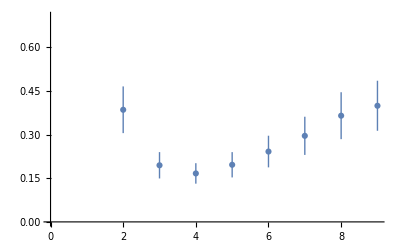

```mathematica
ListPlot[Table[{y,Around[Table[d4[[x]][[y]],{x,100}]]},{y,9}]]
```

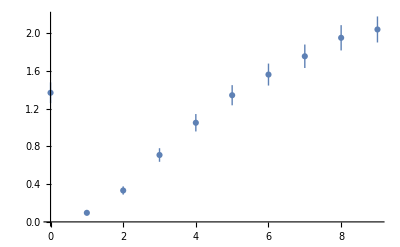

```mathematica
ListPlot[Table[{y-1,Around[Table[d1[[x]][[y]],{x,100}]]},{y,10}]]
```

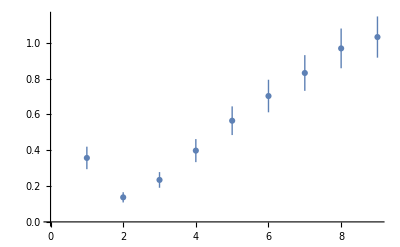

```mathematica
ListPlot[Table[{y,Around[Table[d2[[x]][[y]],{x,100}]]},{y,9}]]
```

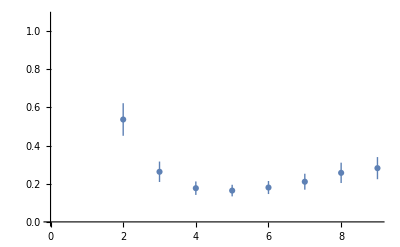

```mathematica
ListPlot[Table[{y,Around[Table[d5[[x]][[y]],{x,100}]]},{y,9}]]
```

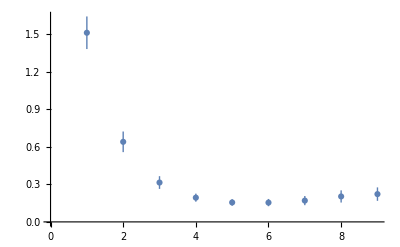

```mathematica
ListPlot[Table[{y,Around[Table[d6[[x]][[y]],{x,100}]]},{y,9}]]
```

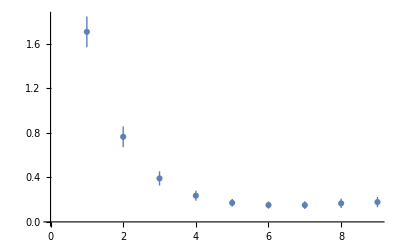

```mathematica
ListPlot[Table[{y,Around[Table[d7[[x]][[y]],{x,100}]]},{y,9}]]
```

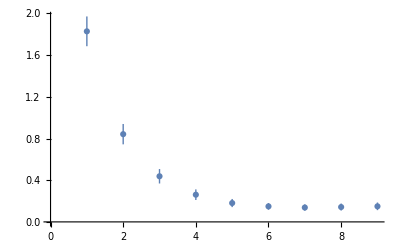

```mathematica
ListPlot[Table[{y,Around[Table[d8[[x]][[y]],{x,100}]]},{y,9}]]
```

```mathematica
l:= {{1,0},{2,0},{3,0},{4,0.013},{5,0.028},{6,0.069},{7,0.077},{8,0.091}}
```

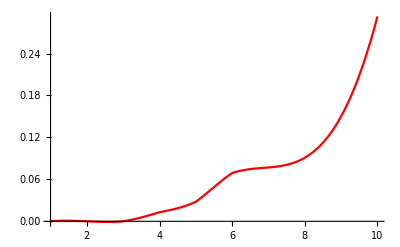

```mathematica
Plot[Interpolation[l][x],{x,1.,10},PlotStyle->Red]
```

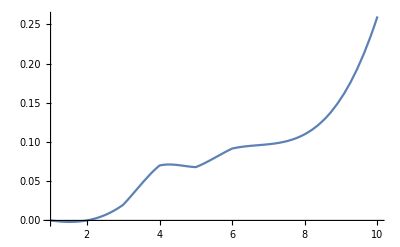

```mathematica
Plot[%99[x],{x,1.,10.}]
```

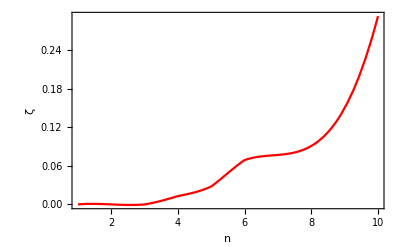

```mathematica
Show[%34,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{HoldForm[ζ],None},{HoldForm[n],None}},LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},Frame->True,(*Epilog->{Text[Style["(b)","Times New Roman",18],{0.2,2.8}]},*)PlotStyle->{Black,Dashed}]
```

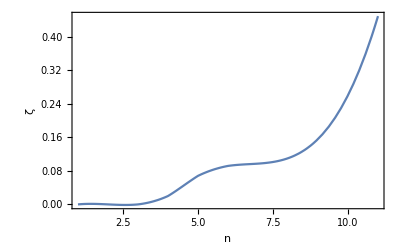

-Graphics-

```mathematica
Show[%1,PlotStyle->Red]
```

-Graphics-

```mathematica
l1:= {{1,ζ1},{2,ζ2},{3,ζ2},{4,ζ3},{5,ζ5},{6,ζ6},{7,ζ7},{8,ζ8}}
```

```mathematica
Interpolation[l1]
```

InterpolatingFunction[…]

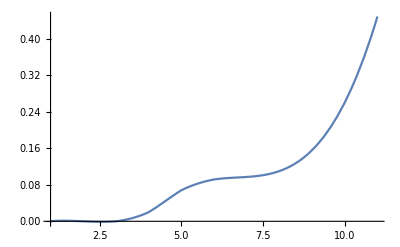

```mathematica
Plot[%110[x],{x,1.,11}]
```

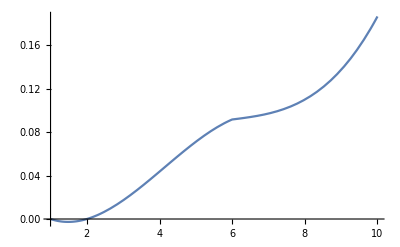

```mathematica
Plot[%106[x],{x,1.,10.}]
```